# PRIMAT (PRImordial MATter)

PRIMAT is a Mathematica code which computes the abundances of elements at the end of the big-bang nucleosynthesis (BBN).
It can be downloaded by registering at http://www2.iap.fr/users/pitrou/primat.htm

Version 0.3.0  (01/10/2024)

#### Modification to include Early Dark Energy

## Information

### Short description

*The implementation follows the presentation of the companion paper Pitrou, Coc, Uzan, Vangioni, Physics Reports, 04, (2018) 005. 
   All equation numbers, when non specified, refer to this companion paper, in its arXiv version (arXiv:1801.08023).

 *It is based on a previous Fortran code written by Alain Coc.
  
 *The user can modify several parameters which are in the preamble of the code :
 
   a) The nuclear reaction rates involved in the nuclear reaction network are tabulated in an external file which can be easily modified.
   b) The corrections to the weak-interaction reactions (n + ν <-> p^++ e^- and its related reactions), can be turned on and off with booleans. 
      The details of these corrections are given in the companion paper.
   c) Cosmological parameters, that is essentially the number of baryons (Ω_b) and the number of neutrino generations N_ν can also be modified.
   
 *The numerical integration is performed in two steps. First the cosmology and the thermodynamics of the plasma are solved, 
   and then the nuclear reactions are computed, the backreaction of the latter on the former being negligible (see companion paper).
   
 *The results are given as a set of interpolating functions of time for the abundances of individual species. 
   If one is interested in final abundances only, these are also directly accessible by evaluating these functions at final time.

  *A very basic Monte-Carlo exploration of uncertainties is provided at the end of the code. It is used in associated example notebooks located in the ‘Example’ folder.
   For each reaction, an uncertainty factor variance is provided and it is possible to run the code with these uncertainty parameters taking random values according to the variances (see [Coc et al. 2014]). A parallelization is possible for this Monte-Carlo exploration and the analysis of the results can be output in an external file and analyzed separately.
   
   *Several examples and applications are gathered in the ‘Examples’ folder.
   
   *Neutrino decoupling is handled using output files generated by the (non-public) Python code NEVO [Froustey et al. 2020].
   
   *An option allows to use only a reduced network of equations (weak interactions and 12 nuclear reactions), resulting in much faster results, though slightly different for Li7 abundances.

*** BASIC USAGE ***

*In the Evaluation menu, select ‘Evaluate notebook’. If asked the question ‘evaluate initialization cells first ?’, answer No. 
Then Mathematica proceeds in evaluating all cells, in order, and it should reach the end of the notebook (with the plots and results) in less than one minute.

*If the user erases the precomputed weak rates which are precomputed and stored in the ‘Interpolation’ folder, or asks for these rates to be re-precomputed, this can take considerably longer, typically one hour.

*Furthermore, when PRIMAT-Main.nb (this notebook) is opened and saved in Mathematica, the cells which are' initialization cells' are saved into the file PRIMAT-Main.m.
This *.m file contains all the important definitions, functions and variables which can be loaded from another notebook to perform BBN computations and analysis of results.
The 'Examples' Folder contains several typical applications which work exactly like that. First it loads all necessary definitions stored in PRIMAT-Main.m and then it performs a few useful computations for each selected example.

### Authors

This code is written and maintained by Cyril Pitrou^1 in collaboration with Alain Coc^2, J.-P. Uzan^3 and E. Vangioni^4.
Neutrino decoupling computations have been performed by Julien Froustey^5 with NEVO (non-public Python code) [https://arxiv.org/abs/2008.01074].

^(1,3,4,5)Institut d’Astrophysique de Paris (CNRS)
      98 bis Boulevard Arago
      75014 Paris, France
  
^2former CSNSM (CNRS, IN2P3)
  Orsay, France

emails and homepages :
-pitrou@iap.fr, http://www2.iap.fr/users/pitrou
-uzan@iap.fr
-vangioni@iap.fr
-alain.coc@csnsm.in2p3.fr
-froustey@iap.fr, http://www.iap.fr/useriap/froustey

### Dates and versions

In V0.2.0:
-Reaction Be7(d,p) is now tabulated in this external file and not given analytically and is taken from [Rij19]
-Decoupling of neutrinos with oscillations (precomputed with NEVO, see [Froustey et al. 2020]).
-Constants reevaluated with Particle Data Group 2020 data. Main change is G_Newt.
-QED corrections (pair production) to some nuclear rates included (see [Pitrou&Pospelov 2020]).
-An option to use only reduced nuclear network has been added.
-QED at order (e^3) included in plasma thermodynamics (reduces Neff by 0.001, see [Bennett et al. 2019])
-Cosmological parameters are set to the last column of table 2 of [Planck 2018 VI].

In V0.2.1:
-New dpg rate (reaction d + p <-> He3 + g) in new reaction file BBNRatesAC2022.dat. 
  Rate taken from Moscoso et al. 2021 

In V0.2.2:
-small modification to make it compatible with Mathematica 13.
-neutron lifetime update with PDG 2023.

In V0.2.3:
- Possibility to add distortions in an analytic form (with all the caveats due to the fact that neutrino self scatter and scatter of electrons/positrons and cannot tolerate spectral distortions for T>2MeV in principle).
- ‘Nrelat’ parameter added (number of relativistic decoupled species). So as to separate neutrinos from other thermalized but decoupled  relativistic degrees of freedom.
- Switched the mass database from nubase2016 to nubase2020
- Values of physical constants from PDG 2024

In V0.3.0
- PRIMAT now looks more like a package even though it is not yet a Package. 
When loading PRIMAT-Main.m from an external notebook, this now only loads definitions (and takes 0.3 seconds), but no computation is performed. The user can then modify the various options about physics or numerics, and then call for the function which either perform one run (RunNumericalIntegrals) or a MonteCarlo estimation of errors (RunPRIMATMonteCarlo), and then read the results. Examples are provided in the Example folder. It has been tested under a variety of combination of options, but please reports situations in which this still generates bugs. 
- It now takes less than a second for the small network of reactions (12 reactions) and 16 seconds for the full network (434 reactions), provided the weak rates are precomputed and stored in the CSV folder (which takes place the first time).
- There is a PythonInterface folder which explains how to call PRIMAT from python and how to read its results and modify its options. See readme file in that folder.
- The most crucial functions for performing numerical integration are compiled and stored on disk. Hence after the first run, the loss in compiling these functions is avoided by reading the compiled functions which are stored in the lib folder. 
- A $Parthenope option allows to replace the rates d+d <-> He3+n (ddn) and d+d <-> t+p (ddp) with the ones used in Parthenope3.0 (Gariazzo et al. 2021).
- The names of the folders in PRIMAT have changed.
- Tested on Mac OS and with Mathematica 14 only.
- Rate for d+a <-> Li6 + g replaced by [Trezzi2017]. New reaction file BBNRatesAC2024.dat.

```mathematica
Date[]
```

{2026,5,28,11,27,29.467986}

Mathematica version used :

```mathematica
$Version
```

14.1.0 for Mac OS X ARM (64-bit) (July 16, 2024)

### GPL

```mathematica
(* Copyright (C) 2018- Cyril Pitrou, Alain Coc *)

(* This program is free software; you can redistribute it and/or
 modify it under the terms of the GNU General Public License as
 published by the Free Software Foundation; either version 2 of
 the License,or (at your option) any later version.

This program is distributed in the hope that it will be useful,
  but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU
 General Public License for more details.

You should have received a copy of the GNU General Public License
 along with this program; if not, write to the Free Software
 Foundation, Inc., 59 Temple Place-Suite 330, Boston, MA 02111-1307,
  USA. 
*)
```

### Bibliography

Hereafter we use the following shorthands for the references cited.

BBN review with PRIMAT description

[Pitrou et al. 2018] C. Pitrou, A. Coc, J.-P. Uzan, E. Vangioni, Physics Reports, 04, (2018) 005, 1801.08023. 
[Pitrou et al. 2021] C. Pitrou, A. Coc, J.-P. Uzan, E. Vangioni, MNRAS, 525 (2023) 1, 476-488 , 2011.11320.

BBN references

[Bennett et al. 2019] J. J. Bennett, G. Buldgen, M. Drewes, Y. Y. Y. Wong,  JCAP 03 (2020) 003, 1911.04504 .
[Bernstein 1989] J. Bernstein, L. S. Brown, G. Feinberg, Rev. Mod. Phys 61 (1989).  
[Brown&Sawyer] L. S. Brown, R. F, Sawyer, Phys. Rev. D63, 083503 (2001) astro-ph/0006370.
[Cambier et al.] J. L. Cambier, J. R. Primack, and M. Sher, Nucl. Phys. B209, 372 (1982).
[Coc et al. 2012] A. Coc, S. Goriely, Y. Xu, M. Saimpert and E. Vangioni, Astrophys. J. 744 (2012) 1107.1117.
[Coc et al. 2014] A. Coc, J.-P. Uzan and E. Vangioni JCAP 1410 (2014) 050 1403.6694.
[Czarnecki et al. 2004] Czarnecki, Marciano and Sirlin, Phys Rev. D 70, 093006 hep-ph/0406324.
[Dicus et al.] D. A. Dicus, E. W. Kolb, A. M. Gleeson, E. C. G. Sudarshan, V. L. Teplitz, and M. S. Turner, Phys. Rev. D26, 2694 (1982).
[Esposito et al. 1999] S. Esposito, G. Mangano, G. Miele and O. Pisanti, Nucl. Phys. B540, 3 (1999) astro-ph/9808196.
[Froustey&Pitrou 2019] J. Froustey, C. Pitrou, Phys. Rev. D101 (2020) 043524, 1912.09378  
[Grohs et al. 2012] E. Grohs, G. M. Fuller, C. T. Kishimoto, M. W. Paris, and A. Vlasenko, astro-ph/1512.02205.
[Horowitz] astro-ph/0109209 (for weak-magnetism definition and related computations).
[Horowitz&Li] C.J. Horowitz, G. Li, astro-ph/9908219
[Heckler 1994] A. F. Heckler, Phys. Rev. D49 611 (1994).
[Ivanov 2012] A. N. Ivanov, M. Pitschmann, N. I. Troitskaya Phys. Rev. D88, 073002 (2013) hep-ph/1212.0332. 
[Kernan] P. J. Kernan, PhD thesis, Two astroparticle physics problems; solar neutrinos, and primordial ^4 He. Ohio State University (1993).
[Lopez&Turner 1998] R. E. Lopez and M. S. Turner, Phys. Rev. D59, 103502 (1999) astro-ph/9807279.
[Lopez et al. 1997] R. E. Lopez, M. S. Turner and G. Gyuk, Phys. Rev. D56, 3191 (1997), astro-ph/9703065.
[Mangano et al. 2001] G. Mangano, G. Miele, S. Pastor, M. Peloso, Phys.Lett. B534 (2002) 8-16, astro-ph/0111408.
[Mangano et al. 2005] G. Mangano, G. Miele, S. Pastor, T. Pinto, O. Pisanti, P. D. Serpico, Nucl.Phys. B729 (2005) 221-234 hep-ph/0506164.
[PArthENoPE] O. Pisanti et al. Comp. Phys. Com 178 956 (2008), 0705.0290. Update 2017: arXiv:1712.04378.
[Pitrou&Pospelov 2020] C. Pitrou and M. Pospelov, Phys Rev. C. 102 (2020) 015803, 1904.07795 .
[Seckel 1993] D. Seckel, hep-ph/9305311.
[Sirlin 1967] A. Sirlin Phys. Rev. 164, Vol 5, p1767 (1967).


Other references. Incomplete neutrino decoupling :

[Froustey et. al. 2020] J. Froustey, C. Pitrou, C. Volpe, JCAP 12 (2020) 015, 2008.01074.
[Hannestad 1995], S. Hannestad,  J. Madsen, Phys. Rev. D52, 1754 (1995), astro-ph/9506015.
[Gnedin 1997] N. Y. Gnedin, O. Y. Gnedin, AP. J. 509, 11-15 (1998), astro-ph/9712199.


Reaction rates 

They are listed in references of [Coc. et. al 2012] (see Table 4). We use the following acronyms :

NACRE (Angulo et al. 1999)
NACRE II (Xu et al. 2010, 2011)
DAACV04 (Descouvemont et al. 2004)
ILCCF10 (Iliadis et al. 2010)
CF88 (Caughlan& Fowler 1988)
MF89 (Malaney& Fowler 1989)
Boy93 (Boyd et al. 1993)
Bal95 (Balbes et al. 1995)
Hei98 (Heil et al. 1998)
Rau94 (Rauscher et al. 1994)
Des99 (Descouvemont 1999)
Bea01 (Beaumel et al. 2001)
Tan03 (Tang et al. 2003)
Wan91 (Wang et al. 1991)
Efr96 (Efros et al. 1996)
Wie87 (Wiescher et al. 1987 Wiescher,Harms,Goerres,Thielemann& Rybarcyk ApJ 316 (1997) 162  1001.2053)
Bar97 (Bardayan& Smith 1997)
Koe91 (Koehler& Graff 1991)
And06 (Ando et al. 2006)
Ser04 (Serpico et al. 2004)
Wag69 (Wagoner 1969)
Has09 (Hashimoto et al.2009)
Wie89 (Wiescher et al.1989)
FK90 (Fukugita& Kajino 1990)
Bru91 (Brune et al.1991)
Bec92 (Becchetti et al.1992)
Iga95 (Igashira et al.1995)
Cyb08 (Cyburt& Davids 2008)
Miz00 (Mizoi et al. 2000)
Nag06 (Nagai et al. PRC 74 (2006) 025804 AC2010)
Has09c (Hashimoto et al.PLB 674 (2009) 27)
FK90  (Fukugita& Kajino,PRD 42 (1990) 4251)
Rau94 (C. Rauscher et al.ApJ 429 (1994) 499)
Men12 (C Mendes et al.PRC 86 (2012) 064321)
Tang03 (Tang et al.PRC 67 (2003) 015804)
Bar97C (Bardayan& Smith PRC 56 (1997) 1647)
Kaw91 (Kawano,Fowler,Kavanagh,Malaney ApJ 372 (1991) 1-7)
Cam08 (Camargo et al.Phys.Rev.C 78,034605 (2008))
Ili16 (Iliadis et al. 2016)
Rij19 (Rijal et al. Phys. Rev. Lett. 122, 182701 (2019))
Gar21 (Gariazzo et al. 2021 Parthenope Revolution, Computer Physics Com. 271 (2022) 108205)
Yeh22 [ Yeh, Shelton, Olive, Fields  [JCAP 10 (2022) 046]
[Trezzi 2017] (Trezzi, D., Anders, M., Aliotta, M., et al. (Luna) 2017,  Astroparticle Physics, 89, 57)
[Moscoso 2021] (J. Moscoso, R. S. Souza, A. Coc, C, Iliadis, Astrophysical Journal, 923:15 (2021)).

Numerical values

[Planck 2015 XIII] Ade et al. A.&A. 594, A13 (2016).
[Planck 2018 VI] A.&A. (2020). We use TT+TE+EE+lowE+Lensing+BAO parameters (last column of table 2).
[PDG17] Particle Data Group 2017.
[PDG20] Particle Data group 2020.
[PDG23] Particle Data group 2023
[PDG24] Particle Data Group 2024 

Masses of nuclei previously from nubase2016.asc  (Chinese Physics C 36 (2012) 1157-1286) which can be downloaded from Nuclear Data Services
Switched to the 2020 update of that database which is nubase_ 4.mas20.txt  (Chinese Physics C 45 (2021) 030001) which is also found on from Nuclear Data Services.

### Directory set up

We set the directory. This cell is not an initialization cell, and is not save in the .m file. Indeed this is only needed if we run PRIMAT-main.nb directly.
Otherwise if load it as a package (loading PRIMAT-main.m file), then we need to determine the absolute path and this is stored in $PackageDirectory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pitrou/Cosmologie/SDrive/iap/notebooks/PRIMAT2024

```mathematica
$PacDir=DirectoryName[$InputFileName];
$PackageDirectory:=$PacDir;
$CSVDirectory:=$PackageDirectory<>"CSV/";
$libDirectory:=$PackageDirectory<>"lib/";
$PlotsDirectory:=$PackageDirectory<>"Plots/";(* not used *)
$RatesDirectory:=$PackageDirectory<>"Rates/";
$ResultsDirectory:=$PackageDirectory<>"Results/";
```

## Constants of Physics

#### cgs system

We use cgs system with Kelvin. (For instance an erg is 1 g cm^2 s^-2).
By definition these are set to one in these units. Any change of system of units can be made by modifying these variables only.

For instance if we want to use the m/kg/s system we need only put cm=0.01 and gram = 0.001 below.

As a check, final results should not depend on these conventions since abundance rates are dimensionless.

```mathematica
second=1;
cm=1;
gram=1;
Kelvin=1;
```

When taking values from the kg/m/s system, we use the factors

```mathematica
kg=10^3 gram;
meter = 10^2 cm;
km=10^3 meter;
Joule =kg meter^2/second^2; (* This gives 10^7 ergs *)
DensityUnit=gram/cm^3;
Hz=1/second;
barn=10^(-24)*cm^2;
```

```mathematica
Giga=10^9;
Mega=10^6;
Kilo=10^3;
```

```mathematica
pc=3.0856777807 10^16 meter; (* The parsec *)
Mpc=Mega pc;
```

#### Fundamental constants (exact values since the 2019 revision of the International System of Units)

```mathematica
kB =1.380649 10^-23 Joule / Kelvin;(* Boltzmann constant in J/K *)
clight=2.99792458*10^8*meter/second; (* speed of light in cm/s *)
hbar=6.62607015/(2π)10^-34 Joule second;
Avogadro=6.02214076 10^23;
```

When using masses of particles, we use eV and MeV that we convert in the cgs system

```mathematica
eV=1.602176634 10^-19 Joule;
keV = Kilo eV;
MeV=Mega eV;
GeV=Giga eV;
```

#### Interactions constants

```mathematica
GN=6.67430 10^-11 meter^3/kg/second^2; (* Gravitation constant PDG2024 *)
GF=1.1663788*10^-5/(GeV)^2; (* Fermi Constant PDG2024*)
gA=1.2754; 
(* Axial current constant of structure of the nucleons. It was 1.2723(+-23) in PDG2016 *)
(* However post 2002 data suggest 1.2755(11) as advised by William Marciano*)
(* PDG2020 value: 1.2756(13) *)
(* We now use PDG2024 value 1.2754(13) which is much more consistent with the neutron lifetime *)
```

```mathematica
fWM=3.7058/2(*1.853*); (* Weak magnetism see 1212.0332*)
radiusproton=0.841*10^-15 meter (*(arXiv:1212.0332)*);
```

```mathematica
2.79284734463-1-(-1.91304273)
```

3.70589

fWM is the weak magnetism constant.  See Eq. [Horowitz&Li] for definition with the value given by its Table 1. 
Note that all expressions in [Seckel 1993] seem to have a factor 2 difference. That is all interaction rates involving the weak magnetism in [Seckel 1993] are underestimated by a factor 2. Expressions in [Lopez et al. 1997] seem correct however.

```mathematica
αFS=1/137.035999084;(* Fine structure constant =e^2/(4π) *)
```

#### Particle masses

Throughout, masses stand always for mc^2 so that they are in fact energies. This avoids putting unnecessary c^2 factors

```mathematica
me=0.510998950 MeV; (*PDG2024*)
mn=939.56542052 MeV;(*PDG2024*)
mp=938.27208816 MeV;  (*PDG2024*)
Q=mn-mp; (* Mass difference between neutrons and protons *)
Subscript[m, Nucleon]=mn;

Subscript[m, W]=80.3692 GeV; (* Mass of the W Boson. *) 
Subscript[m, Z]=91.1880 GeV;
```

The energy difference between neutron and proton in MeV gives 1.2933324(5) [PDG 2024].

```mathematica
Q/MeV
```

1.29333

The atomic mass, the Helium4 mass (in units of atomic mass) and Hydrogen mass (in units of atomic mass).

```mathematica
(* Values from AME 2020, Wang et al 2021 Chinese Phys. C 45 030003 *)
ma=931.49410242 MeV;
He4Overma=4.002603254130;
H1Overma = 1.007825031898;
```

## Options

### Physical parameters

#### Main parameters

Baryons density fraction. This is Ω_b h^2.

```mathematica
Meanh2Ωb0Planck=0.022425;(*[Planck 2018 VI, Last column of table 2 (and checked from the Planck Legacy Markov chains)]*)
σh2Ωb0Planck=0.000136;(* Standard deviation*)(* Planck 2018 VI states 0.00014 but from the Legacy Markov chains we infer the value 0.000136 *)
```

```mathematica
Meanh2Ωb0=Meanh2Ωb0Planck; (*Can be redefined*)
σh2Ωb0=σh2Ωb0Planck;
```

Neutron life time PDG 2024  https://pdg.lbl.gov/2024/listings/rpp2024-list-n.pdfhttps://pdg.lbl.gov/2024/listings/rpp2024-list-n.pdfNonehttps://pdg.lbl.gov/2024/listings/rpp2024-list-n.pdfHyperlinkActionRecycledHyperlinkActive

```mathematica
Meanτneutron=878.4;(* This can be redefined *)
στneutron=0.5;
```

We can add extra relativistic degrees of freedom that would be considered as being fully decoupled. Hence they behave as neutrino in the Fully decoupling approximation with there energy density ~1/a^4 exactly.
By convention these relativistic degrees of freedom are a number of Fermi-Dirac species (with no chemical potentials) or sterile/decoupled  neutrino species.

```mathematica
Nrelat:=0.;
```

When we do not use MonteCarlo to estimate uncertainty, then the value of neutron lifetime abundancs is given by the mean.
Otherwise we will add a random contribution (from a normal distribution) associated with the standard deviation.

```mathematica
τneutron=Meanτneutron;
h2Ωb0=Meanh2Ωb0;
```

#### Secondary parameters

CMB temperature today

```mathematica
TCMB0:=2.7255Kelvin;
σTCMB0:=0.0006 Kelvin;(* [Planck 2015 XIII] *)
```

h is the Hubble rate in units of 100 km/s/Mpc.

```mathematica
h:=0.6766; (*+-0.0042 *)(*[Planck 2018 VI TT+TE+EE+lowE+Lensing+BAO]*)
```

Cold Dark Matter density fraction. This is  Ω_c h^2.

```mathematica
Meanh2Ωc0=0.11933;(* [Planck 2018 VI, last column of Fig. 2]*)
σh2Ωc0=0.00091;
h2Ωc0:=Meanh2Ωc0;
```

### BBN options

Nuclear rates

Most nuclear reactions rates are tabulated in a separate file. The rest of the rates are given as analytic fits.
The external file loaded with all reactions definitions and rates is given by the name TabulatedReactionsFile.

The user can also ask for the reduced network (12 nuclear reaction), see below, 
in which case only the first 12 nuclear reactions are selected and no extra analytic reactions

```mathematica
TabulatedReactionsFile="BBNRatesAC2024.dat";
TabulatedReactionsFileSmallNetwork="BBNRatesAC2024_small_network.dat";(* For small network of 12 nuclear reactions *)
```

An option to use the Parthenope rates for d + d <-> t + p and d + d <-> n + He3. If it is true, then the codes uses TabulatedReactionsFileParthenope or TabulatedReactionsFileSmallNetworkParthenope if the small network option (see below) is True.

```mathematica
$Parthenope = False;
```

```mathematica
TabulatedReactionsFileParthenope="BBNRatesAC2024_ddn_ddp_Parthenope.dat" ;(*A file fhere the d+d<->n+He3 and d+d<->t+p rates are the ones used in Parthenope (Gariazzo 2021)*)
TabulatedReactionsFileSmallNetworkParthenope="BBNRatesAC2024_small_network_ddn_ddp_Parthenope.dat";
(*A file where the d+d<->n+He3 and d+d<->t+p rates are the ones used in Parthenope (Gariazzo 2021), and with just 12 nuclear reactions.*)
```

We can decide to keep only a subset of the equations by specifying the maximum nuclear mass. The default value is Infinity, meaning that we do not cut the network.

```mathematica
MaximumNuclearMass=Infinity;
```

We can also reduce the network to its 12 first reactions. This is enough for the first light elements. 
It consists in the first 12 reactions of the tabulated reactions (those in the file TabulatedReactionsFile).
Furthermore, if $ReducedNetwork is selected, no extra analytic reactions are added so that we really have only a total of 12+1 reactions (because we also have weak interactions).

```mathematica
$ReducedNetwork=False;
```

```mathematica
SmallNuclearNetworkSize=12;
```

Monte-Carlo uncertainty estimation options

```mathematica
$RandomNuclearRates=False;
$MaxVariationRate=1000;
```

If $RandomNuclearRates is True, then each time we build the equations of the nuclear network, we generate rates with a log normal distribution according to the ‘f’ specified (see Eq. 4.5 of [Coc et al. 2014] for definition of f). 
We limit f to the values 1/$MaxVariationRate<f<$MaxVariationRate .

Rescaling of some rates

It is possible to rescale some rates by choosing their rescaling factor below. First, the option $RescaleSomeRates must be set to True otherwise the rescaling factors are ignored.

```mathematica
$RescaleSomeRates=False;
```

For each reaction whose rate we want to rescale, we need to know the exact name of the reaction. The names of reactions are collected in tables below in the core of the notebook. For a reaction of the type a + b -> c + d, the name is “abTOcd”. However one needs to know the order of the initial particles and of the final particles, and to put correctly the photons if they appear. Hence it is recommended not to guess the name of the rate, but to properly read it from the Tables below located in the section “Collecting all reaction rates”.
For instance the reaction He3 + t > He4 + d  (we use d for H2 and t for H3 and a for He4) has name He3tTOHe4d. The factor to modify it is therefore He3tTOHe4dFactor.

As an example, we show how to introduce a rescaling factor for the d + p -> He3 + γ,  d + d -> He3 + n, and d + d -> H3 + p  reactions hereafter. 
If we want to vary other rates, one needs only to set the numerical value of their associated factors .

```mathematica
If[$RescaleSomeRates,
dpTOHe3gFactor=1;
ddTOHe3nFactor=1;
ddTOtpFactor=1;
];
```

Note that this procedure is only valid for variation of rates which are given as tables in the external file. If the user wants to vary a rate whose form is analytic, it is sufficient to add a factor “ReactionFactor” in the definition of the analytic forward rate (forward[T9_]:= ....). It is then advised to write here (so that all modifications can be turned on and off without forgetting that some rates have been modified)

If[$RescaleSomeRates,
ReactionFactor=100;,
ReactionFactor=1;
]

We recall that the syntax for If/then/else is

If[Condition, 
commandtrue;,
commandfalse;
]

QED corrections (pair production) to nuclear rates

If this options is set to True, then we rescale some rates due to pair productions in the final state. 
See [Pitrou&Pospelov 2020].

```mathematica
$NuclearRatesQEDCorrections=True;(* recommended value is True *)
```

### Weak rates options

Since the weak interaction rates, that is the rates of weak reactions of the type n + ν <-> p + e and associated reactions, depend only on temperature, 
these can be computed once and for all so as to explore the dependence in cosmological parameters or other parameters. 
  
If $RecomputeWeakRates is set to True, the code recomputes the weak rates. 
Otherwise it reads them from files previously stored. If the file does not exist, it recomputes the rates.

If $ParallelWeakRates=True this is done using parallelization over the various CPUs that Mathematica can detect (be aware that when $NEVO=TRue , it slows things done because of badly sharing memory. I cannot find the reason.)

```mathematica
$RecomputeWeakRates=False;
$ParallelWeakRates=False;
```

There are several booleans corresponding to the different types of corrections which can be considered in these weak rates. 
The name of the file used for storing the rates is built out of these booleans. 

Since the corrections do not add linearly, there are in principle many choices of corrections, but the only meaningful
choices are those without any corrections and those with all corrections included. 
Or maybe those with just one correction added, so as to check its amplitude.

```mathematica
$RadiativeCorrections=True;(*Recommended True*)

$ResummedLogsRadiativeCorrections=True;(*Recommended True*)
$RelativisticFermiFunction=True;(*Recommended True*)
```

1) If $RadiativeCorrections is set to True, we use Coulomb and radiative corrections (see section III.E of companion paper. The corrections are implemented in Eqs. 101 and 104.).
If $ResummedLogsRadiativeCorrections is set to True we use Eq. 15 of [Czarnecki et al 2004] which amounts to resumming some higher order radiative corrections, and this is also Eq. B35 of the companion paper.

If $ResummedLogsRadiativeCorrections is False we use simply Eq. 7 of the same reference, which corresponds to Eq. 103 and B30 of the companion paper.
If $RelativisticFermiFunction is True we use the relativistic Fermi function (Eq. 5 in [Ivanov 2012]), which corresponds to Eq. 100 of the companion paper. Otherwise we use the standard non-relativistic Fermi function, given by Eq. 99 of the companion paper.

```mathematica
$RadiativeThermal=True;(*Recommended True but it is much slower. Since the modification brought by these corrections is very small, setting False is acceptable.*)
$CorrectionBremsstrahlung=True;(*Recommended True*)
```

2) If $RadiativeThermal set to True, the thermal radiative corrections are taken into account. 
The first expressions date back from [Dicus et al.]. However other expressions were derived subsequently in [Lopez&Turner 1998], [Cambier et al.] and [Esposito et al. 1999] among other references. [Kernan] pointed typos and compared the differing results of [Cambier et al.] and [Dicus et al.]. These were correctly computed in [Brown&Sawyer].
In the companion paper, the thermal radiative corrections are given by Eq. 108 with the various contributions given by Eqs. 109-113. However, it is easier to compute the first contribution of 108 using Eqs. 109 (with definition B41), but to compute the second and third contributions of 108 using Eqs. B50-B51.

We showed in companion paper that Bremsstrahlung corrections need also to be added to be fully consistent with [Brown&Sawyer]. This is controlled by the boolean $CorrectionBremsstrahlung. If $RadiativeThermal is set to True, then these bremsstrahlung corrections (corresponding to Eqs. 107a and 107b in companion paper with the definitions B48-B49) are also incorporated if $CorrectionBremsstrahlung is True.

```mathematica
$FiniteNucleonMass=True;(*Recommended True*)
```

3) If $FiniteNucleonMass is set to True, we take into account the finite mass of nucleons by keeping corrections in 1/M_n in the collision integrals of the weak rates.
Our method is described in the companion paper and differs from earlier literature.
There is a suboption for these finite mass corrections  which is

```mathematica
$CoupledFMandRC=True;(*Recommended True*)
```

If $CoupledFMandRC is False, finite mass corrections are computed from the Born results with no radiative null temperature corrections. If this is set to True, the finite mass corrections are applied to the rates on which the Coulomb and radiative corrections are taken into account. True is the advised value. 

The expressions implemented are Eqs. 114 when $CoupledFMandRC is False, with the definition B23. If $CoupledFMandRC is True, then we use Eqs. 115 with the Fermi and radiative corrections corresponding to the above choices for radiative corrections.

4) Mass shifts due to QED plasma effects are ALREADY taken into account in thermal radiative corrections.
However it is possible to turn the option $QEDMassShift to true to check how this affects the rate when taken individually.
Apart to satisfy this curiosity, this option should be set to False in all cases.

```mathematica
$QEDMassShift=False;
```

### Plasma physics options

```mathematica
$QEDPlasmaCorrections=True;(*Recommended True*)
$CompleteQEDPressure=True;(*Recommended True*)
$QEDOe3 = True; (*Recommended True*)
```

If $QEDPlasmaCorrections is set to True, the QED corrections to the pressure and the energy density are taken into account. This affects for instance the expansion rate via the Friedmann equation. 
Expressions can be found in [Lopez&Turner 1998], [Mangano et al. 2001] or in [Heckler 1994]. See also the companion paper where Eqs. 48-52 are used inside Eq. 55 to modify the entropy and Eq. 58 to modify the energy density.
If $CompleteQEDPressure is False, the subdominant term is ignored. Otherwise it is included. We checked it is so subdominant that it does not change the results.
If $QEDOe3 is True, then order e^3 corrections to the Plasma (to P and ρ) are included, Following [Bennett et. al. 2019].

```mathematica
$RecomputePlasmaCorrections=False;
```

Since the QED effects depend on temperature, they need to be computed only once for all and they are stored on a file. But we can force the recomputation of these corrections by setting $RecomputePlasmaCorrections to True;

### Neutrinos options

Neutrinos generations. Usually this is 3.

```mathematica
NeutrinosGenerations:=3.;
```

#### Neutrino incomplete decoupling options

```mathematica
$IncompleteNeutrinoDecoupling=True;(*Recommended True*)
```

If $IncompleteNeutrinoDecoupling is set to True, the entropy transfer from e^± annihilations to neutrinos is taken into account. Indeed if we consider the details of the decoupling of neutrinos, it is found that decoupling is incomplete by the time electrons and positrons annihilate into photons. This results in a slight overheating of neutrinos and cooling of the electrons/photons plasma.
The advised value for $IncompleteNeutrinoDecoupling is True.

```mathematica
$NEVO=True; (* Recommended True *)
$TrueTνe=True;(* Recommended True *) 
$FileSuffix="";(*Suffix of the file name in which NEVO results are stored. *)
```

The original PRIMAT approach consisted in using a fit for the heating function of the neutrinos due to incomplete decoupling. The fitting functions which is used is the one given in [PArthENoPE]. It is used in Eq. 63 of the companion paper. In this approach, all three flavors of neutrinos have equilibrium distributions at a common temperature derived in Eq. 64 of the companion paper. This original method is chosen if $NEVO = False.

However, if $NEVO is set to True, we directly import the neutrino effective temperatures (and the heating function) from the results obtained with NEVO, a Python code designed to implement neutrino evolution through the MeV age (developed by Julien Froustey and Cyril Pitrou, and described in [Froustey et al. 2020]). This enables to take into account two additional effects: the different decoupling of electron and muon/tau neutrinos, resulting in different effective temperatures (implemented if $TrueTνe is set to True) and non-thermal distortions of the neutrinos distribution functions (implemented if $SpectralDistortions is set to True, see below).

Important: it would be inconsistent to set $SpectralDistortions = True but $IncompleteNeutrinoDecoupling = False, except if the are analytic distortions included (see below). That is why when computing the weak rates, spectral distortions are included only if both these options are set to True, or if $AnalyticDistortions is set to True.
The code checks for most obvious inconsistent options and modifies them (printing a warning message)

The common neutrino average temperature can therefore be computed in two different (but, in principle, equivalent) ways: 
1/ through the heating function 
2/ directly from the effective temperatures. 
If $Taverage𝒩 is set to True, the first method is used but we prefer the second method, hence we set it to False.

```mathematica
$Taverage𝒩=False;(*Recommended False *)
```

Files in which NEVO results are stored

```mathematica
(* When providing different files for neutrinos and antineutrinos *)
(*FileNEVOneutrinos = "CSV/NEVOneutrinos"<>$FileSuffix<>".csv";
FileNEVOantineutrinos = "CSV/NEVOantineutrinos"<>$FileSuffix<>".csv";*)


FileNEVOneutrinos := $CSVDirectory<>If[$QEDPlasmaCorrections,If[$QEDOe3, "NEVOPRIMAT" ,"NEVOPRIMAT_QED2"],"NEVOPRIMAT_NoQED"]<>$LocalSuffix<>".csv";
FileNEVOantineutrinos := FileNEVOneutrinos;
```

#### Degenerate Neutrinos options

Possible initial chemical potential in the neutrino initial conditions (the same for all generations). In that case set $DegenerateNeutrinos = True.
warning : standard BBN is with non-degenerate neutrinos. See section VI.C of the companion Phys. Rept. for effects of chemical potential.

Degenerate neutrinos are incompatible with $NEVO. Indeed either it uses the files provided by default for which all chemical potentials are vanishing.
Or we couple it with alternative (and private) results of NEVO when exploring the effect of neutrino oscillations and self-interactions when there are initial asymmetries, as was done in Froustey&Pitrou JCAP 03 (2022) 065, arxiv:2110.11889.
warning : we do not check if the user has set $NEVO=False when asking for degenerate neutrinos. So these options are to be used with caution.

```mathematica
$DegenerateNeutrinos=False;(*Recommended False if using the default runs of NEVO.*)
μOverTν=0.;

ξν:=If[$DegenerateNeutrinos,μOverTν,0];
```

#### Spectral distortions

```mathematica
$SpectralDistortions = True;(* Recommended True *)
```

If $SpectralDistortions = True then spectral distortions are added to electronic neutrinos (and also all other flavours but this could be changed)

1) $NEVO distortions
If $IncompleteNeutrinoDecoupling = True and $NEVO=$TrueTνe=True, then it is advised to also ask for $SpectralDistortions since they were computed in the decoupling code NEVO. They are then used if $AnalyticDistortions=False below and superseded otherwise. In the case NEVO distortions are used, they induce no change of neutrino energy density since in that case distortions are defined with respect to a reference spectrum in such a way that there is no energy density contained in the distortions (of both neutrino and antineutrino).

2) The user can define custom distortions (which are the same in neutrinos and antineutrinos) with analytic forms by setting $AnalyticDistortions=True.
 It is slightly inconsistent because these would impact the neutrino decoupling. Hence the most consistent set of parameters consists in setting $IncompleteNeutrinoDecoupling=False, so they can be viewed as distortion which are added after decoupling but before neutron/proton freeze out.
If $AnalyticDistortions = True, then an analytic form of the distortions is used. The user can modify the code to define custom distortions inside the code itself.
For the moment the same distortion shape is put in all neutrino flavors. Also only the electronic neutrino distortion affects the weak-interaction, but the fact that we put the distortion in all flavors has an impact on the energy density contained in the distortion.

Two basic analytic forms are however readily provided  :

  a) A μ-type distortion, corresponding to the difference between a Fermi-Dirac spectrum with a given chemical potential with and a Fermi-Dirac spectrum with a reference chemical potential. 
  If $DegenerateNeutrinos=True above, then the chemical potential of the reference neutrino spectrum is with a non-vanishing chemical potential ξν=μOverTν (and otherwise ξν=0), that is 1/(ⅇ^(y-ξν)+1) for neutrinos and  1/(ⅇ^(y-ξν)+1) for antineutrinos (with y = E/T_ν). Then the μ-type distortion, corresponds to a Fermi-Dirac spectrum with ξν + Δξν. Hence the distortion for neutrinos is defined by 1/(ⅇ^(y-(ξν+Δξν))+1) - 1/(ⅇ^(y-ξν)+1) and for antineutrinos it is 1/(ⅇ^(y+(ξν+Δξν))+1) - 1/(ⅇ^(y+ξν)+1). It is ill-considered to use this kind of distortion, because whatever the chemical potential, it can be put in the reference chemical potential. Hence this usage is only meant to test the code, for instance checking that having μOverTν=Somevalue and Δξν=0 is equivalent to μOverTν=0 and Δξν = somevalue.
  
  b) A Y-type distortion corresponding to the equivalent of the SZ (Sunyaev-Zeldovich) distortion, that is corresponding to the spectrum shaped by the Kompaneets equation (Kompaneets 1957, Soviet Phys JETP, Vol. 4 N. 5 p 730) but with an up-scattered Fermi-Dirac distribution (instead of an up-scattered Planck spectrum as for the SZ effect on photons of the CMB).
  The collision term of the Kompaneets equation is of the form 1/E^2∂_E (E^4 ∂_E f) where f is the reference spectrum  (Fermi-Dirac with or without chemical potential depending on $DegenerateNeutrinos option and μOverTν value). 
  Hence the distortion is of the form Y_SZ*1/E^2∂_E (E^4 ∂_E  1/(ⅇ^(y-ξν)+1) ) for neutrinos and Y_SZ*1/E^2∂_E (E^4 ∂_E  1/(ⅇ^(y+ξν)+1) ). Y_SZ is the amount of up-scattering and is proportional to the optical depth multiplied by (Ts/ms) where Ts and ms are temperature and mass of the heavy species which is responsible for the up-scattering. The total energy density in neutrinos is then modified to be ρν(1 + 4 Y_SZ) where ρν is the energy density without the SZ distortion.
  
  Note that the true Kompaneets equation must be a stationary point if the species responsible for the up-scattering is at the same temperature T_s as the scattered species. Hence the total rate per optical depth is
		df/dτ=1/(m_s E^2)∂_E [E^4 (T_s∂_E f + f(1-f))]  (note the change of sign with respect to a Kompaneets equation for bosons=photons where we have f(1+f) since for fermions we have Pauli-blocking instead of stimulated emission for bosons), and if f is initially a Fermi-Dirac distribution at temperature T_ν (with whatever chemical potential), then in the low scattering approximation (Born approximation)  f(1-f) = - T_ν ∂_E f hence the Kompaneets equation is in the form
    df/dτ ~(T_s-T_⋁)/m_s 1/E^2∂_E (E^4 ∂_E f)   which implies that the distorted spectrum is approximately f-f_FD =   Y_SZ 1/E^2∂_E (E^4 ∂_E f_FD)  with Y_SZ = τ*(T_s-T_⋁)/m_s.

```mathematica
$AnalyticDistortions = False;(* Recommended False. Only for experimental investigation of neutrino distortions. *)
Δξν=0.;
YSZ=0.;
```

### Early Dark Energy (EDE) Options

```mathematica
1032/9.74
```

105.955

```mathematica
$EDEBool = True;
wnEDE=1.;
zcEDE=10^(8);
fEDE=0.;

acEDE := 1/(1+zcEDE)
```

We consider

which implies with 

that

Assuming that radiation scales only as 1/a^4 the maximum of  is obtained when

We parametrize with the value of a_c or z_c and ρ(a_c). 

Or even better we can parameterize with the maximum fraction of EDE. Assuming that radiation scales only as 1/a^4, hence after reheating, we get

Some checks of analytics :

```mathematica
ρEDEt[a_]:=ρEDE0(1+(a0/ac)^(3(1+wn)))/(1+(a/ac)^(3(1+wn)));
ργt[a_]:=ρ0*(a0/a)^4;

FullSimplify[Exp[-Integrate[3(1+wn)/a/(1+(ac/a)^(3(1+wn))),a]],Assumptions->ac>0&&a>0]
```

1/((a^(3+3 wn)+ac^(3+3 wn)) (1+wn))

```mathematica
Simplify[D[ρEDEt[a]/(ργt[a]+ρEDEt[a]),a],Assumptions->ac>0&&a>0]
```

-(a^3 a0^4 (a0^(3+3 wn)+ac^(3+3 wn)) (-4 ac^(3+3 wn)+a^(3+3 wn) (-1+3 wn)) ρ0 ρEDE0)/((a^(3+3 wn) a0^4 ρ0+a0^4 ac^(3+3 wn) ρ0+a^4 (a0^(3+3 wn)+ac^(3+3 wn)) ρEDE0)^2)

```mathematica
Simplify[D[ρEDEt[a]/ργt[a],a],Assumptions->ac>0&&a>0]
```

-(a^3 (a0^(3+3 wn)+ac^(3+3 wn)) (-4 ac^(3+3 wn)+a^(3+3 wn) (-1+3 wn)) ρEDE0)/(a0^4 (a^(3+3 wn)+ac^(3+3 wn))^2 ρ0)

### Monte - Carlo estimation of errors

There are 3 booleans which control what variables are varied randomly.
-Nuclear rates ($RandomNuclearRates)
-Neutron lifetime ($Randomτneutron)
-And possibly baryons abundance according to [Planck 2015] results when this is interesting to vary it as well ($Randomh2Ωb).

```mathematica
$Randomτneutron=False;
$Randomh2Ωb=False;
```

This variable determines if parallelization is used when doing Monte Carlo

```mathematica
$ParallelBool=False;
```

### Numerical options

Miscellaneous options

```mathematica
$InterpolateAnalytics=True;
```

It is slightly faster to interpolate the analytic expressions of nuclear reaction rates. Setting $InterpolateAnalytics to True is recommended.

```mathematica
$HistoryLength=10;
```

This is to avoid Mathematica to store too many results in memory. Only the past $HistoryLength results are kept in computer memory (this is standard Mathematica option).

```mathematica
$PaperPlots=False;
$ResultsPlots=False;
```

If $PaperPlots is set to True, the most important plots are constructed and they are output in pdf in the ‘Plots’ subfolder. 
Unless interested in reproducing the plots of the companion paper, this should be set to False to avoid any loss of time in the code.

If $ResultsPlots is True the results for the abundances are plotted at the end and exported in pdf files. Similarly, to avoid loss of time this should be set to False.

Numerical precision

```mathematica
$CompileNDSolve=True;
```

If $CompileNDSolve is set to True (advised), then the differential equation solver uses compiled functions. This is slightly faster.

```mathematica
$StoreCompilation=True;(*Stores compilation in lib folder if True. Otherwise it is compiled everytime the Kernel is loaded (a few seconds lost) *)
$Recompile=False;(*If this true it forces the compilation of previously compiled and stored functions. May be necessary if you change something subtle. Or you erase all files in the lib folder and this will force the Recompilation as well..*)
```

```mathematica
$BDFOrder=2;
```

Order of numerical scheme for Backward Differentiation Scheme (BDS) integration. 
-Order 1 works well but is slow. 
-Order 2 (advised) is faster. Higher orders result in numerical crash.

```mathematica
PrecisionNDSolve=2;(* Put 2 here is the best choice *)
```

PrecisionNDSolve is a precision parameter used in the differential equation solver. It is tuned such that 0 gives reasonable results, 1 gets very good results, and 2 gets excellent results and 3 gets super dupper precise results (10^-5 precision).

```mathematica
AccuracyNDSolve:=15+PrecisionNDSolve;
```

We slave AccuracyNDSolve to PrecisionNDSolve. This is roughly the number of digits of precision behind the dot, so increasing it will lead to always better results but this can crash if the accuracy required is too strong.

```mathematica
NTemperaturePoints=1000; (*1000 is enough*)
```

Number of points in discretization of temperature between the highest temperature (10^12 K) and the lowest (~10^7.5K).  1000 is enough.
Sampling is performed with NTemperaturePoints+1 points. Spacing is performed logarithmically, with Log_10.

```mathematica
InterpOrder=3;
```

Order of polynomials used in interpolations of reaction rates. Usually with Spline functions.

```mathematica
$FastPENRatesIntegrals=True;
```

If $FastPENRatesIntegrals is set to True, it uses a Simpson method for numerical integrals. Otherwise it uses the Mathematica function NIntegrate which is more accurate (adaptative refinement of integral) but much slower.

```mathematica
$PENRatesIntegralsPoints=200;(*200 is enough *)
```

In case $FastPENRatesIntegrals is set to True, $PENRatesIntegralsPoints is the number of points used to perform the numerical integrals. 200 is enough. 400 is ultra precise.

```mathematica
SetOptions[SelectedNotebook[],PrintPrecision->8]
```

We increase the number of digits which are displayed

```mathematica
$Verbose=True;
```

This variables allows to track what happens in the computations, since when it is True, several messages are printed when PRIMAT is running.

### Check Incompatible options

This section is incomplete . We should be much more careful and systematic.

If Plasma QED corrections are not used, then the full expression for the Pressure QED correction cannot be used, nor the order e^3 correction.

If NEVO results are not used for neutrino decoupling, then we cannot have the true ν_e temperature. 
If we do not use NEVO and there are no AnalyticDistortions, then we cannot have Spectral Distortions.

```mathematica
CheckOptions:=(
If[Not@$QEDPlasmaCorrections && $CompleteQEDPressure, Print["Inconsistent Options, I set $CompleteQEDPressure=False"];$CompleteQEDPressure=False;];
If[Not@$QEDPlasmaCorrections && $QEDOe3,Print["Inconsistent Options, I set $QEDOe3=False"];$QEDOe3=False;];
If[Not@$NEVO&&$TrueTνe,Print["Inconsistent Options, I set $TrueTνe=False"];$TrueTνe=False;];
If[Not@$NEVO&&Not[$AnalyticDistortions]&&$SpectralDistortions,Print["Inconsistent Options, I set $SpectralDistortions=False"];$SpectralDistortions=False;];
If[$NEVO&&Not[$IncompleteNeutrinoDecoupling],Print["Inconsistent Options, I set $NEVO=False"];$NEVO=False;]
);
```

```mathematica
CheckOptions
```

We also determine if we need to load all NEVO results (with the grids on y = p/Tcm as a function of temperature), or if we need only the first columns with temperature .

```mathematica
$NeedNEVODistortions:=If[$NEVO&&$SpectralDistortions&&Not[$AnalyticDistortions],
If[$RecomputeWeakRates,True,If[Not[FileExistsQ[NamePENFilenp]]||Not[FileExistsQ[NamePENFilepn]],True,False]],False];
```

## Initial definitions

### Temperature eras

We choose to split the BBN numerical calculations in three eras. 
 1) First the high temperature era between Tstart=10^11 K and TMiddle. Only neutrons and protons abundances are tracked and this is ruled by weak interactions. 
 2) The intermediary era, between TMiddle and T18, where only a small network of reactions (17 nuclear reactions plus weak interactions or less if the reduced network is used) is used.
 3) A low temperature region, between T18 and Tend, where Tend is usually slightly lower than 10^8 K, typically Tend=6 10^7 K, and where all nuclides and reactions are considered.
 
 So we have Tstart > TMiddle > T18 > Tf.

```mathematica
Tstart=10^11 Kelvin;
TMiddle:=0.9999*10^10 Kelvin;
T18:=1.25 *10^9 Kelvin;
Tend=6.*10^7 Kelvin;
```

### Temperature sampling

We choose to sample temperature starting from 10^12 K. This is interesting to check high T behaviour of some effects.

```mathematica
Ti=10^12 Kelvin;
Tf=10^7 Kelvin;
LogTi=1.Log10[Ti];
LogTf=1.Log10[Tf];
```

We first build the list of LogT points (ListLogT) and then the list of T points (ListT).

```mathematica
ListLogT=Sort@DeleteDuplicates@Join[{10.},Table[i,{i,LogTf,LogTi,(LogTi-LogTf)/NTemperaturePoints}]];
ListT=1. 10^ListLogT;
```

```mathematica
ListTRange[T1_,T2_]:=Module[{len=Length@ListT,imindown,imaxup,Tmin=Min[T1,T2],Tmax=Max[T1,T2]},
imindown=Max[1,-1+Position[ListT,SelectFirst[ListT,#>Tmin&]][[1,1]]];
imaxup=Min[len,Position[ListT,SelectFirst[ListT,#>=Tmax&]][[1,1]]];
ListT[[imindown;;imaxup]]
]
```

ListTRange is a function to select a sublist in this list of temperature, according to a range of temperature which makes sure to have either the points on the boundary or at least one point beyond (to avoid problems with interpolating functions).

### Neutrinos basics

Analytic expression for Fermi - Dirac distributions : number and energy densities. We hard code them below to save time.

```mathematica
(*ρFD[c_]=1/(2 π^2)∫_0^Infinity y^3/(ⅇ^(y-c)+1)ⅆy*)
(*nFD[c_]=1/(2 π^2)∫_0^Infinity y^2/(ⅇ^(y-c)+1)ⅆy*)
(*ρFD[0]*)
(*Simplify@Normal@Series[ρFD[c]+ρFD[-c],{c,0,10}]*)
```

```mathematica
(*ην[c_]=(nFD[c]-nFD[-c])/(2Zeta[3]/π^2);*)
(*Series[ην[c],{c,0,3}];*)
```

```mathematica
ρFDNonDegenerate=(7 π^2)/240;
TotalρFD[c_]=c^2/4+c^4/(8 π^2)+(7 π^2)/120;
```

Effective number of neutrinos generation due to chemical potential 
(this is different from N_eff which takes into account also QED and incomplete neutrino decoupling)

```mathematica
Nneu:=NeutrinosGenerations*TotalρFD[ξν]/(2ρFDNonDegenerate)
```

Temperature of CMB today in Kelvin. We consider the case where QED effects are ignored or taken into account. This is the implementation of (the inverse of) Eq. 56 in companion paper.

```mathematica
FourOverElevenQED:=1/(11/4-(25 αFS)/(8π)+If[$QEDOe3,(10 αFS^(3/2))/π^2 Sqrt[π/3],0]);
FourOverElevenNoQED:=4/11;
FourOverEleven:=If[$QEDPlasmaCorrections,FourOverElevenQED,FourOverElevenNoQED];

Tν0:=(FourOverEleven)^(1/3)TCMB0;
```

```mathematica
(1/FourOverEleven)^(1/3)
```

1.3999

Temperature of neutrinos today is lower than photons because they decoupled earlier and electron/positron annihilation has only reheated photons. This leads to the famous ratio of 4/11 between the T^3 of the neutrinos and photons. However, since decoupling is slightly incomplete, this in principle should be corrected like in [Mangano et al. 2005] or [Grohs et al. 2012]. 

Additionally, there is another source of modification to this 4/11 ratio which comes from the QED corrections to the plasma thermodynamic quantities (modification of pressure and energy density and thus of entropy). Taking the high temperature modification leads to the correction added above in the variable FourOverEleven. See e.g. Eq. 41 of [Lopez&Turner 1998] and/or the companion paper (Eq. 56). The effect of incomplete neutrino decoupling is considered further below.

### Hubble rate today

Cosmological constant fraction Ω_Λ. Obtained by summing baryons and cold dark matter, given that radiation is negligible today.
This is just for information and it is not used since the cosmological constant is totally negligible for its influence in the expansion rate during BBN.

```mathematica
1-(h2Ωb0+h2Ωc0)/h^2
```

0.690348

Hubble rate

```mathematica
H0:=100 h km/second/Mpc; (* Hubble constant today *)
H100=100 km/second/Mpc;(*Fake Hubble rate given by 100 km/s/Mpc so that h = H0/H100 *)
```

We define two critical densities. One for the actual Hubble rate, and one for the rate at 100km/s/Mpc.

```mathematica
Subscript[ρ, crit]:=3./(8π GN)(H0)^2 (* in g cm^-3 by construction *)
ρcrit100:=3./(8π GN)(H100)^2 (* in g cm^-3 by construction *)
```

### Density of photons and neutrinos

The Black Body constant is defined as

```mathematica
aBB=π^2/(15 hbar^3(clight)^5) ;
```

Energy density and number density of CMB today (See appendix A1 in companion paper)

```mathematica
Subscript[ρ, CMB0]:=aBB (kB TCMB0)^4 ;(* in g cm^-3*)

Subscript[n, CMB0]:=(2 Zeta[3])/(π^2 hbar^3(clight)^3)(kB TCMB0)^3;
```

We recover the number of photons per cubic centimeter (410) :

```mathematica
Subscript[n, CMB0]
```

410.727

The fraction of energy content due to photons is simply

```mathematica
Subscript[Ω, γ0]:=Subscript[ρ, CMB0]/Subscript[ρ, crit];
```

For neutrinos, we must take into account the temperature of neutrinos today, the number of neutrinos, and the fact that they are fermions. 
See companion paper for details.

```mathematica
Subscript[Ω, ν0]:=Nneu*7/8*(FourOverEleven)^(4/3)Subscript[Ω, γ0];
```

The contribution to the energy content is obtained by the ratio between energy densities and critical density. We check that today it is around 0.1%.

```mathematica
(Subscript[Ω, γ0] h^2)/h2Ωb0
```

0.00110278

### Density of baryons

```mathematica
He4 :=0.2471 ;(* Chemical composition at the end of BBN. In principle one should account for He4 produced by stars...*)
xH1:=1-He4 ;
mbaryon0:=(xH1 H1Overma+He4 He4Overma/4)ma;
```

This is the (average) mass of baryons today (that is of nucleons), taking into account that part is in Hydrogen and part in Helium. We use the current chemical composition with 24.75 % of Helium but this is subject to controversy. Indeed the abundance of baryons is measured with CMB, and thus refers to an epoch (z ~1100) where the composition was the same as the one at the end of BBN. See Eqs. C5 C6 in companion paper.

```mathematica
mbaryon0/ma
ma/mbaryon0
```

1.00605

0.993984

```mathematica
(He4Overma/4-H1Overma)/H1Overma
%*He4
```

-0.00711852

-0.00175899

The number density of baryons, that is of nucleons is then given by the baryons mass density divided by the average mass of baryons.

```mathematica
ρB0 :=h2Ωb0*ρcrit100;
```

```mathematica
nbaryons0:=ρB0/(mbaryon0/(clight)^2);
```

The ratio between baryons number and photons number is by definition the η parameter and its value for the parameters chosen is

```mathematica
nbaryons0/Subscript[n, CMB0]
1/%
```

6.13881×10^-10

1.62898×10^9

It is convenient to define the ratio between Ω_b h^2 and this η parameter.

```mathematica
Ωbh2Overη:=Subscript[n, CMB0]/ρcrit100 mbaryon0/(clight)^2;
```

```mathematica
Ωbh2Overη
%/Meanh2Ωb0Planck
```

3.65299×10^7

1.62898×10^9

```mathematica
1/Ωbh2Overη
```

2.73749×10^-8

The η parameter is then obtained from the baryon density fraction as

```mathematica
ηfactor:=h2Ωb0/Ωbh2Overη;
```

Baryons density is obtained from its valued today scaled by dilution (no thermal effects, so it is only the energy density due to rest mass of baryons).

```mathematica
ρB[av_]:=ρB0/av^3;
nB[av_]:=nbaryons0/av^3;
```

For nuclear reactions, the mass density of baryons is in fact a number density of species multiplied by the atomic mass (see appendix C1 of companion paper for a detailed discussion). 
This differs slightly from the mass density of baryons and we take this into account.

If $CorrectBaryonsEnergyDensityinBBNRRates is set to False, then we use the baryons density naively in nuclear rates. 
Otherwise we take into account that the baryons density is in fact the number density times the atomic mass as explained in App. C1 of the companion Phys. Rept. paper.

```mathematica
$CorrectBaryonsEnergyDensityinBBNRRates=True;
ρBForBBN[av_]:=ρB[av]If[$CorrectBaryonsEnergyDensityinBBNRRates,ma/mbaryon0,1];(* This is Eq. C8 of the companion paper *)
```

### Distribution functions

Basic Fermi - Dirac (FD) and Bose - Einstein (BE) functions. x here 1/(k_B T).

```mathematica
FD[EoverT_]=1/(Exp[EoverT]+1);(* Fermi Dirac Distribution *)
FD[Energy_,x_]=1/(Exp[x Energy]+1);
BE[EoverT_]=1/(Exp[EoverT]-1); (* Bose Einstein Distribution *)
BE[Energy_,x_]=1/(Exp[x Energy]-1);

(* For neutrinos with a chemical potential *)
FDν[Energy_,ϕ_,x_]=1/(Exp[x Energy-ϕ]+1);
```

Derivatives of FD wrt to energy.

```mathematica
FDp[Energy_,x_]=D[1/(Exp[x Energy]+1),Energy];
```

### Customized Mathematica tools

This function NP displays a certain number of digits for a given real number

```mathematica
NP[number_]:=NumberForm[number,8]
```

This function displays a table in grid form, that is with lines between the entries

```mathematica
MyGrid[Table_List]:=Grid[Table,Frame->All]
```

This function performs interpolation on a list of points (x, f(x)) to the required order.

```mathematica
MyInterpolation[Tab_List]:=Interpolation[Tab,InterpolationOrder->InterpOrder];

(* Does not work to interpolate the log of rates because it fails when rates vanish !!!*)
MyInterpolationLog[Tab_List]:=Function[{x},Exp[Interpolation[{#[[1]],Log[#[[2]]]}&/@Tab,InterpolationOrder->InterpOrder][x]]];

$InterpolateLogRate=False;
MyInterpolationRate[Tab_List]:=If[$InterpolateLogRate,MyInterpolationLog[Tab],MyInterpolation[Tab]]
```

Tools to avoid too small numbers in numerics. MyChop chops small numbers and replaces them by 0.

```mathematica
MyChop[el_?NumericQ]:=Chop[el,$MinMachineNumber];
SetAttributes[MyChop,Listable];
```

Redefinition of Set to allow to set values to quantities already set

```mathematica
MySet[Hold[expr_],value_]:=(expr=value);
MySetDelayed[Hold[expr_],value_]:=(expr:=value);
```

A function to load a precompiled function, or to store it if it was not computed and stored previously .
If $Recompile=True, then the compilation of the function is performed even if there is a version stored and it tries to delete the previous library.

```mathematica
UniqueLibraryname[funcLoc_,fnamestring_]:=$libDirectory<>fnamestring<>"."<>StringSplit[funcLoc,"."][[-1]];
(*UniqueLibraryname[funcLoc_]:=$PackageDirectory<>"lib/compiled"<>ToString[RandomInteger[{1000,9999}]]<>"."<>StringSplit[funcLoc,"."][[-1]];*)
```

```mathematica
Clear[LoadCompiledFunction]
LoadCompiledFunction[Hold[fname_],Hold[functiondef_],fnamestring_String]:=Module[{funcLoc,ShouldCompile},
If[$StoreCompilation,
(*fnamestring=ToString[HoldForm[fname]];*)
(*Print["fnamestring is ",fnamestring];*)
mxname= $libDirectory<>fnamestring<>".mx";

ShouldCompile=False;
If[Not[FileExistsQ[mxname]],ShouldCompile=True;,
Get[mxname];
If[Not[FileExistsQ[newfuncLoc]],
ShouldCompile=True;,
If[$Recompile,
Print["I will erase the associate library : ",newfuncLoc];
DeleteFile[newfuncLoc];
ShouldCompile=True
];
];
];


If[ShouldCompile||$Recompile,

(*Print[cpf];*)
fname=functiondef;
funcLoc=fname[[-1,1]];
(*newfuncLoc=UniqueLibraryname[funcLoc];*)
newfuncLoc=UniqueLibraryname[funcLoc,fnamestring];
Print["I store the following compiled function : ",fnamestring," in ",mxname," with library ",newfuncLoc];
CopyFile[funcLoc,newfuncLoc,OverwriteTarget->False];
DumpSave[mxname,{fname,newfuncLoc}];
fname=ReplacePart[fname,{-1,1}->newfuncLoc];
(*Print[fname/. {CompiledFunction->List,LibraryFunction->List}];*),
(*If exists already we load it and fo the appropriate replacement of library paths.*)
Get[mxname];
If[$Verbose,Print["I load compiled function from ",mxname," and the library linked is ",newfuncLoc];];
fname=ReplacePart[fname,{-1,1}->newfuncLoc];
(*Print[fname/. {CompiledFunction->List,LibraryFunction->List}];*)
];,
fname=functiondef;];
];

LoadCompiledFunction[Hold[fname_],Hold[functiondef_]]:=LoadCompiledFunction[Hold[fname],Hold[functiondef],ToString[HoldForm[fname]]];
```

Personal simple integral with second order polynomial interpolation (Simpson method).

```mathematica
Clear[TableSimpsonCDef,TableSimpsonC]
(*The function which builds the compile function*)
TableSimpsonCDef := Compile[{{a,_Real},{b,_Real},{Np,_Integer}},With[{h=1.(b-a)/Np,n2=Np/2},With[{h3=h/3.},Join[{{a,h3}},Table[{a+2. j h,2 h3},{j,1,n2-1}],Table[{a+(2. j-1) h,4 h3},{j,1,n2}],{{b,h3}}]]],CompilationTarget->"C","RuntimeOptions"->"Speed",Parallelization->True];
```

```mathematica
(* The function which attaches it to the one we want (and possibly read on disk if stored previously)*)
TableSimpsonC:=(LoadCompiledFunction[Hold[TableSimpsonC],Hold[TableSimpsonCDef]];TableSimpsonC);
```

```mathematica
TableSimpsonC[1,2,10^4];//Timing
```

I load compiled function from lib/TableSimpsonC.mx and the library linked is lib/TableSimpsonC.dylib

{0.00478,Null}

Generic compilation of a function.

```mathematica
MyCompile[LV_List,Body_]:=Compile[LV,Evaluate[Body],"RuntimeOptions"->"Speed",CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeAttributes->{Listable},Parallelization->True(*See if it improvies or not*)]
```

Compilation of a scalar product.

```mathematica
Clear[V1dotV2Def,V1dotV2]
V1dotV2Def:=Compile[{{V1,_Real,1},{V2,_Real,1}},V1.V2,CompilationTarget->"C","RuntimeOptions"->"Speed"(*,Parallelization->True*)];
V1dotV2:=(LoadCompiledFunction[Hold[V1dotV2],Hold[V1dotV2Def]];V1dotV2);
```

```mathematica
(*V1dotV2[Table[i,{i,1,10000}],Table[i^2,{i,1,10000}]]//Timing*)
```

Compiled version of the Simpson integral

```mathematica
IntegrateFunction[fun_,pemin_,pemax_,Np_]:=With[{interv=(pemax-pemin)/(Np),tab=TableSimpsonC[pemin,pemax,Np]},V1dotV2[tab[[All,2]],MyChop[fun[tab[[All,1]]]]]];
```

A function to import an external file and which returns an error and quits if the file does not exist.

```mathematica
SafeImport[args__]:=Module[{out},out=Catch[Check[Import[args],Print["File ",{args}[[1]]," not found. Quiting Kernel."];Throw[$Failed];,Import::nffil]];If[out===$Failed,
Beep[];
MessageDialog["Impossible to load a file. Kernel has been aborted."];
Quit[]];out]
```

Tools for plots. Some useful grid of ticks

```mathematica
MyFrameTicksLog={{Automatic,Automatic},{{{Log[10^8],"10^8"},{Log[10^8.5],"10^8.5"},{Log[10^9],"10^9"},{Log[10^9.5],"10^9.5"},{Log[10^10],"10^10"},{Log[10^10.5],"10^10.5"},{Log[10^11],"10^11"},{Log[10^11.5],"10^11.5"}},Automatic}};

MyFrameTicks={{Automatic,Automatic},{{{10^8,"10^8"},{10^8.5,"10^8.5"},{10^9,"10^9"},{10^9.5,"10^9.5"},{10^10,"10^10"},{10^10.5,"10^10.5"},{10^11,"10^11"},{10^11.5,"10^11.5"}},Automatic}};
```

### Names of precomputed weak rates files

We first build the name of the file to store the PEN rates. It includes as a postfix the values of the booleans for the various effects taken or not taken into account.

```mathematica
LetterFromBoolean[Bool_]:=If[Bool,"T","F"];
StringFromBoolean[BoolList_List]:=StringJoin[LetterFromBoolean/@BoolList];
BooleanSuffixPEN:=Module[{string1,string2,string3},
string1=StringFromBoolean[{$RadiativeCorrections,$RadiativeThermal,$FiniteNucleonMass,$CoupledFMandRC,$NEVO,$TrueTνe,$SpectralDistortions}];
string2=If[$DegenerateNeutrinos,"_xi_"<>ToString[ξν],""] ;
string3=If[$SpectralDistortions&&$AnalyticDistortions,"_xidist_"<>ToString[Δξν]<>"_ysz_"<>ToString[YSZ],""] ;
string1<>string2<>string3
];
BooleanSuffixPlasma:=StringFromBoolean[{$CompleteQEDPressure,$QEDOe3}]
```

```mathematica
NamePENFilenp:=$CSVDirectory<>"PENRatenp_"<>BooleanSuffixPEN<>".dat";
NamePENFilepn:=$CSVDirectory<>"PENRatepn_"<>BooleanSuffixPEN<>".dat";
```

```mathematica
NamePENFilenp
```

CSV/PENRatenp_TTTTTTT.dat

### Loading neutrino decoupling results from NEVO

We load the file which stores the grid  (in y = p/Tcm) on which NEVO results are provided.

```mathematica
LoadNEVOGrid:=(If[$NEVO,
If[Not[ValueQ[LinearGrid]]||$RecomputeWeakRates,
FileGrid=$CSVDirectory<>"NEVOGrid"<>$FileSuffix<>".csv";
TableGrid=Flatten@SafeImport[FileGrid,"CSV"];
ymin=First@TableGrid;
ymax =Last@TableGrid;
GS=Length[TableGrid];
Ny=GS;
LinearGrid=DeleteDuplicates[Join[Table[y,{y,ymin,ymax,(ymax-ymin)/(Ny-1)}],{ymax}]];
];
];
)
```

The grid in comoving momentum (variable y = a p), is stored in the file NEVOGrid which has been loaded in FileGrid

```mathematica
LoadNEVOGrid
```

If QED effects are taken into account, we import results from a NEVO simulation incorporating the same QED corrections to the pressure and the energy density (but not to the weak rates of the reactions relevant from neutrino decoupling, as it results in a higher order effect).

In NEVO, the “time” variable (proxy for the scale factor) is x_NEVO∝m_e a, while in PRIMAT we have used the notation x=1/(k_B T).
To avoid possible confusion we explicitly use xNEVO below. 
See e.g. [Froustey et al. 2020] for historical definitions of x, y, z in the context of neutrino decoupling (y_NEVO = a p and z_NEVO= a T_γ), but this notation is standard in neutrino decoupling literature.

A function to read the actual NEVO results and perform all needed interpolations :

```mathematica
TreatNEVOFile[fn_]:=(
TableNEVO =TableNEVOLoaded[fn];
(*First column of NEVO.cvs file is xNEVO*)
xNEVO[fn]=TableNEVO[[All,1]];
(* Second column is zNEVO*)
zNEVO[fn]=TableNEVO[[All,2]];
(* By definition the temperature of photons is related by : *)
TγNEVO[fn]=me*zNEVO[fn]/xNEVO[fn]/kB;

(* The heating function 𝒩, is the 6th column *)
HeatingNNEVO[fn]=TableNEVO[[All,6]];
𝒩NEVO[fn]=Interpolation[Transpose[{me/(kB TγNEVO[fn]),HeatingNNEVO[fn]}],InterpolationOrder->1];
(*TcomNEVO[fn]=me/xNEVO[fn]/kB;*)

Tγmax[fn]=First[TγNEVO[fn]];
Tγmin[fn]=Last[TγNEVO[fn]];

TγOFxNEVO[fn]=Interpolation[Transpose[{xNEVO[fn],TγNEVO[fn]}],InterpolationOrder->1];

(*Columns 3, 4, and 5 are the effective temperatures of nu_e, nu_mu and nu_tau *)
     Tνe[fn]=TableNEVO[[All,3]]*me/xNEVO[fn]/kB;
Tνμ[fn]=TableNEVO[[All,4]]*me/xNEVO[fn]/kB;
Tντ[fn]=TableNEVO[[All,5]]*me/xNEVO[fn]/kB;

(* We build interpolation functions of these neutrino temperatures, as function of photon/plasma temperature *)
(*TνeOFTγNEVO[fn]=Interpolation[Transpose[{TγNEVO[fn],Tνe[fn]}],InterpolationOrder->1];*)
(*TνμOFTγNEVO[fn]=Interpolation[Transpose[{TγNEVO[fn],Tνμ[fn]}],InterpolationOrder->1];*)
(*TντOFTγNEVO[fn]=Interpolation[Transpose[{TγNEVO[fn],Tντ[fn]}],InterpolationOrder->1];*)

(*TνeOFxNEVO[fn]=Interpolation[Transpose[{xNEVO[fn],Tνe[fn]}],InterpolationOrder->1];
TνμOFxNEVO[fn]=Interpolation[Transpose[{xNEVO[fn],Tνμ[fn]}],InterpolationOrder->1];
TντOFxNEVO[fn]=Interpolation[Transpose[{xNEVO[fn],Tντ[fn]}],InterpolationOrder->1];*)

(*We build the ratio of the nu_e temperature with the photon temperature, as a function of the photon temperature *)
TνeOverTγOFTγNEVO[fn]=Interpolation[Transpose[{TγNEVO[fn],Tνe[fn]/TγNEVO[fn]}],InterpolationOrder->1];
(* We avoid issues when outside of the interpolation range *)
TνeOverTγOFTγNEVOS[fn][T_?NumericQ]:=With[{Tgmax=Tγmax[fn],Tgmin=Tγmin[fn]},
If[T≥Tgmax,TνeOverTγOFTγNEVO[fn][Tgmax],If[T≥Tgmin,TνeOverTγOFTγNEVO[fn][T],TνeOverTγOFTγNEVO[fn][Tgmin]] ] ];

(* We also build the same type of ratio, but with the average temperature of neutrinos *)
TνAverageOverTγOFTγNEVO[fn]=Interpolation[Transpose[{TγNEVO[fn],(1/3*(Tνe[fn]^4+Tνμ[fn]^4+Tντ[fn]^4))^(1/4)/TγNEVO[fn]}],InterpolationOrder->1];

TνAverageOverTγOFxNEVO[fn]=Interpolation[Transpose[{xNEVO[fn],(1/3*(Tνe[fn]^4+Tνμ[fn]^4+Tντ[fn]^4))^(1/4)/TγNEVO[fn]}],InterpolationOrder->1];

TνAverageOverTγOFTγNEVOS[fn][T_?NumericQ]:=With[{Tgmax=Tγmax[fn],Tgmin=Tγmin[fn]},If[T≥Tgmax,TνAverageOverTγOFTγNEVO[fn][Tgmax],If[T≥Tgmin,TνAverageOverTγOFTγNEVO[fn][T],TνAverageOverTγOFTγNEVO[fn][Tgmin]] ]];

(* xNEVO as a function of the inverse neutrino temperature. *)
(*xNEVOofβ[fn]=Interpolation[Transpose[{me/(kB Tνe[fn]),xNEVO[fn]}],InterpolationOrder->1];*)

(*xNEVOofT=Interpolation@Transpose[{TγNEVO,xNEVO}];*)

(*zNEVOofT[fn]=Interpolation[Transpose[{TγNEVO[fn],zNEVO[fn]}],InterpolationOrder->1];

zNEVORescale[fn]=TCMB0/zNEVOofT[fn][Tγmin[fn]];

zNEVOofTSafe[fn][T_?NumericQ]:=With[{Tgmax=Tγmax[fn],Tgmin=Tγmin[fn]},
zNEVORescale[fn]* If[T≥Tgmax,zNEVOofT[fn][Tgmax],If[T≥Tgmin,zNEVOofT[fn][T],zNEVOofT[fn][Tgmin]] ]];*)

xNEVOofT[fn]=Interpolation[Transpose[{TγNEVO[fn],xNEVO[fn]}],InterpolationOrder->1];

xNEVOofTSafe[fn][T_?NumericQ]:=With[{Tgmax=Tγmax[fn],Tgmin=Tγmin[fn]},
If[T≥Tgmax,xNEVOofT[fn][Tgmax]*(T/Tgmax),If[T≥Tgmin,xNEVOofT[fn][T],xNEVOofT[fn][Tgmin]*T/Tgmin ]]] ;

(*TcomNEVOofT[fn]=Interpolation[Transpose[{TγNEVO[fn],TcomNEVO[fn]}],InterpolationOrder->1];
TcomNEVOofTSafe[fn][T_?NumericQ]:=With[{Tgmax=Tγmax[fn],Tgmin=Tγmin[fn]},
If[T≥Tgmax,TcomNEVOofT[fn][Tgmax]*(T/Tgmax),If[T≥Tgmin,TcomNEVOofT[fn][T],TcomNEVOofT[fn][Tgmin]*T/Tgmin ]]] ;*)



If[$NeedNEVODistortions,
LogxNEVO[fn]=Log@xNEVO[fn];
Logxmin[fn]= First@LogxNEVO[fn];
Logxmax[fn]= Last@LogxNEVO[fn];
Lengthxrange[fn]=Dimensions[TableNEVO][[1]];

(* Here the 7 is because the interpolation data starts at the 8-th column *)
(* Since the grid in x is logarithmic, and the grid in y is irregular (Gauss-Laguerre Quadrature possibly), Mathematica cannot perform a 2D interpolation. To bypass this problem, we first interpolate the spectra for each xNEVO*)
        LinearTable2DNue[fn]=Table[Interpolation[Transpose[{TableGrid,TableNEVO[[xi,Table[6+i,{i,1,GS}]]]}]][LinearGrid],{xi,1,Lengthxrange[fn]}];
(* And we then use these interpolations to resample the spectrum at each xNEVO, on a linear grid of y.*)
(* The Log(xNEVO) grid is linearly spaced, and we now have a 2D linearly spaced grid that we can interpolate in two dimensions *)
 dfNuelogxy[fn]=Interpolation@Flatten[Table[{{Re@LogxNEVO[fn][[lxi]],LinearGrid[[yi]]},LinearTable2DNue[fn][[lxi,yi]]},{yi,1,Ny},{lxi,1,Lengthxrange[fn]}],1];
(* If points are outside interpolation we put 0 *)
dfNuelogxySafey[fn][Lx_,y_]:=If[y≥ymin&&y≤ymax,dfNuelogxy[fn][Lx,y],0];

(* If points are before or after the x values of NEVO, we use the frozen (initial or final) spectra*)
dfNuelogxySafexSafey[fn][Lx_,y_]:=With[{Lxmax=Logxmax[fn],Lxmin=Logxmin[fn]},If[Lx≥Lxmin,If[Lx≤Logxmax[fn],dfNuelogxySafey[fn][Lx,y],dfNuelogxySafey[fn][Lxmax,y]],dfNuelogxySafey[fn][Lxmin,y]] ] ;

(* Finally, after all this, we obtain a function which depends on xNEVO (the scale factor) and the comoving momentum y*)
dfNuexy[fn][x_,y_]:=dfNuelogxySafexSafey[fn][Log@x,y];
];)
```

We also interpolate (in 2D) the spectrum (in xNEVO and in comoving momentum y = a p). 
Only the spectrum of ν_e is given in the NEVO.csv file, and it starts from the 7-th column.

Let us actually perform the loading of NEVO results:

```mathematica
LoadNEVOFile[fn_]:=(
TableNEVOLoaded[fn] =SafeImport[fn,"CSV"]);
```

```mathematica
TempAverageNNbar[T1_,T2_]:=((T1^4+T2^4)/2)^(1/4)

LoadNEVOTemperature:=(If[$NEVO,
$LocalSuffix=((*Print["$NeedNEVODistortions is ",$NeedNEVODistortions];*)If[$NeedNEVODistortions,"","_col_1_7"]);
If[Not[ValueQ[TνAverageOverTγOFTγNEVOSafe]]||$RecomputeWeakRates,
LoadNEVOFile[FileNEVOneutrinos];
LoadNEVOFile[FileNEVOantineutrinos];

TreatNEVOFile[FileNEVOneutrinos];
TreatNEVOFile[FileNEVOantineutrinos];

TνAverageOverTγOFTγNEVOSafe[T_?NumericQ] :=TempAverageNNbar[
TνAverageOverTγOFTγNEVOS[FileNEVOneutrinos][T],TνAverageOverTγOFTγNEVOS[FileNEVOantineutrinos][T]
];

TνeOverTγOFTγNEVOSafe[T_?NumericQ] :=TempAverageNNbar[
TνeOverTγOFTγNEVOS[FileNEVOneutrinos][T],TνeOverTγOFTγNEVOS[FileNEVOantineutrinos][T]
];

(*Careful this is overwritten in LoadDistortions. Need to be more consistent.*)
zminN=me/(kB*Tγmax[FileNEVOneutrinos]);
zmaxN=me/(kB*Tγmin[FileNEVOneutrinos]);
];
])
```

```mathematica
(*LoadNEVOTemperature*)
```

```mathematica
LoadNEVO:=(
If[$Verbose,Print["Loading NEVO"]];
LoadNEVOGrid;
LoadNEVOTemperature;
)
```

```mathematica
LoadNEVO;
```

Loading NEVO

We check the final and initial spectrum. We recognize the Fig. 2 of [Mangano et al. 2005] (with oscillations, and only the ν_e)

```mathematica
If[$NEVO&&$IncompleteNeutrinoDecoupling&&$SpectralDistortions&&$RecomputeWeakRates,Plot[{100*dfNuexy[FileNEVOneutrinos][0.03,y],100*dfNuexy[FileNEVOneutrinos][20,y]},{y,ymin,12},PlotRange->{-1,6},Frame->True,FrameLabel->{"y = a p","100 δf_e"}]]
```

### Neutrino spectral distortions

What is stored by NEVO was the deviation with respect to a pure Fermi-Dirac distribution and the neutrino temperature. 
warning : it is slightly inconsistent to put a chemical potential in neutrinos here, since when using NEVO, decoupling is computed without. 
Similarly it was computed without extra relativistic degrees of freedom. In the following, remember that the energy of neutrinos is in units of the electron mass.

The shape chosen for the Y - type distortion contains 4 times more energy density than the Fermi-Dirac (it is obvious using integrations by parts and valid even if the FD has a chemical potential).

```mathematica
MuDistortionNeutrinos[y_,ξ_,dξ_]=(1/(Exp[y-(ξ+dξ)]+1)-1/(Exp[y-ξ]+1));
MuDistortionAntineutrinos[y_,ξ_,dξ_]=(1/(Exp[y+(ξ+dξ)]+1)-1/(Exp[y+ξ]+1));
```

```mathematica
(*Integrate[y^3(MuDistortionNeutrinos[y,ξ,dξ]+MuDistortionAntineutrinos[y,ξ,dξ]),{y,0,Infinity},Assumptions->Element[ϕ,Reals]]
FullSimplify[%,Assumptions->Element[ξ,Reals]&&Element[dξ,Reals]]*)
Inty3MuDistortion[ξ_,dξ_]=1/4 dξ (dξ+2 ξ) (dξ^2+2 dξ ξ+2 (π^2+ξ^2));
```

```mathematica
YDistortionNeutrinos[y_,ξ_]=Simplify[1/y^2 D[y^4D[1/(Exp[y-ξ]+1),y],y]];
YDistortionAntineutrinos[y_,ξ_]=Simplify[1/y^2 D[y^4D[1/(Exp[y+ξ]+1),y],y]];
```

```mathematica
(*Integrate[y^3(YDistortionNeutrinos[y,ξ]+YDistortionAntineutrinos[y,ξ]),{y,0,Infinity},Assumptions->Element[ξ,Reals]]
FullSimplify[%,Assumptions->Element[ξ,Reals]]*)
Inty3SZdistortion[ξ_]=(7 π^4)/15+2 π^2 ξ^2+ξ^4;
```

```mathematica
LoadDistortions:=(

If[$SpectralDistortions,
	If[$AnalyticDistortions,
	If[$Verbose,Print["Loading analytic distortions"];];
	(*analytic distortions*)
	(* This is where we put the analytic form of distortions in ad hoc analytic form *)

	dFDneuRawy[y_,ξ_,ysz_]=MuDistortionNeutrinos[y,ξ,Δξν]+ysz*YDistortionNeutrinos[y,ξ];
	dFDantineuRawy[y_,ξ_,ysz_]=MuDistortionAntineutrinos[y,ξ,Δξν]+ysz*YDistortionAntineutrinos[y,ξ];

	(* However this distortion is called with en=E/me,ϕ,x=me/(kB Tγ) and znu = me/(kB Tν), hence we build y = en*znu *)
	dFDneuRaw[en_,ϕ_,x_,znu_]:=dFDneuRawy[en*znu,ϕ,YSZ];(*The function expects the temperature of photons (via x = me/kB Tγ) but it is not used in the distortion of neutrinos *) 
	dFDantineuRaw[en_,ϕ_,x_,znu_]:=dFDantineuRawy[en*znu,ϕ,YSZ];

	(*The energy density in the distortion must be added later for the Friedmann equation*)
	(* Replace NeutrinosGenerations by 1 if the distortions are only in electronic (anti)-neutrinos. *)

ρνSD[Tnu_]:=NeutrinosGenerations*(kB Tnu)^4/(2 π^2 hbar^3 clight^5)(Inty3MuDistortion[ξν,Δξν]+YSZ*Inty3SZdistortion[ξν]);
zminD=me/(kB*Ti);
zmaxD=me/(kB*Tf);,
	(* *** *)
	If[$NEVO,
        If[$NeedNEVODistortions,
	If[$Verbose,Print["Loading NEVO distortions"];];
	(* Need to be consistent with average chemical potential *)
	(* This is the difference between the distorted spectrum, and the Fermi-Dirac spectrum at the Subscript[ν, e] temperature. *)
	(* We recall that the Subscript[ν, e] temperature is defined as the temperature of the fermion gas which has the same energy density. *)
	(* In NEVO we have defined the non-distorted spectrum as a FD without chemical potential hence we ignore ϕ here *)
	dFDneuRaw[en_,ϕ_,x_,znu_]:=(Module[{Tγ,xNEV,y},
	Tγ=me/kB/x;
	xNEV=xNEVOofTSafe[FileNEVOneutrinos][Tγ];
	y=en*xNEV;
	If[y>=ymin&&y<=ymax,
(1+dfNuexy[FileNEVOneutrinos][xNEV,y])/(Exp[y]+1)-1/(Exp[en*znu]+1),0]]
	);
	dFDantineuRaw[en_,ϕ_,x_,znu_]:=(Module[{Tγ,xNEV,y},
	Tγ=me/kB/x;
	xNEV=xNEVOofTSafe[FileNEVOantineutrinos][Tγ];
	y=en*xNEV;
	If[y>=ymin&&y<=ymax,
	(1+dfNuexy[FileNEVOantineutrinos][xNEV,y])/(Exp[y]+1)-1/(Exp[en*znu]+1),0]]
	);];
	(* When using NEVO, the energy density of distortions is 0 by construction (choice of the reference temperature)*)
	ρνSD[Tnu_]:=0;
         zminD=me/(kB*Tγmax[FileNEVOneutrinos]);
        zmaxD=me/(kB*Tγmin[FileNEVOneutrinos]);
	];
	];
	

Clear[dFDneu];
(* The negative energy corresponds to Pauli Blocking factors, hence the extra minus sign*)
            (* We also treat the cases which are outside the grid of interpolations using that spectra are frozen once decoupled *)
 dFDneu[en_?NumericQ,ϕ_,x_,znu_,sgnq_]:=dFDneuRaw[en,ϕ,x,znu]/;en≥0&&sgnq>0&&x>=zminD&&x<=zmaxD;(*Neutrinos on the initial state in n->p reactions*)
dFDneu[en_?NumericQ,ϕ_,x_,znu_,sgnq_]:=dFDantineuRaw[en,ϕ,x,znu]/;en≥0&&sgnq<0&&x>=zminD&&x<=zmaxD;(*AntiNeutrinos on the initial state in p->n reactions*)
dFDneu[en_?NumericQ,ϕ_,x_,znu_,sgnq_]:=-dFDantineuRaw[-en,ϕ,x,znu]/;en<0&&sgnq>0&&x>=zminD&&x<=zmaxD;(*Corresponds to antineutrinos blocking factor.*)
dFDneu[en_?NumericQ,ϕ_,x_,znu_,sgnq_]:=-dFDneuRaw[-en,ϕ,x,znu]/;en<0&&sgnq<0&&x>=zminD&&x<=zmaxD;(*Corresponds to neutrinos blocking factor.*)
dFDneu[en_?NumericQ,ϕ_,x_,znu_,sgnq_]:=0/;x<zminD||x>zmaxD;
SetAttributes[dFDneu,Listable];
];);
```

```mathematica
LoadDistortions
```

It is this function dFDneu that we use later to take into account the effect of distortions in n-p conversions. 
It also take into account that the distortion is different in neutrinos and in antineutrinos.

We can visualize the spectral distortion if needed. We check visually that the energy density contained in the spectral distortion is 0, because the effective neutrino temperature accounts for it.

```mathematica
If[$SpectralDistortions,
dFDneuRawyT[y_,Tγ_]:=With[{x=me/kB/Tγ}, dFDneuRaw[y,0,x, 1]];
dFDantineuRawyT[y_,Tγ_]:=With[{x=me/kB/Tγ}, dFDantineuRaw[y,0,x, 1]];
Plot[{y^3dFDneuRawyT[y,10^10.2],y^3dFDantineuRawyT[y,10^10.2]},{y,0.1,30},Frame->True]]
```

-Graphics-

It is this function δFDν that we use later to take into account the effect of distortions in n-p conversions.

## Plasma thermodynamics (a - T relation)

## Thermodynamic integrals

Defined in appendix A1 of companion paper. These are the integrals needed to obtain the thermodynamic quantities of FD or BE distributions and correspond to Eqs. A5 in companion paper.

```mathematica
Clear[Imn]
Imn[sgn_][m_,n_][x_]:=NIntegrate[((pe^2+x^2)^((m-1)/2)pe^(n+1))/(Exp[√(pe^2+x^2)]+sgn),{pe,0,Infinity},Method->{Automatic,"SymbolicProcessing"->0}]
ImnT[sgn_][m_,n_][T_]:=Imn[sgn][m,n][me/(kB T)]

(* Interpolations *)
ImnI[sgn_][m_,n_]:=ImnI[sgn][m,n]=Interpolation@Table[{me/(kB Tv),Imn[sgn][m,n][me/(kB Tv)]},{Tv,ListT}]
ImnIT[sgn_][m_,n_][T_]:=ImnI[sgn][m,n][me/(kB T)]
```

## QED corrections to plasma thermodynamics

### QED mass corrections

From this, using Eq. 12 and 13 of [Mangano.et.al 2001] (or Eq .35 of [Lopez & Turner 1998] for the mass of the electron), we get the modification to the mass of the electron and of the photon. For this we ignore the last term in Eq. 12 of  [Mangano.et.al 2001] or Eq. 35 of [Lopez&Turner 1998]. 
See also companion paper (Eqs. 44 and 46).

The mass shift is expressed in units of the electron mass so as to be dimensionless. So what we define as dme2 is really (δ(m_e))^2/(m_e)^2 and similarly for dmγ2 it is (δ(m_γ))^2/(m_e)^2

```mathematica
dme2[T_]:=((kB T)/me)^2((2π αFS)/3+ (4αFS)/π ImnT[1][0,1][T])(* Only main part of mass shift *)
dmγ2[T_]:= (8αFS)/π ImnT[1][0,1][T]((kB T)/me)^2
```

We perform interpolations of these mass shifts over the relevant range of temperatures. We store it on disk in the files dme2.dat and dmg2.dat if they have never been computed.
If they have already been computed we just load the results (unless the Boolean option $RecomputePlasmaCorrections is set to True). Once having the table of values for the mass shift as a function of temperature, we perform an interpolation

```mathematica
Loaddme:=(
dme2Tab=Check[Import[$CSVDirectory<>"dme2.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];

dmg2Tab=Check[Import[$CSVDirectory<>"dmg2.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];

Timing[If[dme2Tab==$Failed||dmg2Tab==$Failed||$RecomputePlasmaCorrections,
If[$Verbose,Print["Recompute dme2 and dmg2."]];

dme2Tab=Table[{T,dme2[T]},{T,ListT}];
dmg2Tab=Table[{T,dmγ2[T]},{T,ListT}];

Export[$CSVDirectory<>"dme2.dat",dme2Tab,"TSV"];
Export[$CSVDirectory<>"dmg2.dat",dmg2Tab,"TSV"];
];
dme2I=MyInterpolation@ToExpression@dme2Tab;
dmγ2I=MyInterpolation@ToExpression@dmg2Tab;
];)
```

```mathematica
Loaddme
```

We define a function which gives a value for all temperature and not just in the range of the interpolation so as to avoid any numerical problem.

```mathematica
dme2N[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dme2I[T],T>Ti,dme2I[Ti]];
dmγ2N[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dmγ2I[T],T>Ti,dme2I[Ti]];
```

We also define these interpolations in terms of the inverse temperature (in units of electron mass, that is the quantity  x= m_e/(k_B T) )

```mathematica
dme2x[x_]:=dme2N[me/(kB x)];
```

We plot the result for illustration purposes (only if option $PaperPlots is True).

```mathematica
If[$PaperPlots,LogLogPlot[Abs@dme2N[Tv]/Tv^2,{Tv,10^8,10^12},Frame->True,FrameLabel->{"T (K)","δm_e^2/T^2"},PlotStyle->{Black,Thickness[0.0035]}]]
If[$PaperPlots,Export["Plots/Plotdme2.pdf",Style[%,Magnification->1],"PDF"];]
```

### QED pressure corrections

Pressure corrections are obtained from Eq. 13 of [Heckler 1994] when including only electron mass shift, or Eq. 16 of [Mangano et al. 2001] for both electron mass and photon mass shifts. See also companion paper (around Eqs. 48 and 49) It is made of the dominant term dPa, and the subdominant terms dPb which are the two contributions of Eq. 48 in companion paper.

```mathematica
dPa[T_]:=dPa[T]=αFS/π(kB T)^4(-2/3 ImnT[1][0,1][T]-2/π^2(ImnT[1][0,1][T])^2);
```

For the subdominant contribution we use reduced variables. But contrary to the rest of the code where p stands for p/me here it stands for p/T.

```mathematica
Clear[Fdp1dp2Def,Fdp1dp2]
Fdp1dp2Def:=Compile[{{p1,_Real},{p2,_Real},{x,_Real}},Evaluate[With[
{e1=√(p1^2+x^2),e2=√(p2^2+x^2)},
αFS/π^3(x^2 p1^2 p2^2)/(p1 p2 e1 e2) Log[Abs[(p1+p2)/(p1-p2)]] 1/((Exp[e1]+1)(Exp[e2]+1))
]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];

Fdp1dp2:=(LoadCompiledFunction[Hold[Fdp1dp2],Hold[Fdp1dp2Def]];Fdp1dp2);
```

```mathematica
(*Fdp1dp2[p1_,p2_,x_]:=With[
{e1=√(p1^2+x^2),e2=√(p2^2+x^2)},
αFS/π^3(x^2 p1^2 p2^2)/(p1 p2 e1 e2) Log[Abs[(p1+p2)/(p1-p2)]] 1/((Exp[e1]+1)(Exp[e2]+1))
];*)
Fdp1dp2N[p1_?NumericQ,p2_?NumericQ,x_]:=Fdp1dp2[p1,p2,x];
Clear[dPb]
dPb[Tv_]:=dPb[Tv]=(kB Tv)^4 With[{x=me /(kB Tv)},
0.5NIntegrate[
Fdp1dp2N[(p1pp2+p1mp2)/2,(p1pp2-p1mp2)/2,x]
+Fdp1dp2N[(p1pp2-p1mp2)/2,(p1pp2+p1mp2)/2,x],
{p1mp2,0.0001,Max[20,20* x]},{p1pp2,0.0001+Abs[p1mp2],Max[20,20*x]+Abs[p1mp2]},PrecisionGoal->4]
];
```

```mathematica
If[$PaperPlots,PlotdPadPb=ListLogLogPlot[{Table[{Tv,Abs@dPa[Tv]/(kB Tv)^4},{Tv,ListTRange[10^8.5,10^11]}],Table[{Tv,Abs@dPb[Tv]/(kB Tv)^4},{Tv,ListTRange[10^8.5,10^11]}]},FrameLabel->{"T (K)","δP/(k_BT)^4"},LabelStyle->{FontSize->12},FrameTicks->MyFrameTicksLog,PlotStyle->{{Red,Thickness[0.0035]},{Blue,Dashed,Thickness[0.0035]}},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{10^-10,10^-2}]]

If[$PaperPlots,Export["Plots/PlotdPadPb.pdf",Style[PlotdPadPb,Magnification->1],"PDF"];]
```

QED of order e^3. See appendix of [Froustey et al 2020]. Initial formulas from [Bennett et al. 2019].

```mathematica
dPe3[T_]:=dPe3[T]=(αFS)^(3/2)*(4/3)Sqrt[2Pi](kB T)^4((ImnT[1][0,1][T]+ImnT[1][2,-1][T])/Pi^2)^(3/2);
```

The pressure is then obtained (restoring the correct dimensions)

```mathematica
dP[T_]:=dP[T]= dPa[T]+If[$CompleteQEDPressure,dPb[T],0]+If[$QEDOe3,dPe3[T],0]
(*dPI:=dPI=Interpolation@Table[{Tv,dP[Tv]},{Tv,ListT}]*)
```

```mathematica
LoaddP:=(
dPTab=Check[Import[$CSVDirectory<>"dP_"<>BooleanSuffixPlasma<>".dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];
	Timing[If[dPTab==$Failed||$RecomputePlasmaCorrections,
If[$Verbose,Print["Recompute dP."]];
dPTab=Table[{T,dP[T]},{T,ListT}];
	
Export[$CSVDirectory<>"dP_"<>BooleanSuffixPlasma<>".dat",dPTab,"TSV"];
];
dPI=MyInterpolation@ToExpression@dPTab;
];)
```

We check the high temperature limit, which is given in Eq. 30 of [Lopez&Turner 1998] or Eq. 1 of [Heckler 1994]. See also companion paper.

```mathematica
LoaddP
```

```mathematica
dPa[10^12]/(kB 10^12)^4
dPb[10^12]/(kB 10^12)^4
dP[10^12]/(kB 10^12)^4
-(5/288)  4 π αFS
```

-0.00159191

I load compiled function from lib/Fdp1dp2.mx and the library linked is lib/Fdp1dp2.dylib

4.17125×10^-9

-0.00145015

-0.00159204

```mathematica
dPe3[10^12]/(kB 10^12)^4
αFS^(3/2)2/9Sqrt[Pi/3]
```

0.000141758

0.000141759

### QED energy density corrections

Energy density corrections are obtained from the thermodynamic identity ρ = -P + T dP/dT. See Eq. 50 of companion paper.

```mathematica
Clear[dρ]
dρ[T_]:=dρ[T]=-dP[T]+T dPI'[T]
```

```mathematica
If[$PaperPlots,Plotdrho=ListLogLogPlot[{Table[{Tv,Abs@dρ[Tv]/(kB Tv)^4},{Tv,ListTRange[10^8.5,10^11]}]},FrameLabel->{"T (K)","δρ/(k_BT)^4"},LabelStyle->{FontSize->12},FrameTicks->MyFrameTicksLog,PlotStyle->{{Red,Thickness[0.0035]},{Blue,Dashed,Thickness[0.0035]}},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{10^-10,10^-2}]]

If[$PaperPlots,Export["Plots/Plotdrho.pdf",Style[Plotdrho,Magnification->1],"PDF"];]
```

### QED modified relativistic degrees of freedom

The modified relativistic degrees of freedom (see [Lopez & Turner 1998] for definition) are [see also Eq. 52 of companion paper]

```mathematica
dgP[T_]:=dP[T] 90/(π^2(kB T)^4);
dgρ[T_]:=dρ[T] 30/(π^2(kB T)^4);
```

We check the high temperature limits (Eq. 54 of companion paper)

```mathematica
dgP[10^12]
(*3dgρ[10^12]*)
(-25αFS)/(4π)+If[$QEDOe3,20Sqrt[Pi/3]αFS^(3/2)/π^2,0]
```

-0.0132238

-0.0132249

We interpolate these relativistic degrees of freedom and we store them in a file ‘dg.dat’. If this file is already present we do not recompute unless the option $RecomputePlasmaCorrections is set to True. We then perform an interpolation in time of the modified relativistic degrees of freedom

```mathematica
Loaddgs:=(
dgρdgP=Check[Import[$CSVDirectory<>"dg_"<>BooleanSuffixPlasma<>".dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];

Timing[If[dgρdgP==$Failed||$RecomputePlasmaCorrections,

If[$Verbose,Print["Recompute dgrho and dgP."]];
dgρTab=Table[{T,dgρ[T]},{T,ListT}];
dgPTab=Table[{T,dgP[T]},{T,ListT}];

dgρdgP={dgρTab,dgPTab};
Export[$CSVDirectory<>"dg_"<>BooleanSuffixPlasma<>".dat",dgρdgP,"TSV"];
];
dgρI=MyInterpolation@ToExpression[dgρdgP[[1]]];
dgPI=MyInterpolation@ToExpression[dgρdgP[[2]]];
];)
```

```mathematica
Loaddgs
```

We also define functions which are valid everywhere so as to avoid numerical problems (indeed at very low and very large temperature δg_ρand δg_P are constants).

```mathematica
dgρN[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dgρI[T],T>Ti,dgρI[Ti]];
dgPN[T_?NumericQ]:=Which[T<Tf,0,T≤Ti ,dgPI[T],T>Ti,dgPI[Ti]];
```

We define the relativistic degrees of freedom in function of inverse temperature (in units of electron mass), that is a functions of x=m_e/(k_B T).

```mathematica
dgρx[x_]:=dgρN[me/(kB x)];
dgPx[x_]:=dgPN[me/(kB x)];
```

We reproduce Fig. 14 of [Lopez & Turner 1998]

```mathematica
If[$PaperPlots,PlotdPdρ=LogLinearPlot[{Abs@dgPN[Tv],Abs@dgρN[Tv],25αFS/(4π)},{Tv,10^8.5,10^11},Frame->True,FrameLabel->{"T (K)","-2δP/P       -2δρ/ρ"},LabelStyle->{FontSize->12},FrameTicks->MyFrameTicks,FrameStyle->Thickness[0.004],PlotStyle->{{Thickness[0.004],Red},{Blue,Thickness[0.004],Dashing[{0.018}]},{Black,Thickness[0.003]}}]]

If[$PaperPlots,Export["Plots/PlotdPdrho.pdf",Style[PlotdPdρ,Magnification->1],"PDF"];]
```

## Entropy and energy density of the plasma

Here, we compute the thermodynamics using thermodynamical equilibrium. 
Indeed if we assume total neutrino decoupling then the collision rates inside the electrons/protons/photons plasma are so high that it is always both at thermal and chemical equilibrium. 

Furthermore there are so many more photons than baryons today that the chemical potential of electrons and positrons can be ignored. See companion paper for a discussion on the chemical potentials of electrons/positrons.

We have two functions to tabulate.

The first function, gives the extra amount of entropy at high temperature due to electrons and positrons, in units of the entropy of photons. 
It is noted 𝒮 in the companion paper (Eq. 30b). We distinguish the case with and without QED plasma corrections (See Eq. 50 for QED plasma corrections).

```mathematica
DSTNoQEDT[T_]:=With[{x=me/(kB T)},1+45/(2 π^4)(1/3 Imn[1][0,3][x]+Imn[1][2,1][x])];
(*DSTNoQED=MyInterpolation@Table[{T,DSTNoQEDT[T]},{T,ListT}];*)
```

```mathematica
LoadDSTNoQED:=(
DSTNoQEDTab=Check[Import[$CSVDirectory<>"DSTNoQED.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];
Timing[If[DSTNoQEDTab==$Failed||$RecomputePlasmaCorrections,
If[$Verbose,Print["Recompute S function."]];
DSTNoQEDTab=Table[{T,DSTNoQEDT[T]},{T,ListT}];

Export[$CSVDirectory<>"DSTNoQED.dat",DSTNoQEDTab,"TSV"];
];
DSTNoQED=MyInterpolation@ToExpression@DSTNoQEDTab;];)
```

```mathematica
LoadDSTNoQED
```

```mathematica
DSTQED[Tv_]:=(3dgρN[Tv]+dgPN[Tv])/8+DSTNoQED[Tv];


DST[Tv_]:=If[$QEDPlasmaCorrections,DSTQED[Tv],DSTNoQED[Tv]]
DSTN[T_?NumericQ]=Which[T<Tf,1,T≤Ti ,DST[T],T>Ti,DST[Ti]];
```

The second function, gives the extra amount of energy density at high temperature due to electrons and positrons, in units of the energy density of photons. 
It is noted ℰ in the companion paper in Eq. 41b. We distinguish the case with and without QED plasma corrections (see Eq. 58 QED plasma corrections).

```mathematica
DρTNoQEDT[T_]:=With[{x=me/(kB T)},30/π^4(Imn[1][2,1][x])];
(*DρTNoQED=MyInterpolation@Table[{T,DρTNoQEDT[T]},{T,ListT}];*)
```

```mathematica
LoadDρTNoQED:=(
DρTNoQEDTab=Check[Import[$CSVDirectory<>"DrhoTNoQED.dat","TSV"],Print["Precomputed data not found. We recompute and store the data."];$Failed,Import::nffil];
	Timing[If[DρTNoQEDTab==$Failed||$RecomputePlasmaCorrections,

If[$Verbose,Print["Recompute Drho."]];
DρTNoQEDTab=Table[{T,DρTNoQEDT[T]},{T,ListT}];

Export[$CSVDirectory<>"DrhoTNoQED.dat",DρTNoQEDTab,"TSV"];
];
DρTNoQED=MyInterpolation@ToExpression@DρTNoQEDTab;];)
```

```mathematica
LoadDρTNoQED
```

```mathematica
DρT[T_]:=If[$QEDPlasmaCorrections,dgρN[T]/2,0]+DρTNoQED[T];
```

We check that the ratio of entropy long before and long after electron/psoitrons annihilation is the famous 4/11, possibly corrected by the QED corrections.

```mathematica
DST[10^8]/DST[10^12]
FourOverEleven//N
```

0.364514

0.364513

```mathematica
If[$PaperPlots,
LogLinearPlot[{DSTNoQED[T]-1,DρTNoQED[T]},{T,10^8,10^12},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"T(K)","𝒮-1     ℰ-1"},LabelStyle->{FontSize->12},GridLines->{{{me/kB,{Darker@Gray,Thickness[0.005]}}},{}},PlotStyle->{{Red,Thickness[0.0035]},{Blue,Thickness[0.0035],Dashing[0.01]}}]]
If[$PaperPlots,Export["Plots/PlotCalSCalE.pdf",Style[%,Magnification->1],"PDF"];]
```

```mathematica
LoadPlasma:=(
If[$Verbose,Print["Loading plasma results."]];
Loaddme;
LoaddP;
Loaddgs;
LoadDSTNoQED;
LoadDρTNoQED;
)
```

## Incomplete decoupling of neutrinos (method using heating functions)

We now refine to take into account the incomplete decoupling of neutrinos

In the previous PRIMAT version, we were using a fit from  [PArthENoPE] for the heating function which caracterizes how neutrinos are (slightly) rehetaing due to incomplete decoupling. 
Now, if $NEVO option is set to True, we use the one computed by NEVO. The heating function 𝒩(z) of Parthenope is found from Eqs.  A.24 -A 25 in [PArthENoPE].

```mathematica
Listnl={-10.21703221236002,61.24438067531452,-340.3323864212157,1057.2707914654834,-2045.577491331372,2605.9087171012848,-2266.1521815470196,1374.2623075963388,-586.0618273295763,174.87532902234145,-35.715878215468045,4.7538967685808755,-0.3713438862054167,0.012908416591272199};

𝒩Parthenope[z_]:=If[z≥4,0,Exp[Plus@@Table[Listnl[[i+1]]z^i,{i,0,13}]]]

𝒩[zNEVO_?NumericQ]:=If[$NEVO,
If[zNEVO<zminN||zNEVO≥5,0,𝒩NEVO[FileNEVOneutrinos][zNEVO]],
If[zNEVO≥5,0,𝒩Parthenope[zNEVO]]
];
```

Checking the agreement between 𝒩_NEVO and 𝒩_PArthENoPE (for T>10MeV Parthenope fit is not valid, hence the large difference)
We see some disagreement around 1.5-2MeV (~1.5-2 10^10 K).

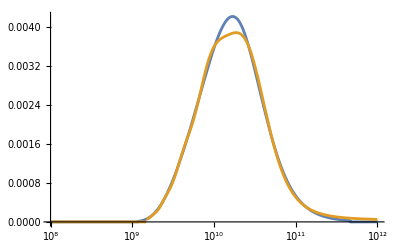

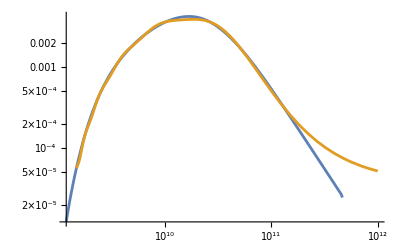

```mathematica
LogLinearPlot[{𝒩[me/(kB*Tv)],𝒩Parthenope[me/(kB*Tv)]},{Tv,10^8,10^12},PlotRange->All]
LogLogPlot[{𝒩[me/(kB*Tv)],𝒩Parthenope[me/(kB*Tv)]},{Tv,10^8,10^12},PlotRange->All]
```

We can also perform a fit in Hermite polynomials of the NEVO heating function. Just for information.

```mathematica
If[$NEVO,
Nlz[lz_]:=𝒩NEVO[FileNEVOneutrinos][Exp@lz];

(* Gram-Charlier expansion. Works better in that case *)
MyHermiteN[n_,x_]:=Expand@Simplify[HermiteH[n,x/Sqrt[2]]/Sqrt[2]^n];

Fitfun=A/(Sqrt[2Pi]σ)Exp[-(lz-μ)^2/(2σ^2)](1
+(S3/3!MyHermiteN[3, (lz-μ)/σ])
+(S4/4!MyHermiteN[4, (lz-μ)/σ])
+(S5/5! MyHermiteN[5, (lz-μ)/σ])
+(S6/6! MyHermiteN[6, (lz-μ)/σ])
+(S7/7! MyHermiteN[7, (lz-μ)/σ])
+(S8/8! MyHermiteN[8, (lz-μ)/σ])
+(S9/9! MyHermiteN[9, (lz-μ)/σ])
+(S10/10! MyHermiteN[10, (lz-μ)/σ]));
fitlzmax=1.7(*-1+2.7*);
fitlzmin=-4.3(*-1-3.*);
TableVals=Table[{lz,Nlz[lz]},{lz,fitlzmin,fitlzmax,0.01}];
Fitvals=FindFit[TableVals,Fitfun,{{A,0.01},{μ,-1},{σ,1},{S3,0},{S4,0},{S5,0},{S6,0},{S7,0},{S8,0},{S9,0},{S10,0}},lz];
NlzFit[lz_]=Fitfun/.Fitvals;
NFit[z_]:=NlzFit[Log[z]];
LogLogPlot[{𝒩NEVO[FileNEVOneutrinos][me/(kB*Tv)],𝒩Parthenope[me/(kB*Tv)],NFit[me/(kB*Tv)]},{Tv,1.2*10^9,4*10^11},PlotRange->All,Frame->True];
]
```

By construction 𝒩 is the heat rate transfered in unit of Hubble rate. Or more precisely, the volumic heat rate (the source on the r.h.s of dρ/dt equation) is dq/dt = H  (kB T)^4 𝒩 with plus sign for neutrinos and minus sign for electron/photons plasma.

See companion paper for more details in section II.F.
We transform it to a function of temperature or Log[T].

```mathematica
𝒩T[Tv_]:= 𝒩[me/(kB Tv)];
𝒩lT[lTv_]:= 𝒩[me/(kB Exp@lTv)];
```

Visualization of the heating period

```mathematica
If[$PaperPlots,LogLogPlot[𝒩T[Tv],{Tv,Ti,10^9},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"T (K)","𝒩(T)"},LabelStyle->{FontSize->12},PlotStyle->{Black,Thickness[0.003]}]]
If[$PaperPlots,Export["Plots/PlotCalN.pdf",Style[%,Magnification->1],"PDF"];]
```

```mathematica
DS2lTQED[lTv_]:=(2*2 π^2)/45 DSTQED[Exp@lTv];
DST2QED[Tv_]:=(2*2 π^2)/45 DSTQED[Tv]

DS2lTNoQED[lTv_]:=(2*2 π^2)/45 DSTNoQED[Exp@lTv];
DST2NoQED[Tv_]:=(2*2 π^2)/45 DSTNoQED[Tv]
```

We first solve  d ln(aT) / d ln(T) so as to get a(T). This is computed using the fact that there is a cooling of electron/photon plasma due to interactions with neutrinos.
We distinguish the case with and without QED corrections.

The equation solved is Eq. 62 of companion paper. SolveaOFTwhenID calls the solver and can be recalled anytime we have varied parameters.

```mathematica
SolveaOFTwhenID:=(laTCQED=NDSolveValue[{laTCN'[lTv]==(𝒩lT[lTv]-DS2lTQED'[lTv])/(𝒩lT[lTv]+3*DS2lTQED[lTv]),laTCN[Log@Tf]==Log[TCMB0/DSTQED[Tf]^(1/3)]},{laTCN},{lTv,Log@Ti,Log@Tf},PrecisionGoal->30(*40s*),AccuracyGoal->7(*9*)][[1]];

laTCNoQED=NDSolveValue[{laTCNNoQED'[lTv]==(𝒩lT[lTv]-DS2lTNoQED'[lTv])/(𝒩lT[lTv]+3*DS2lTNoQED[lTv]),laTCNNoQED[Log@Tf]==Log[TCMB0/DSTNoQED[Tf]^(1/3)]},{laTCNNoQED},{lTv,Log@Ti,Log@Tf},PrecisionGoal->30(*40*),AccuracyGoal->7(*9*)][[1]];
);
```

We call SolveaOFTwhenID at first evaluation

```mathematica
SolveaOFTwhenID
```

```mathematica
aTCQED[Tv_]:=Exp[laTCQED[Log@Tv]];
aCQED[Tv_]:=aTCQED[Tv]/Tv;
```

```mathematica
aCQED[Tf]Tf/TCMB0
aCQED[Ti]Ti/TCMB0
```

1.

0.715323

```mathematica
aTCNoQED[Tv_]:=Exp[laTCNoQED[Log@Tv]];
aCNoQED[Tv_]:=aTCNoQED[Tv]/Tv;
```

```mathematica
aCNoQED[Tf]Tf/TCMB0
```

1.

We invert numerically a(T) to obtain T(a). We also do it for z=AT as a function of a. This is operation is performed when we call the wrapping function InvertaofTwhenID.

```mathematica
InvertaofTwhenID:=
(TofaCQED=Interpolation@Table[{aCQED[T],T},{T,ListT}];
TofaCNoQED=Interpolation@Table[{aCNoQED[T],T},{T,ListT}];

aTofaCQED=Interpolation@Table[{aCQED[T],aTCQED[T]},{T,ListT}];
aTofaCNoQED=Interpolation@Table[{aCNoQED[T],aTCNoQED[T]},{T,ListT}];
);
```

We call it at first evaluation

```mathematica
InvertaofTwhenID
```

```mathematica
aC[T_]:=If[$QEDPlasmaCorrections,aCQED[T],aCNoQED[T]]
```

We now solve d (ρ_ν)/d ln(a) (we have to pay attention to units, hence the hbar and clight placed in the system).

In fact we solve for the evolution of a^4 ρ_ν as a function of Log[a]. This is Eq. 63 of companion paper. The function SolveρνOFawhenID calls the solver.

```mathematica
SolveρνOFawhenID:=(Timing[a4ρνLogaQED=NDSolveValue[{barρaNQED'[lav]==1/(hbar^3 clight^5)(kB aTofaCQED[Exp@lav])^4 𝒩T[TofaCQED[Exp@lav]],barρaNQED[Log@aCQED@Ti]==aBB (kB aTCQED[Ti])^4 7/8 Nneu},{barρaNQED},{lav,Log[aCQED[Ti]],Log[aCQED[Tf]]},(*Method->"StiffnessSwitching",*)PrecisionGoal->13,AccuracyGoal->43][[1]];];

Timing[a4ρνLogaNoQED=NDSolveValue[{barρaNNoQED'[lav]==1/(hbar^3 clight^5)(kB aTofaCNoQED[Exp@lav])^4 𝒩T[TofaCNoQED[Exp@lav]],barρaNNoQED[Log@aCNoQED@Ti]==aBB (kB aTCNoQED[Ti])^4 7/8 Nneu},{barρaNNoQED},{lav,Log[aCNoQED[Ti]],Log[aCNoQED[Tf]]},(*Method->"StiffnessSwitching",*)PrecisionGoal->13,AccuracyGoal->43][[1]];];
);
```

We call SolveρνOFawhenID at first evaluation

```mathematica
SolveρνOFawhenID
```

```mathematica
a4ρνCQED[av_]:=a4ρνLogaQED[Log@av];
ρνCQED[av_]:=a4ρνCQED[av]/av^4;
```

```mathematica
a4ρνCNoQED[av_]:=a4ρνLogaNoQED[Log@av];
ρνCNoQED[av_]:=a4ρνCNoQED[av]/av^4;
```

```mathematica
aTofaCNoQED[a[10^12]]/TCMB0
```

0.366905 InterpolatingFunction[…][a[1000000000000]]

```mathematica
(*ρνC[av_]:=If[$QEDPlasmaCorrections,ρνCQED[av],ρνCNoQED[av]];*)

ρνIncompleteDecoupling[av_]:=If[$QEDPlasmaCorrections,ρνCQED[av],ρνCNoQED[av]];
```

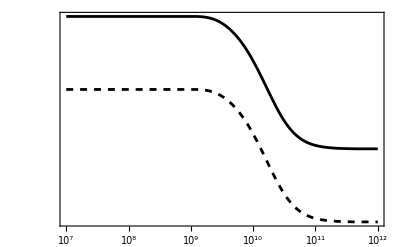

```mathematica
LogLogPlot[{a4ρνCQED[aC[Tv]],a4ρνCNoQED[aC[Tv]]},{Tv,Ti,Tf},Frame->True,PlotStyle->{Black,{Dashed,Black}}]
```

We gather all operations needed to compute incomplete neutrino decoupling. Hence the function RecomputeIncompleteNeutrinoDecoupling can be called whenever we change some parameters so as to modify the incomplete decoupling of neutrinos.

```mathematica
RecomputeIncompleteNeutrinoDecoupling:=(
If[$Verbose,Print["Computing incomplete decoupling of neutrinos."]];
SolveaOFTwhenID;
InvertaofTwhenID;
SolveρνOFawhenID;
)
```

## Neutrino Temperature

We extract the corresponding temperature of  neutrinos

For full neutrino decoupling it is easy and deduced from entropy conservation.

We choose the correct temperature ratio depending on options chosen and we build the corresponding energy density

```mathematica
TνoverTDecoupling[T_]:=(FourOverEleven DST[T])^(1/3);
ρνDecoupling[Tv_]:=aBB(kB TνoverTDecoupling[Tv]Tv)^4 7/8 Nneu;
```

When considering incomplete decoupling of neutrinos, we find the temperature variation, which is defined as a brightness temperature. See Eq. 64 of companion paper.

```mathematica
TνoverTIncompleteDecouplingQED[Tv_]:=(ρνCQED[aCQED[Tv]]/(aBB(kB Tv)^4 7/8 Nneu))^(1/4);
TνoverTIncompleteDecouplingNoQED[Tv_]:=(ρνCNoQED[aCNoQED[Tv]]/(aBB(kB Tv)^4 7/8 Nneu))^(1/4);

TνoverTIncompleteDecoupling[T_]:=If[$QEDPlasmaCorrections,TνoverTIncompleteDecouplingQED[T],TνoverTIncompleteDecouplingNoQED[T]]
```

So that now we can decide to use either the full decoupling or the incomplete decoupling neutrino temperature, depending on the options chosen

```mathematica
TνAverageoverT[T_]:=If[$IncompleteNeutrinoDecoupling,
If[$Taverage𝒩,TνoverTIncompleteDecoupling[T],If[$NEVO,TνAverageOverTγOFTγNEVOSafe[T],TνoverTIncompleteDecoupling[T]]],
TνoverTDecoupling[T]];


TνoverT[Tv_]:=If[$IncompleteNeutrinoDecoupling,
If[$TrueTνe&&$NEVO,TνeOverTγOFTγNEVOSafe[Tv],TνAverageoverT[Tv]],
TνoverTDecoupling[Tv]
 ];
```

Comparison of the two implementations of Taverage.

```mathematica
(*If[$NEVO&&$IncompleteNeutrinoDecoupling,LogLinearPlot[{TνoverTIncompleteDecoupling[Tv],TνAverageOverTγOFTγNEVOSafe[Tv]},{Tv,10^8,4*10^11},Frame->True]]*)
(*If[$NEVO&&$IncompleteNeutrinoDecoupling,LogLinearPlot[{TνoverTIncompleteDecoupling[Tv]/TνAverageOverTγOFTγNEVOSafe[Tv]-1},{Tv,10^8,4*10^11},Frame->True]]*)
```

## Effective Description of Neutrinos

We check the translation into equivalent number of neutrinos. See section II.G of companion paper for the definition of Neff.
This section is only informative.

```mathematica
TνoverTDecouplingNoQED[T_]:=(FourOverElevenNoQED* DSTNoQED[T])^(1/3);
TνoverTDecouplingQED[T_]:=(FourOverElevenQED* DSTQED[T])^(1/3);

EffectiveNeutrinosQED[Tv_]:=NeutrinosGenerations(TνoverTIncompleteDecouplingQED[Tv]/TνoverTDecouplingNoQED[Tv])^4;
EffectiveNeutrinosNoQED[Tv_]:=NeutrinosGenerations(TνoverTIncompleteDecouplingNoQED[Tv]/TνoverTDecouplingNoQED[Tv])^4;
```

z (z is defined as z=aT with the convention z=1 deep before BBN).

```mathematica
zOFTDecouplingNoQED[T_]:=(DSTNoQED[Ti]/DSTNoQED[T])^(1/3);
zOFTDecouplingQED[T_]:=(DSTQED[Ti]/DSTQED[T])^(1/3);

zOFTIncompleteDecouplingNoQED[T_]:=(aCNoQED[T]T)/(aCNoQED[Ti]Ti);
zOFTIncompleteDecouplingQED[T_]:=(aCQED[T]T)/(aCQED[Ti]Ti);
```

The various z at the end depending on the physics. See table I in companion paper.

```mathematica
zendQED=zOFTIncompleteDecouplingQED[Tf]
zendNoQED=zOFTIncompleteDecouplingNoQED[Tf]

zendDecouplingQED=zOFTDecouplingQED[Tf]
zendDecouplingNoQED=zOFTDecouplingNoQED[Tf]
(11./4)^(1/3)
```

1.39797

1.39909

1.39989

1.40102

1.40102

Effective number of neutrinos

```mathematica
EffectiveNeutrinosQED[10^8]
EffectiveNeutrinosNoQED[10^8]
3((11./4)^(1/3)/zendDecouplingQED)^4
```

3.0439

3.03416

3.00965

Neff from the neutrino energy density

```mathematica
Neff:=If[$IncompleteNeutrinoDecoupling,If[$QEDPlasmaCorrections,EffectiveNeutrinosQED[10^8],EffectiveNeutrinosNoQED[10^8]],
If[$QEDPlasmaCorrections,3((11./4)^(1/3)/zendDecouplingQED)^4,3]]
```

```mathematica
Neff
```

3.0439

The most accurate estimation of Neff, given the options chosen, is (because it uses directly the results of NEVO, and note that it requires NeutrinosGenerations=3 or whatever has been used in NEVO.):

```mathematica
Neff:=NeutrinosGenerations*(TνAverageoverT[10^8]/TνoverTDecouplingNoQED[10^8])^4
```

```mathematica
Neff
```

3.04398

z_ν at the end of integration (Only computed in the case of incomplete decoupling because otherwise it remains unity)

```mathematica
zνOFTQED[T_]:=TνoverTIncompleteDecouplingQED[T]*zOFTIncompleteDecouplingQED[T];
zνOFTNoQED[T_]:=TνoverTIncompleteDecouplingNoQED[T]*zOFTIncompleteDecouplingNoQED[T];
zνOFT[T_]:=If[$QEDPlasmaCorrections,zνOFTQED[T],zνOFTNoQED[T]]
```

```mathematica
zνendQED=zνOFTQED[10^8]
zνendNoQED=zνOFTNoQED[10^8]
```

1.00145

1.00145

The total energy density increase in neutrinos is

```mathematica
zνendQED^4
zνendNoQED^4
```

1.00583

1.00583

N_eff is by definition (z_ν z_dec/z)^4. See notation in companion paper.
So we recheck that we find the N_eff given in the companion paper in Table I.

```mathematica
3*(zνendQED *zendDecouplingNoQED/zendQED)^4
3*(zνendNoQED *zendDecouplingNoQED/zendNoQED)^4
3*(zendDecouplingNoQED/zendDecouplingQED)^4
```

3.04389

3.03415

3.00964

However, in the case we use NEVO, the expression given directly above for Neff is exactly the one computed inside NEVO itself.

```mathematica
If[$PaperPlots,ListLogLinearPlot[Table[{Tv,TνoverTIncompleteDecouplingQED[Tv]/TνoverTDecouplingQED[Tv]},{Tv,ListTRange[10^8,10^12]}],Joined->True,PlotStyle->Black,FrameStyle->Thickness[0.004],Frame->True,FrameLabel->{"T(K)","T_ν^ID / T_ν^dec"}]]
If[$PaperPlots,Export["Plots/PlotTnuvariation.pdf",Style[%,Magnification->1],"PDF"];]

If[$PaperPlots,ListLogLinearPlot[Table[{Tv,TνoverT[Tv]},{Tv,ListTRange[10^8,10^12]}],Joined->True,PlotStyle->Black,FrameStyle->Thickness[0.004],Frame->True,FrameLabel->{"T(K)","T_ν^ID / T_ν^dec"}]]
If[$PaperPlots,Export["Plots/PlotTnuOverT.pdf",Style[%,Magnification->1],"PDF"];]
```

```mathematica
If[$PaperPlots,ListLogLinearPlot[{Table[{Tv,EffectiveNeutrinosQED[Tv]},{Tv,ListTRange[10^8,10^12]}],
Table[{Tv,EffectiveNeutrinosNoQED[Tv]},{Tv,ListTRange[10^8,10^12]}],
Table[{Tv,3(zOFTDecouplingNoQED[Tv]/zOFTDecouplingQED[Tv])^4},{Tv,ListTRange[10^8,10^12]}](*,
Table[{Tv,3(zνOFT[Tv])^4},{Tv,ListTRange[10^8,10^12]}]*)},Joined->True,PlotStyle->{Black,{Red,Dashed},{Blue,Dotted}},Frame->True,FrameLabel->{"T(K)","N_eff"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{2.99,3.05}]]
If[$PaperPlots,Export["Plots/PlotNeff.pdf",Style[%,Magnification->1],"PDF"];]
```

## Scale factor - temperature relation

This is the function which gives the scale factor as a function of the temperature. 

1) If neutrino decoupling is total, then the total entropy is conserved and so it is only a function of temperature (entropy density) and scale factor (volume), since S= s a^3.So this can be solved without a differential equation in time. 
2) If Incomplete Neutrino decoupling is taken into account, we use the result aC previously obtained, that is we track the evolution of entropy, (see function SolveaOFTwhenID above).

```mathematica
a[T_]:=If[$IncompleteNeutrinoDecoupling,aC[T],TCMB0/(T DST[T]^(1/3))];
```

```mathematica
(*LogLinearPlot[{a[Tv], TCMB0/Tv},{Tv,10^9,10^10},Frame->True,FrameLabel->{"T (K)","a(T)/a_0     T_CMB0/T_CMB"}]*)
```

Just for simplicity we define again the z and z_ν variables which are z=aT and z=aT_ν respectively

```mathematica
zT[T_]:=(a[T]T)/(a[Ti]Ti);
znuT[T_]:=(a[T]TνoverT[T] T)/(a[Ti]TνoverT[Ti] Ti);
```

And again we check how they varied

```mathematica
zT[Tf]//NP
znuT[Tf]//NP
```

1.3979705

1.001753

We build a table with (a, T) so as to obtain the inverse T(a) via an interpolation. 
In the incomplete neutrino case we have already performed such inversion so there is a slight loss of time and computer energy.

```mathematica
InvertaOFT:=(Tofa=Interpolation@Table[{a[T],T},{T,ListT}];);
(*aI=Interpolation@Table[{T,a[T]},{T,ListT}];*)
```

```mathematica
InvertaOFT
```

We can check how accurate is this inversion by checking how a(T(a)) is the identity. The error is below 10^-8 so our numerics are precise enough.

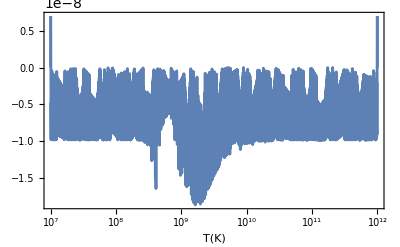

```mathematica
LogLinearPlot[{Tofa[a[T]]/T-1},{T,Ti,Tf},Frame->True,FrameLabel->{"T(K)",""}]
```

η factor with temperature dependence (because photons density has evolved due to electron positron recombination)

```mathematica
ηfactorT[Tv_]:=nB[a[Tv]]*π^2/(2Zeta[3])((hbar clight)/(kB Tv))^3;
```

Another way to  obtain this quantity

```mathematica
ηfactorTBis[Tv_]:=ηfactor*(zT[Tf]/zT[Tv])^3;
```

```mathematica
ηfactorTBis[Ti]//NP
ηfactorT[Ti]//NP
```

1.6771744×10^-9

1.6771744×10^-9

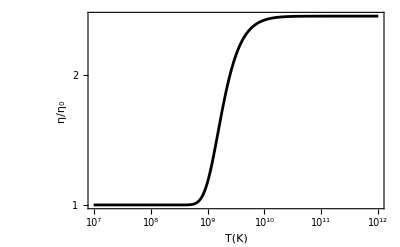

```mathematica
LogLogPlot[ηfactorT[Tv]/ηfactor,{Tv,Ti,Tf},Frame->True,FrameStyle->Thickness[0.004],PlotStyle->Black,FrameLabel->{"T(K)","η/η_0"}]
If[$PaperPlots,Export["Plots/PlotEta.pdf",Style[%,Magnification->1],"PDF"];]
```

Check of normalization. We chose that today the scale factor is unity.

```mathematica
a[Tf]Tf/TCMB0//NP
```

1.

## Cosmology and Friedmann equation (scale factor - time relation)

## Energy density

The Friedmann equation gives the Hubble expansion rate. 
For completeness we put baryons and CDM even though it makes a difference of order 10^-5 which is below what we can achieve anyway with homogeneous computations.

H^2=(8π G ρ)/3=ρ/ρ_crit so we build first the energy density.

We select the neutrino energy density depending on options for decoupling

```mathematica
ρν[T_]:=If[$IncompleteNeutrinoDecoupling,ρνIncompleteDecoupling[a[T]],ρνDecoupling[T]]+If[$SpectralDistortions,ρνSD[TνoverT[T]*T],0];
```

If relativistic species added, we must also add them

```mathematica
ρνRelat[Tv_]:=aBB(kB TνoverTDecoupling[Tv]Tv)^4 7/8 *Nrelat;(*Tν ~1/a exactly in the decoupling limit hence this corresponds to the temperature of an unkown relativistic but decoupled species *)
```

EDE energy density

```mathematica
aEDEmax :=acEDE(4/(3 wnEDE-1))^(1/(3(1+wnEDE)))
ρradamax:=aBB (kB Tv)^4(1+DρT[Tv])+ρν[Tv]+ρνRelat[Tv]/.Tv->Tofa[aEDEmax]
(*ρradac:=(Subscript[Ω, ν0]+Subscript[Ω, γ0])Subscript[ρ, crit]/aEDEmax^4*)
ρEDEac:=fEDE/(1-fEDE)ρradamax/2(1+4/(3wnEDE-1))
ρEDE[av_]:=2ρEDEac/(1+(av/acEDE)^(3(1+wnEDE)))
```

Two methods to get the total energy density. Either from energy density of neutrinos or from temperature. This should be (and it is...) totally equivalent.

```mathematica
ρtot1[T_]:=(aBB (kB T)^4(1+DρT[T])+ρν[T]+ρνRelat[T]
+nbaryons0(mbaryon0*(1+h2Ωc0/h2Ωb0)+3/2(kB T))/(clight)^2/(a[T])^3
+If[$EDEBool,ρEDE[a[T]],0]);
(* Added EDE *)
ρtot2[T_]:=(aBB (kB T)^4(1+7/8 Nneu(TνAverageoverT[T])^4+DρT[T])
+If[$SpectralDistortions,ρνSD[TνoverT[T]*T],0]+ρνRelat[T]
+nbaryons0(mbaryon0*(1+h2Ωc0/h2Ωb0)+3/2(kB T))/(clight)^2/(a[T])^3
+If[$EDEBool,ρEDE[a[T]],0]);
```

```mathematica
ρtot[T_]:=ρtot2[T]; (* If $Taverage𝒩=True, ρtot1 and ρtot2 are equivalent. In general, we prefer ρtot2 which uses the effective temperatures (better consistency).*)
```

```mathematica
ρtot2[10^10]//Timing
ρtot1[10^10]
```

{0.000369,442826.}

442829.

We check that we have the correct asymptotic behaviours for the degrees of freedom (Beware that QED corrections alter a bit the results)

```mathematica
ρtot[T]/(aBB (kB T)^4)/.T->10^12//NP
(2+4*7/8+3*2*7/8)/2//N//NP
```

5.3683834

5.375

```mathematica
ρtot[T]/(aBB (kB T)^4)/.T->10^7.5//NP
(2+3*2*7/8*(FourOverEleven)^(4/3))/2//N//NP
```

1.6918036

1.6835124

We plot the energy density as a function of temperature.

```mathematica
If[$PaperPlots,ListLogLogPlot[Table[{T,1/T^4ρtot[T]},{T,ListT}],Frame->True,Joined->True,PlotStyle->Black,FrameLabel->{"T (K)","T^-4ρ(T)    g cm^-3K^-4"}]]
If[$PaperPlots,Export["Plots/PlotρT.pdf",Style[%,Magnification->1],"PDF"];]
```

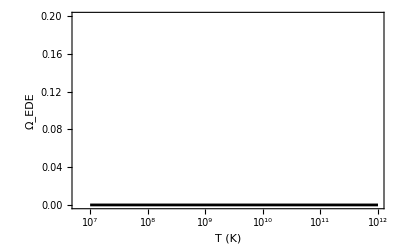

```mathematica
ListLogLinearPlot[{Table[{T,ρEDE[a[T]]/ρtot[T]},{T,ListT}]},Frame->True,Joined->True,PlotStyle->{Black,{Black,Dashed}},FrameLabel->{"T (K)","Ω_EDE"},PlotRange->{0,0.2}]
Export["Plots/OEDE.pdf",Style[%,Magnification->1],"PDF"];
```

## Hubble rate and scale factor

Hubble function from Friedmann equation in flat FL space-time is then immediate

```mathematica
HofT[T_]:=((8π GN)/3 ρtot[T])^(1/2);

H[a_]:=HofT[Tofa[a]];(*((8π GN)/3 ρtot[Tofa[a]])^(1/2);*)
```

This is the solver for dt/da giving t(a). Direct integration of the Friedmann equation

```mathematica
Computetofa:=(tofa=(NDSolveValue[{tv'[av]==1/(av H[av]),tv[a[Ti]]==1/(2H[a[Ti]])},tv,{av,a[Ti],a[Tf]},PrecisionGoal->8,AccuracyGoal->10]);)
```

We check that it is quick enough.

```mathematica
Timing@Computetofa
```

{0.031202,Null}

This is the solver for the inverse function, that is for da/dt, giving a(t)

```mathematica
Computeaoft:=(aoft=NDSolveValue[{av'[tv]==1/tofa'[av[tv]],av[tofa@a[Ti]]==a[Ti]},av,{tv,tofa@a[Ti],tofa@a[Tf]},PrecisionGoal->13,AccuracyGoal->25];)
```

We check that it is quick enough.

```mathematica
Timing@Computeaoft
```

{0.055118,Null}

We also check that computing  a(t(a)) gives negligible error to identity. It is of order 10^-9 so we are totally OK.

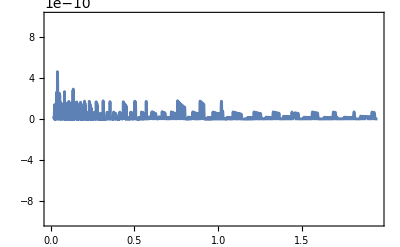

```mathematica
Plot[1/av*aoft@tofa@av-1,{av,a[Ti],a[Ti]*100},PlotRange->{-10^-9,10^-9},Frame->True]
```

We define the temperature as a function of time. Since we have T(a) (conserved entropy) and a(t) (Friedman equation), we just combine both.
In case of incomplete decoupling of neutrinos, we could not use conservation of entropy to get T(a) but we used the fit for the heating rate which allowed us to obtain numerically T(a) and a(T).

```mathematica
Toft[tv_]:=Tofa[aoft[tv]];
```

## Weak reactions n+ν ↔ p+e

## Distribution functions derivatives

These Fermi-Dirac function and its derivatives are needed further. en stands for energy. x for 1/(k_B T). 

FDeipj means that it is the Fermi Dirac distribution multiplied by Energy^i and derived j times wrt to Energy. See Def B25 in companion paper.

```mathematica
FDνe2p0[en_,ϕ_,x_]=Simplify[FDν[en,ϕ,x]en^2];
FDνe3p0[en_,ϕ_,x_]=Simplify[FDν[en,ϕ,x]en^3];
FDνe2p2[en_,ϕ_,x_]=Simplify[D[D[FDν[en,ϕ,x]en^2,en],en]];

FDνe3p2[en_,ϕ_,x_]=Simplify[D[D[FDν[en,ϕ,x]en^3,en],en]];
FDνe4p2[en_,ϕ_,x_]=Simplify[D[D[FDν[en,ϕ,x]en^4,en],en]];
FDνe2p1[en_,ϕ_,x_]=Simplify[D[FDν[en,ϕ,x]en^2,en]];
FDνe3p1[en_,ϕ_,x_]=Simplify[D[FDν[en,ϕ,x]en^3,en]];
FDνe4p1[en_,ϕ_,x_]=Simplify[D[FDν[en,ϕ,x]en^4,en]];
```

## λ_0

### Born approximation λ_0

See e.g. Eq. 13 of [Lopez & Turner 1998]. Or Eq. 92 of companion paper.

The constant λ_0 is a proxy for  τ_n^-1= λ_0* [cos^2(θ_c)G_F^2(C_V^2+3 C_A^2)/(2 π^3) ]

```mathematica
λBORN:=λBORN=With[{q=Q/me},NIntegrate[en(en-q)^2 √(en^2-1),{en,1,q}]]
```

### Corrections to λ_0

#### Radiative corrections to λ_0

1) If $ResummedLogsRadiativeCorrections=False, we use Eq. 7 of  [Czarnecki et al. 2004] which is B30 of companion paper.
 Combined with Eq 20b of [Sirlin 1967] for Sirlin’s universal function, that is Eq. B32 in companion paper.

```mathematica
AgCzarnecki=-0.34;
CCzarnecki=0.891;
mA=1.2 GeV;
ConstantSirlin =4Log[Subscript[m, Z]/mp]+Log[mp/mA]+2CCzarnecki+AgCzarnecki;
```

For information, this quantity is evaluated to 40 in [Dicus et al.]

```mathematica
ConstantSirlin+3Log[mp/(me)]-3/4
```

41.2988

```mathematica
Rd[x_]:=ArcTanh[x]/x;
```

NB : ArcTanh[x] = 1/2 Log[(1+x)/(1-x)]

```mathematica
Lfun:=Lfun=Function[{x},Evaluate[Integrate[Log[1-t]/t,{t,0,x},Assumptions->x<1&&x>0]]](* Lfun is called the Spence function *)
```

It can be computed from a Taylor expansion (this used to be done in the past), but a direct evaluation by Mathematica is much better

```mathematica
Clear[LfunSeries]
LfunSeries:=LfunSeries=Function[{b},Evaluate[Normal@Series[-1/4*(1+b)^6*4/b Lfun[(2b)/(1+b)],{b,0,12(*22*)}]]]
```

Sirlin universal function (Eq 20b of [Sirlin 1967]) on which we add the constants of Eq. 7 of  [Czarnecki et al. 2004]) is obtained as (this is B32 of companion paper)

```mathematica
$SeriesSpenceFunction=False;

SirlinGFunction[b_,y_,en_]:=(3Log[mp/(me)]-3/4+4(Rd[b]-1)(y/(3 en)-3/2+Log[2y])+Rd[b](2(1+b^2)+y^2/(6 en^2)-4 b Rd[b])+If[$SeriesSpenceFunction,-4/(1+b)^6*LfunSeries[b],4/b Lfun[(2b)/(1+b)]]);
Cd[b_,y_,en_]:=(ConstantSirlin+SirlinGFunction[b,y,en]);
```

NB : In [Dicus et al. 1982] Eq 2.14 (or in [Lopez&Turner 1998] Eq. 17) they use the approximation  4/b Lfun[(2b)/(1+b)]= -4(2+11b+224/9 b^2+89/3 b^3+1496/75 b^4+596/75 b^5+128/49 b^6)/(1+b)^6  
However there is a typo and some incorrect coefficients. In [Kernan] there are approximate coefficients which are nearly correct.

2) if $ResummedLogsRadiativeCorrections = True, we use a resummed version of all the Log[m_Z/m_P]. It consists in using Eq. 15 of [Czarnecki 2004] or B35 in companion paper.
See also [Esposito et al. 1998])

We build the multiplicative factor for inner radiative corrections (Eq. 15 of [Czarnecki et al. 2004]), that is B35 of companion paper.

```mathematica
LFactor=1.02094;
SFactor=1.02248;
δfactor=-0.00043*2Pi/αFS;
NLL=-0.0001;
```

```mathematica
RadiativeCorrectionsResummed[b_,y_,en_]:=(1+αFS/(2π)(SirlinGFunction[b,y,en]-3Log[mp/(2Q)]))*
(LFactor+αFS/π CCzarnecki+αFS/(2π)δfactor)*(SFactor+1/(134*2*Pi)*(Log[mp/mA]+AgCzarnecki)+NLL);
```

Finally we define a function which selects either choice depending on option

```mathematica
RadiativeCorrections[b_,y_,en_]:=If[$ResummedLogsRadiativeCorrections,RadiativeCorrectionsResummed[b,y,en],(1+αFS/(2π)Cd[b,y,en])]
```

Fermi function for Coulomb interactions of electron and proton (if on the same side of the interaction).
Either the relativistic or the non-relativistic depending on option $RelativisticFermiFunction. That is either Eq. 99 or Eq. 100 of companion paper depending on option chosen.

```mathematica
FermiRelat[b_]:=With[{γ=Sqrt[1-αFS^2]-1,λCompton=1/(me/(hbar clight))},
(1+γ/2)*4((2radiusproton b)/λCompton)^(2γ)*1/Gamma[3+2γ]^2 Exp[(π αFS)/b]*1/((1-b^2)^γ)Abs[Gamma[1+γ+I αFS/b]]^2];

FermiNonRelat[b_]:=(2π αFS/b)/(1-Exp[-2π αFS/b]);
```

```mathematica
If[$RelativisticFermiFunction,

Fermi[b_]:=FermiRelat[b];
bFermi[b_]:=b Fermi[b];,

Fermi[b_]:=FermiNonRelat[b];
bFermi[b_]:=(2π αFS)/(1-Exp[-2π αFS/b]);]
```

```mathematica
If[$PaperPlots,DFermi=Plot[{100*(FermiRelat[b]/FermiNonRelat[b]-1)},{b,0,1},Frame->True,FrameStyle->Thickness[0.004],PlotStyle->{Black},FrameLabel->{"x","100 x (F^rel(x)/F^(non rel)(x) -1)"},LabelStyle->{FontSize->12}]]
If[$PaperPlots,Export["Plots/PlotDeltaFermi.pdf",Style[DFermi,Magnification->1],"PDF"];];
```

λ_0 when taking only Fermi function and not radiative corrections

```mathematica
λFermiOnly:=λFermiOnly=With[{q=Q/me ,b=√(en^2-1)/en,y=Q/me -en},
NIntegrate[en(en-q)^2 en*bFermi[b],{en,1.0000001,q}]]
```

This already a 3.44 % correction

```mathematica
λFermiOnly/(λBORN)
```

1.03438

Adding the inner radiative corrections, the constant involved in the decay of the neutron is

```mathematica
λRad:=λRad=With[{q=Q/me ,b=√(en^2-1)/en,y=Q/me -en},
NIntegrate[en(en-q)^2 en(RadiativeCorrections[b,y,en])*bFermi[b],{en,1.0000001,q}]]
```

Note that in companion paper, Eq. 106, the value 1.75767 is quoted when it should be the value found here 1.758384.

```mathematica
λRad
```

1.75838

This adds another 3.90 % correction as found in Eq 16 of [Czarnecki et al. 2004].

```mathematica
λRad/λFermiOnly//Timing
```

{7.×10^-6,1.03903}

#### Finite mass corrections to λ_0

See companion papers for expression of finite nucleon mass corrections. 
We take the general form of finite mass correction and remove all terms which involve temperature. So we consider Eq. 118 of companion paper.

```mathematica
IntegrateCorrectionNeutronDecay[fun_]:=
NIntegrate[fun[pe],{pe,0.0000001,√((Q/me)^2-1)},WorkingPrecision->15];
```

```mathematica
χFMNeutronDecay[en_,pe_]:=
With[{M=mn/me,enu=en-Q/me,f1=((1+gA)^2+4 fWM gA)/(1+3 gA^2),f2=((1-gA)^2-4fWM gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},
 f1*enu^2(pe^2/(M*en))
+f2*enu^3(-1/M)
+(f1+f2+f3)1/(2M)*(4 enu^3+2enu pe^2)
+f3*1/(3M)3 enu^2 pe^2/(en)
];
```

Without coupling to radiative corrections we get

```mathematica
IλFMBasic[pe_]:=With[{en=Sqrt[pe^2+1]},With[{b=pe/en},pe^2*
(χFMNeutronDecay[en,pe])
]];
```

```mathematica
IntegrateCorrectionNeutronDecay[IλFMBasic]/λBORN
```

-0.00206478

However we couple to radiative corrections if $CoupledFMandRC = True

```mathematica
IλFM[pe_]:=With[{en=√(pe^2+1)},With[{b=pe/en},pe^2*
(χFMNeutronDecay[en,pe]*If[$RadiativeCorrections&&$CoupledFMandRC,(RadiativeCorrections[b,Abs[en- Q/me ],en])Fermi[b],1])
]];
```

```mathematica
λFM:=λFM=If[$FiniteNucleonMass,IntegrateCorrectionNeutronDecay[IλFM],0]
```

```mathematica
λFM
```

-0.00362834063730089

When taking only into account Fermi function and finite mass effect on should get 1.6887. See Eq. 6 of [Czarnecki et al. 2004]

```mathematica
λFermiOnly+λFM
1.6887/%//NP
```

1.68871

0.99999283

We compare the correction to the Born result

```mathematica
CorrectionRate=λFM/λBORN
```

-0.00221768

If Coulomb and Radiative corrections are set to False (0) this is exactly (-0.00206) what is found by [Lopez & Turner 1997] (see three lines after Eq. 23, in the text). 
See also the value -0.00201 found in Eq. 20 of [Seckel 1993].

We also reproduce for comparison the exact finite mass correction to the neutron decay rate as computed by Eq. 19 of [Lopez & Turner 1998], which uses two-dimensional integrals. Again we find the -0.00206 correction so our finite mass method based one-dimensional integrals is reliable.

```mathematica
λexact:=λexact=With[{pe=Sqrt[en^2-1]},With[{enu=((mn^2-mp^2)/me^2+1-2mn/me en)/(2(mn/me-en+pe Cnu))},
With[{Ep=mn/me-enu-en,f1=((1+gA)^2+4fWM gA)/(1+3 gA^2),f2=((1-gA)^2-4fWM gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},With[{J=1+(enu+ pe Cnu)/(Ep),M2=f1 mn/me enu (Ep en-(-pe^2-pe enu Cnu))+f2 mn/me en (Ep enu-(-pe enu Cnu-enu^2))+f3 mn/me  Ep(enu en-Cnu enu pe) },NIntegrate[1/2*M2 pe enu/(mn/me  Ep J),{en,1,(Q-(Q^2-me^2)/(2mn))/me },{Cnu,-1,1},PrecisionGoal->10(*,Method->{Automatic,"SymbolicProcessing"->0}*)]
]]]];
```

```mathematica
(λexact-λBORN)/λBORN//NP
```

-0.0020636787

#### Total correction

The total correction for the neutron decay constant λ_0 is the sum of the Radiative corrected one plus the finite mass effects

We recall the result from radiative corrections (again we stress that Eq. 106 in companion paper should report that value).

```mathematica
λRad
```

1.75838

The result from mass corrections (see text before  Eq. 120 in companion paper.)

```mathematica
λFM
```

-0.00362834063730089

And we sum them to get Eq. 120 of companion paper.

```mathematica
λRadandFM:=λRad+λFM
```

This gives a total correction which is

```mathematica
λRadandFM/λBORN
```

1.07253

If we compare with [Cooper et al 2010] (Phys. Rev. C 81, 035503 (2010)). They find that this parameter should be

```mathematica
λCooper=1.03887*1.6887
λCzarnecki=1.0390*1.6887 (* = (1+RC)*f with f=1.6887 and RC = 0.0390(8) [Czarnecki et al. 2004]] *)
```

1.75434

1.75456

We compute the ratio to see how far we are

```mathematica
λRadandFM/λCooper
λRadandFM/λCzarnecki
```

1.00024

1.00011

We check that it is in agreement with the theoretical formula. This expression below should reproduce the neutron decay time. It is amazingly close !

```mathematica
MixingCosAngle=0.97420;(*  0.97420(+-16) from PDG2017 (The review on Vud Vus of the PDG 2017).*)
(*The value from PDG2020 review on Vud Vus is 0.97370(+-20) but this brings tension on the unitarity of the CKM matrix. Hence we stick to the previous value. This is only used to check if one recovers from theory the neutrino lifetime.*)
MyK:=MyK=MixingCosAngle^2(GF)^2(1+3(gA)^2)me^5/(2 π^3 hbar)
```

```mathematica
1/MyK/λRadandFM
1/MyK/λCzarnecki
1/MyK/λCooper
```

879.388

879.487

879.597

Indeed with the PDG2017 value of Vud, we recover  τneutron  ~ 879.4 or so hence we feel that the neutron lifetime value is not a much more solid ground than what it was in the pas.

Let us also compare with Eq. 17 of [Czarnecki et al. 2004] to check how close we are in including all corrections. See text after Eq. 120 in companion paper as well.

```mathematica
ConstantVud=hbar*(2 π^3)/(me)^5/(GF)^2/λRadandFM
ConstantVud2=hbar*(2 π^3)/(me )^5/(GF)^2/λCzarnecki
ConstantVud3=hbar*(2 π^3)/(me )^5/(GF)^2/λCooper
```

4907.38

4907.93

4908.54

## Born rates

We compute in this section the Born rates for n -> p and p -> n.

Tools to perform integration on electron momentum

```mathematica
pemin=0.00001;
pemiddle[x_]:=Sqrt[Max[pemin^2,(Q/me )^2-1 -If[$QEDMassShift,dme2x[x],0]]];
pemaxC[x_]:=Max[12,30/x];
pemax[x_]:=Max[12,30/x];
```

$TnuEqualT is some cheat to check detailed balance. Should be False. When it is True neutrinos have always the plasma temperature.

```mathematica
$TnuEqualT=False;
```

```mathematica
IntegratedpNpoints[fun_,sgnq_,Tv_,Npoints_]:=With[{x=me/(kB Tv) ,znu=me/(kB Tv TνoverT[Tv]) },
If[$FastPENRatesIntegrals,
IntegrateFunction[fun[#,x,If[$TnuEqualT,x,znu],sgnq]&,pemin,pemaxC[x],Npoints],
NIntegrate[fun[pe,x,If[$TnuEqualT,x,znu],sgnq],{pe,pemin,pemiddle[x],pemax[x]}]
]]

IntegrateRatedp[fun_,sgnq_,Tv_]:=IntegratedpNpoints[fun,sgnq,Tv,$PENRatesIntegralsPoints];
```

Energy as a function of momentum, taking into account QED mass shifts. 
This is only used if the option is set to True but it is useless because it is taken into account in finite temperature corrections

```mathematica
enOFpe[pe_,x_]:=Sqrt[pe^2+1 +If[$QEDMassShift,dme2x[x],0]];
```

Functions to build integrands in electron momentum. Without and with CCR corrections. This is then passed to the integrating routine IntegrateRatedp.

```mathematica
IPENdpFromχNoCCR[en_,pe_,x_,znu_,sgnq_,χfunction_]:=With[{q=Q/me },With[{b=pe/en},
pe^2*(χfunction[en,pe,x,znu,sgnq]+χfunction[-en,pe,x,znu,sgnq])
]];
```

```mathematica
Fermi[sgnq_,signE_,b_?NumericQ]:=If[sgnq signE >0,Fermi[b],1];
SetAttributes[Fermi,Listable];
```

```mathematica
IPENdpFromχCCR[en_,pe_,x_,znu_,sgnq_,χfunction_]:=With[{q=Q/me ,b=pe/en},
pe^2*(χfunction[en,pe,x,znu,sgnq](RadiativeCorrections[b,Abs[sgnq Q/me-en],en])Fermi[sgnq,1,b]+χfunction[-en,pe,x,znu,sgnq](RadiativeCorrections[b, Abs[sgnq Q/me+en],en])Fermi[sgnq,-1,b])
];
```

Eq 2.29 in [Brown & Sawyer] for the Born approximation. It is Eq. 79 of companion paper

```mathematica
χ[en_,pe_,x_,znu_,sgnq_]:=With[{q=Q/me },FDν[en-sgnq q,sgnq ξν,znu]FD[-en,x](en-sgnq q)^2];
```

Eq 2.30 in [Brown & Sawyer], that is the integration of Eq. 78 in companion paper

```mathematica
IPENdp[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χ]
```

We also define a function which is incorrect in which we force the neutrinos to have the temperature of photons. This is to check detailed balance. Indeed, detailed balance is satisfied only if all species have the same temperature.

```mathematica
IPENdpCheatNeutrinoTemperature[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[Sqrt[pe^2+1],pe,x,x,sgnq,χ]
```

Born rates are given by Eq 2.30 in [Brown & Sawyer].

```mathematica
λnTOpBORN[Tv_]:=IntegrateRatedp[IPENdp,1,Tv];
λpTOnBORN[Tv_]:=IntegrateRatedp[IPENdp,-1,Tv];
```

Born rates where the neutrino temperature is cheated to be equal to photons temperature are then given by

```mathematica
λnTOpBORNCheatNeutrino[Tv_]:=IntegrateRatedp[IPENdpCheatNeutrinoTemperature,1,Tv];
λpTOnBORNCheatNeutrino[Tv_]:=IntegrateRatedp[IPENdpCheatNeutrinoTemperature,-1,Tv];
```

## Spectral distortions of neutrino spectrum

Shift in the weak rates due to spectral distortions of neutrino distribution functions.

```mathematica
δχ[en_,pe_,x_,znu_,sgnq_]:=With[{q=Q/me },dFDneu[en-sgnq q,sgnq ξν,x,znu,sgnq]FD[-en,x](en-sgnq q)^2];
```

We add this spectral distortions effect at the Born approximation level.

```mathematica
(* Spectral distortions with Born approximation*)
IPENdpSD[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,δχ]
IPENdpSDCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,δχ]

λnTOpSD[Tv_]:=IntegrateRatedp[IPENdpSD,1,Tv];
λpTOnSD[Tv_]:=IntegrateRatedp[IPENdpSD,-1,Tv];
λnTOpSDCCR[Tv_]:=IntegrateRatedp[IPENdpSDCCR,1,Tv];
λpTOnSDCCR[Tv_]:=IntegrateRatedp[IPENdpSDCCR,-1,Tv];
```

## Finite mass effects

For finite mass effects, we use a (Fokker-Planck) expansion which leads to one-dimensional integrals.
We include also the weak-magnetism which is important indeed. This is B23 of companion paper.

```mathematica
χFM[en_,pe_,x_,znu_,sgnq_]:=
With[{ϕ=sgnq ξν,q=Q/me ,M=(mp+mn -sgnq Q)/(2me ),Mp=mp/me ,Mn=mn /me ,enu=en-sgnq Q/me,
f1=((1+sgnq gA)^2+4fWM sgnq gA)/(1+3 gA^2),
f2=((1-sgnq gA)^2-4fWM sgnq gA)/(1+3 gA^2),f3=(gA^2-1)/(1+3 gA^2)},
f1*FDνe2p0[enu,ϕ,znu]FD[-en,x](pe^2/(M*en))
+f2*FDνe3p0[enu,ϕ,znu]FD[-en,x](-1/M)
+(f1+f2+f3)1/(2x M)*(FDνe4p2[enu,ϕ,znu]FD[-en,x]+FDνe2p2[enu,ϕ,znu]FD[-en,x] pe^2)
+(f1+f2+f3)1/(2M)*(FDνe4p1[enu,ϕ,znu]FD[-en,x]+FDνe2p1[enu,ϕ,znu]FD[-en,x] pe^2)
-(f1+f2)1/(x M)*(FDνe3p1[enu,ϕ,znu]FD[-en,x]+FDνe2p1[enu,ϕ,znu]FD[-en,x]pe^2/(-en))
-f3*3/(x M)FDνe2p0[enu,ϕ,znu]FD[-en,x](* This term seems to give very small corrections *)
+f3*1/(3M)FDνe3p1[enu,ϕ,znu]FD[-en,x] pe^2/(en)
+f3*2/(2 x*3M)FDνe3p2[enu,ϕ,znu]FD[-en,x] pe^2/(en)
-(f1+f2+f3)*3/(2x)*(1-(Mn/Mp)^sgnq)*(FDνe2p1[enu,ϕ,znu]FD[-en,x])(* Note that this last line is different from the published version of the Physics Report where there is a typo.*)
];
```

Integrand for finite mass corrections. We couple it to radiative corrections.

```mathematica
IPENdpFMNoCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χFM]
IPENdpFMCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χFM]
```

Integrand for finite mass corrections when neutrinos are forced to have the same temperature as photons.

```mathematica
IPENdpFMCheatNeutrinoTemperature[pe_,x_,znu_,sgnq_]:=IPENdpFromχNoCCR[enOFpe[pe,x],pe,x,x,sgnq,χFM]
```

```mathematica
Clear[λnTOpFMCCR,λpTOnFMCCR,λnTOpFMNoCCR,λpTOnFMNoCCR,λnTOpCheatNeutrinoFM,λpTOnCheatNeutrinoFM]
```

Finite mass corrections using the λ_0 which is corrected with radiative corrections. The computation below implements Eqs. 114 of companion paper.

```mathematica
λnTOpFMCCR[Tv_]:=IntegrateRatedp[IPENdpFMCCR,1,Tv];
λpTOnFMCCR[Tv_]:=IntegrateRatedp[IPENdpFMCCR,-1,Tv];
```

Finite mass corrections using the λ_0 which is computed with the Born infinite mass expression (we do not advise to use it).

```mathematica
λnTOpFMNoCCR[Tv_]:=IntegrateRatedp[IPENdpFMNoCCR,1,Tv];
λpTOnFMNoCCR[Tv_]:=IntegrateRatedp[IPENdpFMNoCCR,-1,Tv];
```

Finite mass corrections cheating with the neutrino temperature and setting it equal to photons temperature

```mathematica
λnTOpCheatNeutrinoFM[Tv_]:=IntegrateRatedp[IPENdpFMCheatNeutrinoTemperature,1,Tv];
λpTOnCheatNeutrinoFM[Tv_]:=IntegrateRatedp[IPENdpFMCheatNeutrinoTemperature,-1,Tv];
```

Examples of neutron decay corrections for some low temperatures:

```mathematica
Off[General::munfl];
```

```mathematica
λnTOpFMCCR[10^8]/λnTOpBORN[10^8]//Timing
λnTOpFMCCR[10^7.5]/λnTOpBORN[10^7.5]//Timing
```

I load compiled function from lib/V1dotV2.mx and the library linked is lib/V1dotV2.dylib

{0.011505,-0.00223931}

{0.024112,-0.00222579}

```mathematica
λnTOpFMCCR[.8 10^10]/λnTOpBORN[.8 10^10]//Timing
λnTOpFMCCR[10^10]/λnTOpBORN[10^10]//Timing
λnTOpFMCCR[10^10.5]/λnTOpBORN[10^10.5]//Timing
```

{0.004162,-0.00914668}

{0.003917,-0.010909}

{0.003873,-0.0305405}

```mathematica
λnTOpFMCCR[10^11]
λpTOnFMCCR[10^11]

λnTOpFMCCR[10^10]
λpTOnFMCCR[10^10]

λnTOpFMCCR[6.061*10^9]
λpTOnFMCCR[6.061*10^9]
```

-6.21854×10^6

-5.22208×10^6

-12.7424

-2.06767

-0.957784

-0.0390473

```mathematica
λnTOpFMCCR[4.024*10^7]
λpTOnFMCCR[4.02456*10^7]
```

-0.00364497

1.27071×10^-169

```mathematica
On[General::munfl];
```

### Plots of the finite mass corrections

We plot the amplitude of the finite mass corrections. This is essentially similar to Fig 8.1 of [Kernan] but the result is a little different since here we have put all the finite nucleon mass effects, and [Kernan] did not.

```mathematica
If[$PaperPlots,
TabδλFMnTOp=Table[{T,(λnTOpFMCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T]*(τneutron λBORN)^-1)},{T,ListTRange[10^9,10^11]}];
TabδλFMpTOn=Table[{T,(λpTOnFMCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T]*(τneutron λBORN)^-1)},{T,ListTRange[10^9,10^11]}];

TFreeze=0.8 MeV/kB;

PlotdeltaGammaFM=Show[ListLogLinearPlot[{TabδλFMnTOp,TabδλFMpTOn},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{-10^-1,10^-2},FrameLabel->{"T (K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Black,Thickness[0.003]},{Black,Dashing[{0.01}],Thickness[0.003]}},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},FrameTicks->MyFrameTicksLog],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-.1,-0.06}],90 Degree]}]]
]
If[$PaperPlots,Export["Plots/PlotdeltaGammaFM.pdf",Style[PlotdeltaGammaFM,Magnification->1],"PDF"];];
```

```mathematica
If[$PaperPlots,TabδλFMnTOp2=Table[{T,Identity[(λnTOpFMCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T]*(τneutron λBORN)^-1)]},{T,ListTRange[5 10^8,10^10.5]}];
TabδλFMpTOn2=Table[{T,Identity[(λpTOnFMCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T]*(τneutron λBORN)^-1)]},{T,ListTRange[5 10^8,10^10.5]}];

PlotdeltaGammaFM2=Show[ListPlot[{TabδλFMnTOp2,TabδλFMpTOn2},Frame->True,FrameStyle->Thickness[0.004],Joined->True,PlotRange->{-3*10^-2,10^-2},FrameLabel->{"T (10^10K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Red,Thickness[0.003]},{Blue,Dashing[{0.01}],Thickness[0.003]}},FrameTicks->{{Automatic,Automatic},{{{0.5*10^10,".5"},{10^10,"1"},{1.5*10^10,"1.5"},{2 10^10,"2"},{2.5 10^10,"2.5"}},Automatic}},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{TFreeze 0.93,-0.02}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotdeltaGammaFM2.pdf",Style[PlotdeltaGammaFM2,Magnification->1],"PDF"];];
```

### Checking detailed balance

Born approximation detailed balance checks.

```mathematica
DetailedBalanceRatio0[T_]:=Exp[-Q/(kB T)-ξν];
```

At Born order, detailed balance is of course satisfied by construction.

```mathematica
DetailedBalance0[T_]:=(λnTOpBORN[T])/(λpTOnBORN[T])*DetailedBalanceRatio0[T];
DetailedBalanceCheatNeutrino0[T_]:=(λnTOpBORNCheatNeutrino[T])/(λpTOnBORNCheatNeutrino[T])*DetailedBalanceRatio0[T];
```

If we enforce T_ν=T the precision is insane. It is numerical precision because detailed balance is rooted in our method.

```mathematica
If[$PaperPlots,
ListLogLinearPlot[{Table[{T,DetailedBalanceCheatNeutrino0[T]-1},{T,ListTRange[10^9,10^12]}]},Joined->True,PlotStyle->{Black,{Black,Dashed}},Frame->True]
]
```

Including corrections in Q/mp,detailed balance is given by (where α should be set to 0).

```mathematica
DetailedBalanceRatio[T_]:=Exp[-Q/(kB T)-ξν](1+(1+α)Q/mp)^(3/2);
```

[Lopez&Turner 1997] define some quantity to parameterize how good detailed balance is obtained, this is the parameter α. 
α should be 0 so we use it to estimate the failure of detailed balance

We first solve for α correctly, and then we do it when forcing the temperature of neutrinos to be the one of photons, in which case detailed balance must be true. Indeed if we do not force the temperature of neutrinos to be the one of photons, then it is only true before electrons/positrons annihilate, and at low temperature detailed balance is not satisfied.

```mathematica
Clear[αLopez,αLopezCheatNeutrino]
αLopez[T_]:=αLopez[T]=α/.Solve[Normal@Series[(λnTOpBORN[T]+λnTOpFMNoCCR[T])/(λpTOnBORN[T]+λpTOnFMNoCCR[T])*DetailedBalanceRatio[T],{α,0,1}]==1,α][[1]]

αLopezCheatNeutrino[T_]:=αLopezCheatNeutrino[T]=α/.Solve[Normal@Series[(λnTOpBORNCheatNeutrino[T]+λnTOpCheatNeutrinoFM[T])/(λpTOnBORNCheatNeutrino[T]+λpTOnCheatNeutrinoFM[T])*DetailedBalanceRatio[T],{α,0,1}]==1,α][[1]]
```

We plot something similar to Fig. 4 of [Lopez&Turner 1997]. The remaining error should come from second order corrections. For instance at low temperature it remains an effect of order  (Q/mn )^2 so α is expected to differ from a null value by something of order Q/mn =0.002. We also see that below 5x10^10 K, detailed balance does not work because neutrinos no longer have the temperature of photons but it works if we force neutrinos to be at the temperature of photons.

```mathematica
If[$PaperPlots,PlotDetailedBalance=Show[ListLogLinearPlot[{Table[{T,αLopez[T]},{T,ListTRange[10^8.5,10^11.5]}],Table[{T,αLopezCheatNeutrino[T]},{T,ListTRange[10^8.5,10^11.5]}]},Frame->True,FrameTicks->MyFrameTicksLog,GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},Joined->True,FrameLabel->{"T (K)","α"},FrameStyle->Thickness[0.003],LabelStyle->{FontSize->12},PlotRange->{-1,1},PlotStyle->{{Red},{Black,Dashed,Blue}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-0.2,0.5}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotDetailedBalance.pdf",Style[PlotDetailedBalance,Magnification->1],"PDF"];];
```

## Radiative Corrections (T=0)

The CCR corrected rates are described in details in the companion paper. 

When electron and protons are on the same side we use the Fermi function to apply the Coulomb corrections.

For all processes the radiative correction are a factor (1+α/(2π)C), (similarly to Eq. 18 of [Lopez&Turner 1998] or Eq. 2.13 of [Dicus .et. al]) as described in companion paper.

```mathematica
IPENdpCCR[pe_,x_,znu_,sgnq_]:=IPENdpFromχCCR[enOFpe[pe,x],pe,x,If[$TnuEqualT,x,znu],sgnq,χ]
```

```mathematica
λnTOpCCR[Tv_]:=IntegrateRatedp[IPENdpCCR,1,Tv];
λpTOnCCR[Tv_]:=IntegrateRatedp[IPENdpCCR,-1,Tv];
```

### Plots of the radiative corrections

```mathematica
If[$PaperPlots,TabδλnTOp=Table[{T,(λnTOpCCR[T]*(τneutron λRadandFM)^-1)/(λnTOpBORN[T](τneutron λBORN)^-1)-1},{T,ListTRange[10^8.5,10^10.5]}];
TabδλpTOn=Table[{T,(λpTOnCCR[T]*(τneutron λRadandFM)^-1)/(λpTOnBORN[T](τneutron λBORN)^-1)-1},{T,ListTRange[10^8.5,10^10.5]}];

PlotdeltaGammaCCR=Show[ListLogLinearPlot[{TabδλnTOp,TabδλpTOn},Frame->True,FrameStyle->Thickness[0.004],Joined->True,FrameLabel->{"T (K)","δΓ/Γ"},LabelStyle->{FontSize->12},PlotStyle->{{Red},{Blue,Dashing[{0.01}]}},GridLines->{{{TFreeze,{Gray,Thickness[0.004]}}},{}},FrameTicks->{{Automatic,Automatic},{{{Log[10^8.5],"10^8.5"},{Log[10^9],"10^9"},{Log[10^9.5],"10^9.5"},{Log[10^10],"10^10"},{Log[10^10.5],"10^10.5"},{Log[10^11],"10^11"}},Automatic}}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-0.1,-0.01}],90 Degree]}]]
]

If[$PaperPlots,Export["Plots/PlotdeltaGammaCCR.pdf",Style[PlotdeltaGammaCCR,Magnification->1],"PDF"];];

(*ListPlot[{TabδλnTOp,TabδλpTOn},Frame->True,Joined->True,FrameLabel->{"T (K)","δΓ/Γ"},PlotStyle->{Black,{Black,Dashing[{0.01}]}}]
Export["Plots/NoLogPlotdeltaGammaCCR.pdf",Style[%,Magnification->1],"PDF"];*)
```

## Finite-temperature Radiative Corrections

### Method

We use exclusively [Brown&Sawyer] for the finite temperature radiative corrections, 
but the equation are gathered and summarized in companion paper essentially in section III.F and related appendix. The various terms are in Eq. 108.
Note also that on top of that, we also need to add what we called Brehmstrahlung corrections (Eqs. 107 in companion paper)

### Real photons processes integrand

Bose Einstein distribution function (and if sq = -1 it is stimulated emission)

```mathematica
BEQ[en_,sq_]:=sq BE[sq en];
```

χ̃ is defined in companion paper in Eq. B45.

```mathematica
χtilde[en_,znu_,sgnq_]:=With[{q=Q/me },FDν[en-sgnq q,sgnq ξν,znu](en-sgnq q)^2]
```

We first compute real photons processes (absorption or stimulated emission)
We put Fermi function everywhere to be consistent.
The integrand is (Eq. 109 of companion paper)

```mathematica
IPENCCRT[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1]},With[{b=p/en,A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π)*(BE[x k]/k)*(A(FD[-en,x]Fermi[sgnq,1,b](χtilde[en-k,znu,sgnq]+χtilde[en+k,znu,sgnq]-2χtilde[en,znu,sgnq])+FD[en,x]Fermi[sgnq,-1,b](χtilde[-en+k,znu,sgnq]+χtilde[-en-k,znu,sgnq]-2χtilde[-en,znu,sgnq]))
-k B *(FD[-en,x]Fermi[sgnq,1,b](χtilde[en-k,znu,sgnq]-χtilde[en+k,znu,sgnq])+FD[en,x]Fermi[sgnq,-1,b](χtilde[-en+k,znu,sgnq]-χtilde[-en-k,znu,sgnq]))
)
]];

(* Compiled version to compute the integrals slightly faster *)
IPENCCRTC:=IPENCCRTC=MyCompile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[IPENCCRT[en,k,x,znu,sgnq]]];IPENCCRTCN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENCCRTC[en,k,x,znu,sgnq]
```

Bremsstrahlung corrections (needed to obtain all real photons processes and eventually detailed balance).
The integrand is (Eqs. B48 and B49 using definitions B41)

```mathematica
Clear[IPENCCRDiffBremsstrahlungCN,IPENCCRDiffBremsstrahlungC,IPENCCRDiffBremsstrahlung]
IPENCCRDiffBremsstrahlung[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1],q=Q/me},With[{b=p/en,A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},With[{Fp=A+k B,Fm=A-k B},
αFS/(2π k)((FD[-en,x]Fermi[sgnq,1,b](Fp χtilde[en+k,znu,sgnq]-If[k<Abs[en-sgnq q],Fp FD[en-sgnq q,znu](Abs[en-sgnq q]-k)^2,0]))
+(FD[en,x]Fermi[sgnq,-1,b](Fm χtilde[-en+k,znu,sgnq]-If[k<Abs[en+sgnq q],Fp FD[-en-sgnq q,znu](Abs[en+sgnq q]-k)^2,0]))
)
]]];

(* We compile for the integration *)
IPENCCRDiffBremsstrahlungC:=IPENCCRDiffBremsstrahlungC=MyCompile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[IPENCCRDiffBremsstrahlung[en,k,x,znu,sgnq]]];IPENCCRDiffBremsstrahlungCN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENCCRDiffBremsstrahlungC[en,k,x,znu,sgnq]
```

The expression IPENFiveBodyT0 implements the integrand of 5.21 of [Brown&Sawyer] (and not 5.20. Careful).
We showed in companion paper that this is only a part of the bremsstrahlung corrections needed.

```mathematica
IPENFiveBodyT0[en_,k_,x_,znu_,sgnq_]:=With[{p=Sqrt[en^2-1]},With[{A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π k)(FD[en,x])χtilde[-en+k,znu,sgnq](A-k B)]]


(* Compiled version *)
IPENFiveBodyT0C:=IPENFiveBodyT0C=Compile[{{en,_Real},{k,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[With[{p=Sqrt[en^2-1]},With[{A=(2 en^2+k^2)Log[(en+p)/(en-p)]-4 p en,B=2 en Log[(en+p)/(en-p)]-4p},
αFS/(2π k)(-BE[-k x])*(FD[en,x])χtilde[-en+k,znu,sgnq](A-k B)]]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];
IPENFiveBodyT0CN[en_?NumericQ,k_,x_,znu_,sgnq_]:=IPENFiveBodyT0C[en,k,x,znu,sgnq]
```

### Mass shift and pe+ee integrand

We finally consider the mass shift and ep + ee corrections

We split the contributions of the last two terms of 5.14 in [Brown and Sawyer] in two parts. 
Indeed these are given by 5.15 [Brown and Sawyer]. The first part has only one integral, while the second part has two integrals.
The integrand of first part with only one integral is C1dE, and the integrand of the second part with two integrals is C2dE1dE2 (see 5.16 [Brown and Sawyer]).

This is the simple integration in Eq. B50a of companion paper (more precisely the integrand and the integration itself is performed further below)

```mathematica
C1dE[en_,x_,znu_,sgnq_]:=With[{pe=√(en^2-1),q=Q/me },-(αFS en)/(2π pe)*(2 π^2)/(3 x^2)(χ[en,pe,x,znu,sgnq]+χ[-en,pe,x,znu,sgnq])];
```

NB : L is given by 5.18 [Brown and Sawyer]

And this is the double integration integrand of Eq.B50a of companion paper

```mathematica
C2dE1dE2[e1_,e2_,x_,znu_,sgnq_]:=With[{p1=√(e1^2-1),p2=√(e2^2-1),q=Q/me },With[{L=Log[(e1 e2 +p1 p2 +1)/(e1 e2 -p1 p2 +1)]},
αFS/(2π)(χ[e1,p1,x,znu,sgnq]+χ[-e1,p1,x,znu,sgnq])
*(-1/4 Log[((p1+p2)/(p1-p2))^2]^2*(FDp[e2,x] p2/p1 e1^2/e2(e1+e2)+FD[e2,x] e1^2/(p1 p2)(e2+e1/e2^2))
+Log[((p1+p2)/(p1-p2))^2](FDp[e2,x](p2^2 e1/e2(1/p1^2+2)-e1^2 p2/p1 L)+FD[e2,x](e1/(p1^2 e2^2)(e2^2+2 p1^2+1)-(e1^2+e2^2)/(e1+e2)-(e1^2 e2)/(p1 p2) L))
-FD[e2,x](4 e1 p2/p1+2 e2 L))
]];


(* Compiled version *)
C2dE1dE2C:=C2dE1dE2C=Compile[{{e1,_Real},{e2,_Real},{x,_Real},{znu,_Real},{sgnq,_Integer}},Evaluate[With[{p1=√(e1^2-1),p2=√(e2^2-1),q=Q/me },With[{L=Log[(e1 e2 +p1 p2 +1)/(e1 e2 -p1 p2 +1)]},
αFS/(2π)(χ[e1,p1,x,znu,sgnq]+χ[-e1,p1,x,znu,sgnq])
*(-1/4 Log[((p1+p2)/(p1-p2))^2]^2*(FDp[e2,x] p2/p1 e1^2/e2(e1+e2)+FD[e2,x] e1^2/(p1 p2)(e2+e1/e2^2))
+Log[((p1+p2)/(p1-p2))^2](FDp[e2,x](p2^2 e1/e2(1/p1^2+2)-e1^2 p2/p1 L)+FD[e2,x](e1/(p1^2 e2^2)(e2^2+2 p1^2+1)-(e1^2+e2^2)/(e1+e2)-(e1^2 e2)/(p1 p2) L))
-FD[e2,x](4 e1 p2/p1+2 e2 L))
]]],"RuntimeOptions"->"Speed",CompilationTarget->"C"];
C2dE1dE2CN[e1_?NumericQ,e2_?NumericQ,x_,znu_,sgnq_]:=C2dE1dE2C[e1,e2,x,znu,sgnq];
```

### Integrations on momenta

We perform all integrations now that we have expressed their integrands.

TruePhoton -> real photon processes 
Diffbremsstrahlung -> bremsstrahlung corrections 
Thermal -> mass shift and pe+ee corrections

Let us start with n -> p processes

```mathematica
Clear[λnTOpThermal,λnTOpThermalTruePhoton,λpTOnThermalTruePhoton,λnTOp5bodies,λpTOnThermal,λnTOpThermalDiffBremsstrahlung,λpTOnThermalDiffBremsstrahlung]
```

```mathematica
λnTOpThermalTruePhoton[Tv_]:=(*λnTOpThermalTruePhoton[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRTCN[en,k,x,If[$TnuEqualT,x,znu],1],{k,0.001,Max[10,20/x]},{en,1.001,Max[10,20/x]},PrecisionGoal->4]
];

λnTOpThermalDiffBremsstrahlung[Tv_]:=(*λnTOpThermalDiffBremsstrahlung[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRDiffBremsstrahlungCN[en,k,x,If[$TnuEqualT,x,znu],1],{en,1.001,Max[10,20/x]},{k,0.001,Abs[en-q],Abs[en+q],Max[10,20/x]},PrecisionGoal->4]
];
```

The global 1/2 factor is Jacobian of the change of variables (we integrate in the sum and difference of energies).

```mathematica
λnTOpThermal[Tv_]:=(*λnTOpThermal[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[C1dE[en,x,If[$TnuEqualT,x,znu],1],{en,1,Max[25,150/x]}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],1],{e1me2,-Max[10,15/x],-0.001},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3,Exclusions->{0}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],1],{e1me2,0.001,Max[10,15/x]},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
];
```

The 5 body is just for comparison with [Brown & Sawyer]

```mathematica
λnTOp5bodies[Tv_]:=(*λnTOp5bodies[Tv]=*)With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENFiveBodyT0CN[en,k,x,If[$TnuEqualT,x,znu],1],{en,1,Max[20,20/x]},{k,en+q,en+q+Max[20,20/x]},PrecisionGoal->4]
];
```

Let us finish with p -> n processes

When we have computed the corrections to n -> p rates, the converse are obtained from detailed balance arguments. That is we perform the replacement Q -> -Q as argued in [Brown&Sawyer]. This is also explained in details in the companion paper.

```mathematica
λpTOnThermalTruePhoton[Tv_]:=(*λpTOnThermalTruePhoton[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRTCN[en,k,x,If[$TnuEqualT,x,znu],-1],{k,0.001,Max[10,20/x]},{en,1.001,Max[10,20/x]},PrecisionGoal->4]
]];

λpTOnThermalDiffBremsstrahlung[Tv_]:=(*λpTOnThermalDiffBremsstrahlung[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[IPENCCRDiffBremsstrahlungCN[en,k,x,If[$TnuEqualT,x,znu],-1],{en,1.001,Max[10,20/x]},{k,0.001,Abs[en-q],Abs[en+q],Max[10,20/x]},PrecisionGoal->4]
]];


λpTOnThermal[Tv_]:=(*λpTOnThermal[Tv]=*)If[Tv<10^8.2 (* When the temperature is too low it is better to put 0 *),0,
With[{x=me/(kB Tv),znu=me/(kB Tv TνoverT[Tv]),q=Q/me },
NIntegrate[C1dE[en,x,If[$TnuEqualT,x,znu],-1],{en,1,Max[25,150/x]}]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],-1],{e1me2,-Max[10,15/x],-0.001},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
+NIntegrate[1/2C2dE1dE2CN[(e1pe2+e1me2)/2,(e1pe2-e1me2)/2,x,If[$TnuEqualT,x,znu],-1],{e1me2,0.001,Max[10,15/x]},{e1pe2,2.001+Abs[e1me2],2+Abs[e1me2]+Max[10,15/x]},PrecisionGoal->3]
]];
```

### Collecting all finite-temperature corrections

We collect the various contributions of Eq. 108. The TruePhoton contribution refers to the first term on the rhs of Eq. 108, and the Thermal contribution to the second and third. The Bremsstrahlung corrections are Eqs. 107.

```mathematica
λnTOpCCRTh[Tv_]:=(λnTOpThermal[Tv]+λnTOpThermalTruePhoton[Tv]+If[$CorrectionBremsstrahlung,λnTOpThermalDiffBremsstrahlung[Tv],λnTOp5bodies[Tv]]);

λpTOnCCRTh[Tv_]:=(λpTOnThermal[Tv]+λpTOnThermalTruePhoton[Tv]+If[$CorrectionBremsstrahlung,λpTOnThermalDiffBremsstrahlung[Tv],0]);
```

We gather all corrections according to the Booleans chosen at the beginning

```mathematica
λ0:=If[$RadiativeCorrections,λRad,λBORN]+If[$FiniteNucleonMass,λFM,0]
```

## Gathering all corrections

For info the normalized rates are :

```mathematica
λnTOpNormalizedSDCCR[Tv_]:=(λ0)^-1 λnTOpSDCCR[Tv];
λpTOnNormalizedSDCCR[Tv_]:=(λ0)^-1 λpTOnSDCCR[Tv];
λnTOpNormalizedSD[Tv_]:=(λ0)^-1 λnTOpSD[Tv];
λpTOnNormalizedSD[Tv_]:=(λ0)^-1 λpTOnSD[Tv];
λnTOpNormalizedCCR[Tv_]:=(λ0)^-1 λnTOpCCR[Tv];
λpTOnNormalizedCCR[Tv_]:=(λ0)^-1 λpTOnCCR[Tv];
λnTOpNormalizedBORN[Tv_]:=(λ0)^-1 λnTOpBORN[Tv];
λpTOnNormalizedBORN[Tv_]:=(λ0)^-1 λpTOnBORN[Tv];
```

We add them depending on options chosen

```mathematica
Clear[λnTOp,λpTOn,λnTOpNormalized,λpTOnNormalized];
λnTOpNormalized[Tv_]:=(λ0)^-1(
If[$RadiativeCorrections,λnTOpCCR[Tv],λnTOpBORN[Tv]]
+If[$RadiativeThermal,λnTOpCCRTh[Tv],0]
+If[$SpectralDistortions,If[$RadiativeCorrections,λnTOpSDCCR[Tv],λnTOpSD[Tv]],0]
+If[$FiniteNucleonMass,If[$CoupledFMandRC,λnTOpFMCCR[Tv],λnTOpFMNoCCR[Tv]],0]
);

λpTOnNormalized[Tv_]:=(λ0)^-1(
If[$RadiativeCorrections,λpTOnCCR[Tv],λpTOnBORN[Tv]]
+If[$RadiativeThermal,λpTOnCCRTh[Tv],0]
+If[$SpectralDistortions,If[$RadiativeCorrections,λpTOnSDCCR[Tv],λpTOnSD[Tv]],0]
+If[$FiniteNucleonMass,If[$CoupledFMandRC,λpTOnFMCCR[Tv],λpTOnFMNoCCR[Tv]],0]);
```

```mathematica
Clear[λnTOp]
λnTOp[Tv_]:=1/τneutron λnTOpNormalized[Tv];
λpTOn[Tv_]:=1/τneutron λpTOnNormalized[Tv];
```

Detailed balance check

```mathematica
Tt=10^10.8;
(λnTOpThermalTruePhoton[Tt]+1λnTOpThermalDiffBremsstrahlung[Tt])/(λpTOnThermalTruePhoton[Tt]+1λpTOnThermalDiffBremsstrahlung[Tt])
(*LnTOp[Tt]/LpTOn[Tt]*)
λnTOpCCR[Tt]/λpTOnCCR[Tt]
λnTOpBORN[Tt]/λpTOnBORN[Tt]
λnTOpThermal[Tt]/λpTOnThermal[Tt]
Exp[Q/kB/Tt]
```

1.26851

1.26854

1.26854

1.26855

1.26854

Effect of spectral distortions on the rates : relative variations wrt to the rate without them. This plot depends on which spectral distortions have been chosen above. If none, it is identically zero.

```mathematica
(*listT=ListTRange[10^9,10^11.5][[1;; ;;10]];(*We take only 10% of points to get the plot faster. Otherwise it takes a bit longer.*)
ListLogLinearPlot[{Table[{T,λnTOpSDCCR[T]/λnTOpNormalized[T]},{T,listT}],Table[{T,λpTOnSDCCR[T]/λpTOnNormalized[T]},{T,listT}]},Joined->True,Frame->True,FrameStyle->Thickness[0.003],LabelStyle->{FontSize->10},FrameLabel->{"T (K)","δΓ/Γ"},PlotStyle->{{Red,Thickness[0.003]},{Blue,Thickness[0.003]}}]*)
```

## Precomputation and storage of rates

We store the rate but without the division by τneutron . So that we can use the same fit for the reaction rates, and still vary τneutron .

The rates in the files, once loaded, are interpolated once the division by τneutron  has been added.
If spectral distortions are taken into account, we could avoid ParallelComputation because it seems it loses time in sharing the big interpolation. 
TODO maybe there is a solution to that.

```mathematica
MyTableWeakRate:=If[$ParallelWeakRates(*&&Not[$SpectralDistortions]*),
(*Something does not work when we use NEVO. Some definitions seem not to be distributed correctly.*)
DistributeDefinitions[λnTOpNormalized,λpTOnNormalized,LoadNEVO,LoadDistortions,TableNEVOLoaded[FileNEVOneutrinos],TableNEVOLoaded[FileNEVOantineutrinos],TreatNEVOFile];
ParallelEvaluate[Off[NIntegrate::slwcon];];
ParallelTable,
Table]
```

```mathematica
ComputeWeakRates:=Module[{time},
Off[NIntegrate::slwcon];
Off[General::munfl ];
Off[NIntegrate::izero];
If[$RecomputeWeakRates,Print["The $RecomputeWeakRates option forces a recomputation of weak rates."]];
Print["Computing weak rates for n<->p conversions."];
time=Timing[TabRatenp=MyTableWeakRate[{T,λnTOpNormalized[T]},{T,ListT}];
TabRatepn=MyTableWeakRate[{T,λpTOnNormalized[T]},{T,ListT}];][[1]];
If[$Verbose,Print["Time spent in (re)computing weak rates was ",time," s"];];

Export[NamePENFilenp,TabRatenp,"TSV"];
Export[NamePENFilepn,TabRatepn,"TSV"];
On[General::munfl ];On[NIntegrate::slwcon];On[NIntegrate::izero];]
```

```mathematica
LoadWeakRates:=(
If[Not@FileExistsQ[NamePENFilenp]||Not@FileExistsQ[NamePENFilepn]||$RecomputeWeakRates,
ComputeWeakRates;,

If[$Verbose,Print["Loading weak rates for n<->p conversions."];];
TabRatenp=Import[NamePENFilenp,"TSV"];
TabRatepn=Import[NamePENFilepn,"TSV"];
];
λnTOpI=MyInterpolationRate[ToExpression[TabRatenp]];
λpTOnI=MyInterpolationRate[ToExpression[TabRatepn]];
);
```

```mathematica
LoadWeakRates
```

Loading weak rates for n<->p conversions.

We give standard names that are used in the network of reactions later. The factor 1/τ_n is the one appearing in the constant defined in Eq. 91 of companion paper.

```mathematica
LnTOp[Tv_]:=1/τneutron*λnTOpI[Tv];
LpTOn[Tv_]:=1/τneutron*λpTOnI[Tv];
LbarnTOp[Tv_]:=LpTOn[Tv];
```

We check that the rate for neutron decay is what we expect at low temperature, that is it is τneutron  only. At 10^8 K it should be the case.

```mathematica
1/LnTOp[Tf]
τneutron
```

878.382

878.4

## Freeze - out estimations

```mathematica
Tfreeze1=FindRoot[{LnTOp[T]==HofT[T]},{T,10^10}][[1,2]]
Tfreeze2=FindRoot[{LnTOp[T]+LpTOn[T]==(Exp[Q/(kB T)]/(1+Exp[Q/(kB T)]))Q/(kB T)HofT[T]},{T,10^10}][[1,2]]
```

8.28739×10^9

8.92816×10^9

## Nuclear reactions network

## Nuclear Species

### Names and (N,Z)

The is the list of short names with their (neutron, proton) weights. So by definition a neutron has (1, 0) and a proton has (0, 1) and He4 has (2, 2) and so on.

```mathematica
NamesWithWeightsAll={{"n",{1,0}},{"p",{0,1}},{"d",{1,1}},{"t",{2,1}},
{"He3",{1,2}},{"a",{2,2}},{"Li7",{4,3}},{"Be7",{3,4}},{"He5",{3,2}},
{"He6",{4,2}},{"Li6",{3,3}},{"Li8",{5,3}},{"Li9",{6,3}},
{"Be8",{4,4}},{"Be9",{5,4}},{"Be10",{6,4}},{"Be11",{7,4}},{"Be12",{8,4}},
{"B8",{3,5}},{"B9",{4,5}},{"B10",{5,5}},{"B11",{6,5}},{"B12",{7,5}},{"B13",{8,5}},{"B14",{9,5}},{"B15",{10,5}},
{"C9",{3,6}},{"C10",{4,6}},{"C11",{5,6}},{"C12",{6,6}},{"C13",{7,6}},{"C14",{8,6}},{"C15",{9,6}},{"C16",{10,6}},
{"N12",{5,7}},{"N13",{6,7}},{"N14",{7,7}},{"N15",{8,7}},{"N16",{9,7}},{"N17",{10,7}},
{"O13",{5,8}},{"O14",{6,8}},{"O15",{7,8}},{"O16",{8,8}},{"O17",{9,8}},{"O18",{10,8}},{"O19",{11,8}},{"O20",{12,8}},
{"F17",{8,9}},{"F18",{9,9}},{"F19",{10,9}},{"F20",{11,9}},
{"Ne18",{8,10}},{"Ne19",{9,10}},{"Ne20",{10,10}},{"Ne21",{11,10}},{"Ne22",{12,10}},{"Ne23",{13,10}},
{"Na20",{9,11}},{"Na21",{10,11}},{"Na22",{11,11}},{"Na23",{12,11}}};
```

Let us vizuallize the nuclides used in as a table in (Z,N).

```mathematica
TableNZNucleons=Table[" ",{i,0,13},{j,0,11}];
Map[(TableNZNucleons[[Sequence@@(#[[2]]+{1,1})]]=#[[1]])&,NamesWithWeightsAll];
```

```mathematica
Grid[Transpose@TableNZNucleons,Frame->All](* This is table III in companion paper*)
```

| n |   |   |   |   |   |   |   |   |   |   |   |  
p | d | t |   |   |   |   |   |   |   |   |   |   |  
  | He3 | a | He5 | He6 |   |   |   |   |   |   |   |   |  
  |   |   | Li6 | Li7 | Li8 | Li9 |   |   |   |   |   |   |  
  |   |   | Be7 | Be8 | Be9 | Be10 | Be11 | Be12 |   |   |   |   |  
  |   |   | B8 | B9 | B10 | B11 | B12 | B13 | B14 | B15 |   |   |  
  |   |   | C9 | C10 | C11 | C12 | C13 | C14 | C15 | C16 |   |   |  
  |   |   |   |   | N12 | N13 | N14 | N15 | N16 | N17 |   |   |  
  |   |   |   |   | O13 | O14 | O15 | O16 | O17 | O18 | O19 | O20 |  
  |   |   |   |   |   |   |   | F17 | F18 | F19 | F20 |   |  
  |   |   |   |   |   |   |   | Ne18 | Ne19 | Ne20 | Ne21 | Ne22 | Ne23
  |   |   |   |   |   |   |   |   | Na20 | Na21 | Na22 | Na23 |

The list of the species names only

```mathematica
ShortNamesAll=NamesWithWeightsAll[[All,1]];
```

The list of {n, p} pairs only.

```mathematica
ListNPPairs=NamesWithWeightsAll[[All,2]];
```

Functions to check if a name exists

```mathematica
ExistName[name_]:=MemberQ[ShortNamesAll,name];
ExistPair[pair_List]:=MemberQ[ListNPPairs,pair];
```

This function selects the names of the species which all have the same mass number A

```mathematica
NamesMassNumberAll[A_]:=Select[NamesWithWeightsAll,((Plus@@(#[[2]]))==A)&][[All,1]]
```

### Dictionaries between names and numbers

We define dictionaries to handle species. We associate a number to each species
It is a simple correspondance between names and position of the species in the list, or between the names and the pair (neutron,proton).

```mathematica
KeySpecies=Association@(Rule@@@NamesWithWeightsAll)
```

<|n→{1,0},p→{0,1},d→{1,1},t→{2,1},He3→{1,2},a→{2,2},Li7→{4,3},Be7→{3,4},He5→{3,2},He6→{4,2},Li6→{3,3},Li8→{5,3},Li9→{6,3},Be8→{4,4},Be9→{5,4},Be10→{6,4},Be11→{7,4},Be12→{8,4},B8→{3,5},B9→{4,5},B10→{5,5},B11→{6,5},B12→{7,5},B13→{8,5},B14→{9,5},B15→{10,5},C9→{3,6},C10→{4,6},C11→{5,6},C12→{6,6},C13→{7,6},C14→{8,6},C15→{9,6},C16→{10,6},N12→{5,7},N13→{6,7},N14→{7,7},N15→{8,7},N16→{9,7},N17→{10,7},O13→{5,8},O14→{6,8},O15→{7,8},O16→{8,8},O17→{9,8},O18→{10,8},O19→{11,8},O20→{12,8},F17→{8,9},F18→{9,9},F19→{10,9},F20→{11,9},Ne18→{8,10},Ne19→{9,10},Ne20→{10,10},Ne21→{11,10},Ne22→{12,10},Ne23→{13,10},Na20→{9,11},Na21→{10,11},Na22→{11,11},Na23→{12,11}|>

We have a reverse dictionary if we want

```mathematica
KeyNucleons=Association@(Rule@@@(Reverse/@NamesWithWeightsAll))
```

<|{1,0}→n,{0,1}→p,{1,1}→d,{2,1}→t,{1,2}→He3,{2,2}→a,{4,3}→Li7,{3,4}→Be7,{3,2}→He5,{4,2}→He6,{3,3}→Li6,{5,3}→Li8,{6,3}→Li9,{4,4}→Be8,{5,4}→Be9,{6,4}→Be10,{7,4}→Be11,{8,4}→Be12,{3,5}→B8,{4,5}→B9,{5,5}→B10,{6,5}→B11,{7,5}→B12,{8,5}→B13,{9,5}→B14,{10,5}→B15,{3,6}→C9,{4,6}→C10,{5,6}→C11,{6,6}→C12,{7,6}→C13,{8,6}→C14,{9,6}→C15,{10,6}→C16,{5,7}→N12,{6,7}→N13,{7,7}→N14,{8,7}→N15,{9,7}→N16,{10,7}→N17,{5,8}→O13,{6,8}→O14,{7,8}→O15,{8,8}→O16,{9,8}→O17,{10,8}→O18,{11,8}→O19,{12,8}→O20,{8,9}→F17,{9,9}→F18,{10,9}→F19,{11,9}→F20,{8,10}→Ne18,{9,10}→Ne19,{10,10}→Ne20,{11,10}→Ne21,{12,10}→Ne22,{13,10}→Ne23,{9,11}→Na20,{10,11}→Na21,{11,11}→Na22,{12,11}→Na23|>

N, Z, A from name

```mathematica
Ni["Bm"]:=1;
Ni["Bp"]:=-1;
Ni["g"]:=0;

Zi["Bm"]:=-1;
Zi["Bp"]:=1;
Zi["g"]:=0;

Ai["Bm"]:=0;
Ai["Bp"]:=0;
Ai["g"]:=0;
```

```mathematica
Ni[key_]:=KeySpecies[key][[1]]
Zi[key_]:=KeySpecies[key][[2]]
Ai[key_]:=Zi[key]+Ni[key]
```

```mathematica
Ai["Li7"]
Ni["Li7"]
Zi["Li7"]
Ni["Bm"]
```

7

4

3

1

### Binding energies and spins of nuclei

Tools to reshape the file "nubase2016.asc"

```mathematica
SpinFromCharList[charlist_List]:=StringReplace[StringJoin@@charlist,{"("->"",")"->"",","->"","+"->"","-"->""," "->"","#"->"","*"->""}]
MassFromCharList[charlist_List]:=StringReplace[StringJoin@@charlist,{" "->"","#"->""}]
```

**OLD method : Nubase 2016. New methods with NUbase 2020 below**

We load the file "nubtab06.asc" OLD Method. Now we prefere to load nubase 2020 from the file nubase_4.mas20.txt, see below.

NUBASE 2016 Syntax :
  The first three characters of each line are the A . 
   Characters from 5 to 7 are Z (but the 8th character is a number for a possibel excited state. Hence we use character 5 to 8 for 10*Z, and then divide by 10. If it is an integer it is not an excited state. Otherwise it is discarded. This is a dirty hack)
  From 20 to 29 it is mass excess .
  From 80 to 93 it is some information on spin and parity .

```mathematica
(*StringListParticles=#[[1]]&/@Import["nubase2016.asc","TSV"];
NubTabChar=Select[Characters/@StringListParticles,Length[#]≥93&];*)
```

```mathematica
(*Alist=ToExpression/@StringJoin/@(Take[#,{1,3}]&/@NubTabChar);
Zlist=#/10&/@ToExpression/@StringJoin/@(Take[#,{5,8}]&/@NubTabChar);
MassExcessesString=MassFromCharList/@(Take[#,{20,29}]&/@NubTabChar);
Spins=SpinFromCharList/@(Take[#,{80,93}]&/@NubTabChar);
Nlist=Alist-Zlist;*)
```

```mathematica
(*MyGrid[ListNPBindingSpinName=Flatten[{KeyNucleons[{#[[1]],#[[2]]}],#}]&/@Select[Transpose[{Nlist,Zlist,MassExcessesString,Spins}],ExistPair[{#[[1]],#[[2]]}]&]]*)
```

We prefer using the most recent nubase (2020) (see comments about mass database at the top of this notebook) from the file nubase_4.mas20.txt  (Chinese Physics C 45 (2021) 030001).

```mathematica
StringListParticles=Drop[#[[1]]&/@Import["nubase_4.mas20.txt","TSV"],25];
NubTabChar=Select[Characters/@StringListParticles,Length[#]≥93&];
```

NUBASE 2020 Syntax :
The first three characters of each line are the A. 
Characters from 5 to 7 are Z (but the 8th character is a number for a possible excited state. Hence we use character 5 to 8 for 10*Z, and then divide by 10. If it is an integer it is not an excited state. Otherwise it is discarded. This is a dirty hack)
From 19 to 31 it is mass excess.
From 89 to 102 it is some information on spin and parity.

```mathematica
Alist=ToExpression/@StringJoin/@(Take[#,{1,3}]&/@NubTabChar);
Zlist=#/10&/@ToExpression/@StringJoin/@(Take[#,{5,8}]&/@NubTabChar);
MassExcessesString=MassFromCharList/@(Take[#,{19,31}]&/@NubTabChar);
Spins=SpinFromCharList/@(Take[#,{89,93}]&/@NubTabChar);
Nlist=Alist-Zlist;
```

We gather all this information in a list (ListNPBindingSpinName) that we print as a Table here for readbility.

```mathematica
MyGrid[ListNPBindingSpinName=Flatten[{KeyNucleons[{#[[1]],#[[2]]}],#}]&/@Select[Transpose[{Nlist,Zlist,MassExcessesString,Spins}],ExistPair[{#[[1]],#[[2]]}]&]]
```

n | 1 | 0 | 8071.3181 | 1/2
p | 0 | 1 | 7288.971064 | 1/2
d | 1 | 1 | 13135.722895 | 1
t | 2 | 1 | 14949.81090 | 1/2
He3 | 1 | 2 | 14931.21888 | 1/2
a | 2 | 2 | 2424.91587 | 0
He5 | 3 | 2 | 11231 | 3/2
He6 | 4 | 2 | 17592.10 | 0
Li6 | 3 | 3 | 14086.8804 | 1
Li7 | 4 | 3 | 14907.105 | 3/2
Be7 | 3 | 4 | 15769.00 | 3/2
Li8 | 5 | 3 | 20945.80 | 2
Be8 | 4 | 4 | 4941.67 | 0
B8 | 3 | 5 | 22921.6 | 2
Li9 | 6 | 3 | 24954.91 | 3/2
Be9 | 5 | 4 | 11348.45 | 3/2
B9 | 4 | 5 | 12416.5 | 3/2
C9 | 3 | 6 | 28911.0 | 3/2
Be10 | 6 | 4 | 12607.49 | 0
B10 | 5 | 5 | 12050.611 | 3
C10 | 4 | 6 | 15698.67 | 0
Be11 | 7 | 4 | 20177.17 | 1/2
B11 | 6 | 5 | 8667.708 | 3/2
C11 | 5 | 6 | 10649.40 | 3/2
Be12 | 8 | 4 | 25077.8 | 0
B12 | 7 | 5 | 13369.4 | 1
C12 | 6 | 6 | 0.0 | 0
N12 | 5 | 7 | 17338.1 | 1
B13 | 8 | 5 | 16561.9 | 3/2
C13 | 7 | 6 | 3125.0093 | 1/2
N13 | 6 | 7 | 5345.48 | 1/2
O13 | 5 | 8 | 23115 | 3/2
B14 | 9 | 5 | 23664 | 2
C14 | 8 | 6 | 3019.893 | 0
N14 | 7 | 7 | 2863.4168 | 1
O14 | 6 | 8 | 8007.781 | 0
B15 | 10 | 5 | 28957 | 3/2
C15 | 9 | 6 | 9873.1 | 1/2
N15 | 8 | 7 | 101.4381 | 1/2
O15 | 7 | 8 | 2855.6 | 1/2
C16 | 10 | 6 | 13694 | 0
N16 | 9 | 7 | 5683.9 | 2
O16 | 8 | 8 | -4737.0021 | 0
N17 | 10 | 7 | 7870 | 1/2
O17 | 9 | 8 | -808.7642 | 5/2
F17 | 8 | 9 | 1951.70 | 5/2
O18 | 10 | 8 | -782.8163 | 0
F18 | 9 | 9 | 873.1 | 1
Ne18 | 8 | 10 | 5317.6 | 0
O19 | 11 | 8 | 3332.9 | 5/2
F19 | 10 | 9 | -1487.4451 | 1/2
Ne19 | 9 | 10 | 1752.05 | 1/2
O20 | 12 | 8 | 3796.2 | 0
F20 | 11 | 9 | -17.463 | 2
Ne20 | 10 | 10 | -7041.9322 | 0
Na20 | 9 | 11 | 6850.5 | 2
Ne21 | 11 | 10 | -5731.78 | 3/2
Na21 | 10 | 11 | -2184.86 | 3/2
Ne22 | 12 | 10 | -8024.716 | 0
Na22 | 11 | 11 | -5181.39 | 3
Ne23 | 13 | 10 | -5154.05 | 5/2
Na23 | 12 | 11 | -9529.8535 | 3/2

We define a dictionary for excess masses (in keV)

```mathematica
ExcessMassKeys=Association[{#[[1]]->ToExpression[#[[4]]]}&/@ListNPBindingSpinName]
```

<|n→8071.32,p→7288.97,d→13135.7,t→14949.8,He3→14931.2,a→2424.92,He5→11231,He6→17592.1,Li6→14086.9,Li7→14907.1,Be7→15769.,Li8→20945.8,Be8→4941.67,B8→22921.6,Li9→24954.9,Be9→11348.5,B9→12416.5,C9→28911.,Be10→12607.5,B10→12050.6,C10→15698.7,Be11→20177.2,B11→8667.71,C11→10649.4,Be12→25077.8,B12→13369.4,C12→0.,N12→17338.1,B13→16561.9,C13→3125.01,N13→5345.48,O13→23115,B14→23664,C14→3019.89,N14→2863.42,O14→8007.78,B15→28957,C15→9873.1,N15→101.438,O15→2855.6,C16→13694,N16→5683.9,O16→-4737.,N17→7870,O17→-808.764,F17→1951.7,O18→-782.816,F18→873.1,Ne18→5317.6,O19→3332.9,F19→-1487.45,Ne19→1752.05,O20→3796.2,F20→-17.463,Ne20→-7041.93,Na20→6850.5,Ne21→-5731.78,Na21→-2184.86,Ne22→-8024.72,Na22→-5181.39,Ne23→-5154.05,Na23→-9529.85|>

And a dictionary for spins

```mathematica
SpinKeys=Association[{#[[1]]->ToExpression[#[[5]]]}&/@ListNPBindingSpinName]
```

<|n→1/2,p→1/2,d→1,t→1/2,He3→1/2,a→0,He5→3/2,He6→0,Li6→1,Li7→3/2,Be7→3/2,Li8→2,Be8→0,B8→2,Li9→3/2,Be9→3/2,B9→3/2,C9→3/2,Be10→0,B10→3,C10→0,Be11→1/2,B11→3/2,C11→3/2,Be12→0,B12→1,C12→0,N12→1,B13→3/2,C13→1/2,N13→1/2,O13→3/2,B14→2,C14→0,N14→1,O14→0,B15→3/2,C15→1/2,N15→1/2,O15→1/2,C16→0,N16→2,O16→0,N17→1/2,O17→5/2,F17→5/2,O18→0,F18→1,Ne18→0,O19→5/2,F19→1/2,Ne19→1/2,O20→0,F20→2,Ne20→0,Na20→2,Ne21→3/2,Na21→3/2,Ne22→0,Na22→3,Ne23→5/2,Na23→3/2|>

From excess masses we can find binding energies (in keV). WE only need the excess mass of proton and neutron and the (Z,A,N) of the nuclide.

```mathematica
Eneutron:=ExcessMassKeys["n"];
Eproton:=ExcessMassKeys["p"];
```

```mathematica
BindingEnergy[name_]:=Module[{Pair,A,Z,N},
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
N Eneutron +Z Eproton-ExcessMassKeys[name]]

Mass[name_]:=Module[{Pair,A,Z,N},
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
A ma+keV ExcessMassKeys[name]-Z me]
```

We check a few binding energies (in keV)

```mathematica
BindingEnergy["n"]
BindingEnergy["p"]
BindingEnergy["d"]
BindingEnergy["a"]
```

0.

0.

2224.57

28295.7

```mathematica
Mass["n"]/MeV
mn/MeV
```

939.565

939.565

```mathematica
Mass["p"]/MeV
mp/MeV
```

938.272

938.272

```mathematica
Mass["d"]/MeV
```

1875.61

### Nuclear Statistical Equilibrium

This is Eq. A24 of companion paper.

```mathematica
YNSE[name_,Yn_,Yp_,Tv_]:=Module[{Pair,N,A,Z,mN,A32Overmn},
mN=(mn+mp)/2;
Pair=KeySpecies[name];
Z=Pair[[2]];
N=Pair[[1]];
A=Z+N;
A32Overmn=(Mass[name]/(mn^(A-Z)*mp^Z))^(3/2);
(2*SpinKeys[name]+1)Zeta[3]^(A-1)π^((1-A)/2)2^((3A-5)/2)A32Overmn(kB Tv)^(3(A-1)/2)(ηfactorT[Tv])^(A-1)Yp^Z Yn^(A-Z)Exp[(BindingEnergy[name]*keV)/(kB Tv)]
]
```

### Reverse reaction information

The reverse reaction depends on three constants (α, β, γ) defined in companion paper in Eq. 142. 
From the Spin, mass and binding energy we can find these constants.

```mathematica
Qreaction[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut,factorin,factorout,Units},
factorin=Plus@@((BindingEnergy[#])&/@ListIn);
factorout=Plus@@((BindingEnergy[#])&/@ListOut);
Units=keV;
-Units(factorin-factorout)
];
```

```mathematica
PowerT9[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut},
3/2.*(Ni-Nf)
];
```

```mathematica
FactorInverseReaction[ListIn_,ListOut_]:=Module[{Ni=Length@ListIn,Nf=Length@ListOut,factorin,factorout,Units},
factorin=Times@@((((2 SpinKeys[#[[1]]]+1)(2Pi/Mass[#[[1]]]/(kB 10^9))^(-3/2))^(#[[2]])/(#[[2]]!))&/@(Tally@ListIn));
factorout=Times@@((((2 SpinKeys[#[[1]]]+1)(2Pi/Mass[#[[1]]]/(kB 10^9))^(-3/2))^(#[[2]])/(#[[2]]!))&/@(Tally@ListOut));
Units=((ma/clight^2)/(hbar clight)^3)^(Ni-Nf);
factorin/ factorout Units
];
```

```mathematica
GatherInfoReac[ListIn_,ListOut_]:={Qreaction[ListIn,ListOut]/MeV,FactorInverseReaction[ListIn,ListOut],PowerT9[ListIn,ListOut],-Qreaction[ListIn,ListOut]/kB/10^9};

RemoveNonNuclear[Species_List]:=Select[Species,#=!="g"&&#=!="Bm"&&#=!="Bp"&];
InfoReaction[{ListIn_,ListOut_}]:=GatherInfoReac[RemoveNonNuclear@ListIn,RemoveNonNuclear@ListOut];
InfoReaction[ListIn_,ListOut_]:=InfoReaction[{ListIn,ListOut}]
```

For a given reaction, defined by the list of initial particles and final particles, we get these constants with the function InfoReaction.
For example

```mathematica
InfoReaction[{"n","p"},{"d","g"}]
```

{2.22457,4.71614×10^9,1.5,-25.815}

### Check reaction coherence (formal conservation of N and Z)

```mathematica
CheckReaction[{ListIn_,ListOut_}]:=Module[{Znet,Nnet,Anet},
Znet=-Plus@@(Zi/@ListIn)+Plus@@(Zi/@ListOut);
Nnet=-Plus@@(Ni/@ListIn)+Plus@@(Ni/@ListOut);
Anet=-Plus@@(Ai/@ListIn)+Plus@@(Ai/@ListOut);
(*Print[ListIn," ",ListOut," ",Znet,Nnet,Anet];*)
If[Znet=!=0||Nnet=!=0||Anet=!=0,
Print["ERROR! This reaction ",ListIn," -> ",ListOut," is not possible.\nThe net result for Z, N and A are ",Znet," ",Nnet," ",Anet];
MessageDialog["A reaction is not possible. Kernel has been aborted."];
Print["We abort the evaluation !"];
Beep[];
Quit[];
(*TODO Maybe a better handling of errors than just a violent Quit[]... *)
];
]

CheckReaction[ListIn_,ListOut_]:=CheckReaction[{ListIn,ListOut}]
```

```mathematica
(*CheckReaction[{"n"},{"p","Bm"}]*)
```

## Nuclear Reaction rates

### Radiative Corrections from pair productions

For photon producing processes we need to rescale the rates because of pair producing reactions. This has been computed in [Pitrou&Pospelov 2020]

```mathematica
RescaleElectricDipoleKroll[Ea_]=1-(10 αFS)/(9 π)+(3 αFS)/(4 Ea^4 π)+(3 αFS Log[16])/(4 Ea^4 π)+(2 αFS Log[64])/(9 π)-(αFS Log[4/Ea^2])/(3 π)-(3 αFS Log[4/Ea^2])/(4 Ea^4 π);(* Ea is the available energy in units of electron mass.*)

EML[{Z1_,A1_},{Z2_,A2_}][T9_]=0.1220*Z1^(2/3)*Z2^(2/3)*((A1*A2)/(A1+A2))^(1/3) T9^(2/3)MeV;
(* This is the most likely Kinetic energy in MeV*)


Clear[RescaleElectricDipoleZAZAQ]
RescaleElectricDipoleZAZAQ[{Z1_,A1_},{Z2_,A2_},Qv_][T9_]=(RescaleElectricDipoleKroll[(EML[{Z1,A1},{Z2,A2}][T9]+Qv)/me]);

(*We use a rescaling computed at the most likely kinetic energy, On top of which we add the mass gap to the total available energy *)

Clear[RescaleElectricDipole]
RescaleElectricDipole[Nucl1_,Nucl2_,Nuclfinal_]:=RescaleElectricDipole[Nucl1,Nucl2,Nuclfinal]=Function[{T9},Evaluate@RescaleElectricDipoleZAZAQ[{Zi[Nucl1],Ai[Nucl1]},{Zi[Nucl2],Ai[Nucl2]},(Mass[Nucl1]+Mass[Nucl2]-Mass[Nuclfinal])][T9]]
```

The some rescaling factors due to possible pair production for reactions which produce a photon in the final state. These are functions of T9 (=Temperature in GigaK).

```mathematica
RescaleElectricDipole["d","p","He3"][0.8]
RescaleElectricDipole["t","a","Li7"][0.8]
RescaleElectricDipole["He3","a","Be7"][0.8]
RescaleElectricDipole["t","p","a"][0.8]
```

1.0022

1.00106

1.00057

1.00416

```mathematica
RescaleElectricDipole["d","p","He3"][0.008]
RescaleElectricDipole["t","a","Li7"][0.008]
RescaleElectricDipole["He3","a","Be7"][0.008]
RescaleElectricDipole["t","p","a"][0.008]
```

1.00217

1.00095

1.00035

1.00416

### Random Number Generation for nuclear rates uncertainties

Generator of random number according to Normal distribution. But we make sure to use always the same sequence to avoid noise in Monte-Carlo.
This is crucial because this reduces Monte-Carlo noise when evaluating uncertainty in rates.

So for a given seed we precompute a list of 1000 random numbers.
Then we call several times MyNormalRandom[seed] which gives successively the random numbers which were generated with the seed.

```mathematica
Clear[TableRandom,MyNormalRandom]
$NRandomPoints = 1000; (* We put something larger than the max number of reactions *)
TableRandom[seed_]:=TableRandom[seed]=(SeedRandom[seed];Table[RandomVariate[NormalDistribution[]],{i,1,$NRandomPoints}])
```

```mathematica
InitializeRandom[seed_]:=(IndexRandom[seed]=1);
RandomFromTable[seed_]:=With[{r=TableRandom[seed][[IndexRandom[seed]]]},IndexRandom[seed]=IndexRandom[seed]+1;r]
MyNormalRandom[seed_]:=RandomFromTable[seed]
```

```mathematica
$Seed:=0;
Initialize[$Seed];
NormalRealisation:=If[$RandomNuclearRates,MyNormalRandom[$Seed],0];
```

### Importation of reactions from external files (336 reactions)

We collect tools to read the reactions from the external file. This is low level code... because we need to deal with syntax.

This function constructs the reverse reaction. Its arguments are the name of the reverse reaction, the front factor, the power on T9 and the Q of the reaction.

```mathematica
ReverseReaction[Name_,FrontFactor_,PoweronT9_,Qoverkb_]:=With[{Reversname=ToExpression["Hold@Lbar"<>Name],name=Evaluate[Symbol["L"<>Name]]},
If[FrontFactor>0,
MySet[Reversname,Function[{Tvr},With[{T9=Tvr/Giga},FrontFactor(T9)^PoweronT9*Exp[Qoverkb/T9]*name[Tvr]]]];,
MySet[Reversname,Function[{Tvr},0]];
]];
```

We need a tool which replaces "2a", by "a,a" in the description of the reaction. Hence a reaction with identical particles in the initial or final states X (e.g. something which gives two neutrons) can be written X + X or 2 X.

```mathematica
ListSimplificationNotation={"He4"->"a","H3"->"t","H2"->"d","H1"->"p"};
```

```mathematica
ReplaceMultipleElement[str_String]:=Module[{first,rest,rule},
If[StringLength[str]==1,str,
first=StringTake[str,1]//ToExpression;
If[NumericQ[first],
rest=StringDrop[str,1];
rule=str:>Sequence@@Table[rest,first];
str/.rule,
str]
]
]
ReplaceMultipleElementList[list_List]:=ReplaceMultipleElement/@list;
```

```mathematica
ReplaceMultipleElementList[{"He4","2H1"}]
```

{He4,H1,H1}

For a line (the list of elements of this line more precisely) describing a reaction we build the rates and inverse rates, and we output a formal description of the reaction in terms of initial and final particles

```mathematica
TreatData[Data_]:=Module[{reac,constants,ireaction,MaxNumberReaction,ReferencePaper,dat,rest,list,resultat,reacreshaped,replacements,time},
resultat={};
list=Data;
ireaction=1;
MaxNumberReaction:=If[$ReducedNetwork,SmallNuclearNetworkSize,Infinity];
While[(Length@list>0)&&ireaction<=MaxNumberReaction,
reac=list[[1]];
ReferencePaper=StringDrop[list[[2,1]],2];
(*Print[ReferencePaper];*)
(*Print[reac];*)
constants=list[[3]];
rest=Drop[list,3];
dat={};
While[rest=!={}&&NumericQ[rest[[1,1]]],
dat=Append[dat,rest[[1]]];
rest=Rest@rest;
];
list=rest;
reacreshaped=Append[{ReplaceMultipleElementList@Select[reac,(#=!="+"&&#=!="*-")&],constants,ReferencePaper},dat];
resultat=Append[resultat,reacreshaped/.ListSimplificationNotation];
ireaction++;
];
resultat
];
```

```mathematica
TruncateRateVariation[rate_]:=Min[$MaxVariationRate,rate]
```

```mathematica
TreatReactionLine[line_]:=Module[{rescalefactor,reac,constants,interpfunction,data,len,table,Tmin,rmin,wedgeposition,colonposition,InitialParticles,FinalParticles,BoolenFileData,Q,FrontFactor,PoweronT9,Qoverkb,Name,Lname,rv,ReferencePaper,InfoFromAudi2017,timeref},
(*timeref=AbsoluteTime[];*)
reac=line[[1]];
(*Print["Treating reaction : ",reac];*)
constants=line[[2]];
ReferencePaper=line[[3]];
data=line[[4]];

len=Length@line;
wedgeposition=Position[reac,">"][[1,1]];
colonposition=Position[reac,";"][[1,1]];
InitialParticles=Take[reac,{1,wedgeposition-1}];
FinalParticles=Take[reac,{wedgeposition+1,colonposition-1}];

(* We quit if the reaction does not conserve formally Z or N, that is if it cannot exist *)
CheckReaction[InitialParticles,FinalParticles];


Name=StringJoin@@ToString/@InitialParticles<>"TO"<>StringJoin@@ToString/@FinalParticles;

Q=constants[[1]];
FrontFactor=constants[[2]];
PoweronT9=constants[[3]];
Qoverkb=constants[[4]];


(* We check the constants used in reverse rates *)
InfoFromAudi2017=InfoReaction[InitialParticles,FinalParticles];
(*Print[InitialParticles," ",FinalParticles," ",InfoFromAudi2017];*)

If[Abs[FrontFactor/InfoFromAudi2017[[2]]-1]>0.001,Print[Name," WARNING. We use α=",FrontFactor," but we should use ",InfoFromAudi2017[[2]]]
];

If[Abs[Qoverkb/InfoFromAudi2017[[4]]-1]>0.001,
Print[Name, " WARNING. We use Q/k_B=",Qoverkb," but we should use ",InfoFromAudi2017[[4]]]
];

If[PoweronT9=!=InfoFromAudi2017[[3]],
Print[Name, " WARNING. We use power on T9 =",PoweronT9," but we should use ",InfoFromAudi2017[[3]]]
];
(* ****************)


(* *** *)
(*For exploration of parameters we can redefine some front factors to rescale reactions. For instance the DPG reaction*)
(* Added on request of Antony Lewis *)

rescalefactor=1;
(*Print[Name,FullForm[Name]];*)

If[$RescaleSomeRates,
If[NumericQ[Symbol[Name<>"Factor"]], 
rescalefactor=Symbol[Name<>"Factor"];
Print[Name,"  reaction is rescaled by ",rescalefactor];
]
];



table=Map[{Giga #[[1]],#[[2]]Hz,#[[3]]}&,data];
Tmin=Last[table][[1]];
rmin=Last[table][[2]];
Lname=ToExpression["Hold@L"<>Name];
rv=NormalRealisation;

(* We also rescale some nuclear according to QED corrections (pair productions in the final state if it produces a γ *)
(* This is based on [Pitrou&Posepelov 2020] *)
RescaleFunction[T9_]:=1;(* Possible RescaleFunction for some selected rates, in function of T9*)

(* This is the np->dg correction from pair particle production, found from our electric/dipole modelization of base rate, etc... using Landau-Lifshitz.
See [Pitrou&Pospelov 2020]*)

If[$NuclearRatesQEDCorrections,

If[Name==="npTOdg",RescaleFunction[T9_]:=
Min[1.0009003934476768,(1.0003328617393168+0.00010013475534938917 T9+0.00004089993260910648 T9^2-0.000011824673537229535 T9^3+1.0522377796855455*^-6 T9^4)];];

If[Name==="dpTOHe3g",RescaleFunction[T9_]:=RescaleElectricDipole["d","p","He3"][T9];];

If[Name==="tpTOag",RescaleFunction[T9_]:=RescaleElectricDipole["t","p","a"][T9];];

If[Name==="taTOLi7g",RescaleFunction[T9_]:=RescaleElectricDipole["t","a","Li7"][T9];];

If[Name==="He3aTOBe7g",RescaleFunction[T9_]:=RescaleElectricDipole["He3","a","Be7"][T9];];
];

MySet[Lname,MyInterpolationRate[{#[[1]],Identity[rescalefactor *RescaleFunction[#[[1]]/Giga]* #[[2]]*
If[$RandomNuclearRates,TruncateRateVariation[#[[3]]^rv],1]]}&/@table]];
(* We do not rescale the reverse because it is computed FROM the forward rate. So rescaling the forward rate by rescalefactor rescales them both *)
ReverseReaction[Name,FrontFactor,PoweronT9,Qoverkb];
(*Print["Duration for reaction ", Name," is ",AbsoluteTime[]-timeref];*)

{Name,InitialParticles,FinalParticles,rv,ReferencePaper}

];

SetAttributes[TreatReactionLine,SequenceHold]
```

### Lists of analytic reactions (86 reactions)

We have a list of 86 reactions for which we use analytic fits from the literature
In principle these reactions could be tabulated and incorporated into the external file but we prefer to keep their analytic forms.

We need a few tools (this is painful low level code)

The Wagoner list not enough if we want to interpolate the analytic expressions . But here it is :

```mathematica
ListTWagoner={0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.018,0.02,0.025,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.9,1.,1.25,1.5,1.75,2.,2.5,3.,3.5,4.,5.,6.,7.,8.,9.,10.}*10^9;
```

```mathematica
ListTWagonerRange[T1_,T2_]:=Module[{len=Length@ListTWagoner,imindown,imaxup,Tmin=Min[T1,T2],Tmax=Max[T1,T2]},
imindown=Max[1,-1+Position[ListTWagoner,SelectFirst[ListTWagoner,#>Tmin&]][[1,1]]];
imaxup=Min[len,Position[ListTWagoner,SelectFirst[ListTWagoner,#>=Tmax&]][[1,1]]];
ListTWagoner[[imindown;;imaxup]]
]
```

```mathematica
$ListTWagoner = False;
TableInterpolationTemperature=If[$ListTWagoner,ListTWagoner,ListTRange[0.9 Tf,10^10]];
```

```mathematica
SimplifyReactionStringRules={"+"->" + ",">"->" > ",";"->" ; ","2n"->" n + n ","2p"->" p + p ","2g"->" g + g ", "2d"->" d + d ","2a"->" a + a ","He4"->" a "};

ReshapheReactionString[string_String]:=Select[StringSplit[StringReplace[string,SimplifyReactionStringRules]," "],(#=!="+"&&#=!="*-"&&#=!="")&];

TreatReactionString[reac_String,source_String,f_]:=Module[{reacshaped,wedgeposition,colonposition,InitialParticles,FinalParticles,Name},
reacshaped=ReshapheReactionString[reac];
wedgeposition=Position[reacshaped,">"][[1,1]];
colonposition=Position[reacshaped,";"][[1,1]];
InitialParticles=Take[reacshaped,{1,wedgeposition-1}];
FinalParticles=Take[reacshaped,{wedgeposition+1,colonposition-1}];

(* We check that the reaction is possible, that is it should conserve N and Z*)
(* If not the case, the code will violently quit after spitting out warning messages.*)
CheckReaction[InitialParticles,FinalParticles];

Name=StringJoin@@ToString/@InitialParticles<>"TO"<>StringJoin@@ToString/@FinalParticles;
{Name,InitialParticles,FinalParticles,NormalRealisation,source,f}
]
```

```mathematica
PostTreatT9[var_,funT9_]:=If[$InterpolateAnalytics,
MyInterpolationRate[Table[{i,var MyChop[funT9[i/10^9]]},{i,TableInterpolationTemperature}]],
(var MyChop[funT9[#/10^9]])&];

GenRateT9[var_,funT9_]:=PostTreatT9[var,funT9];
```

This is the actual function where all analytic rates are defined. And it outputs the list of reactions.

```mathematica
DefineAnalyticRates:=
Module[{f,Var,Name,λReac,λbarReac,treatedreac,source,reac,analyticforward,AddReaction,initialparticles,finalparticles,InfoFromAudi2017,FrontFactor,Qoverkb,PoweronT9,forward,reslist},

(* Most recent implementation with automatic computation of reverse rate *)
AddReaction[reac_String,source_String,f_,ForwardT9_,BoolBackward_]:=(
treatedreac=TreatReactionString[reac,source,f];
Name=treatedreac[[1]];

(* Building the backward ratio *)
initialparticles=treatedreac[[2]];
finalparticles=treatedreac[[3]];
InfoFromAudi2017=InfoReaction[initialparticles,finalparticles];
(*Print[InitialParticles," ",FinalParticles," ",InfoFromAudi2017];*)
FrontFactor=InfoFromAudi2017[[2]];
Qoverkb=InfoFromAudi2017[[4]];
PoweronT9=InfoFromAudi2017[[3]];
(* End of building backward ratio *)

λReac=ToExpression["Hold@L"<>Name];
λbarReac=ToExpression["Hold@Lbar"<>Name];
Sow[treatedreac];
Var=f^treatedreac[[4]];

MySet[λReac,GenRateT9[Var,ForwardT9]];
(*MySet[λbarReac,GenRateT9[Var,BackwardT9 ]];*)
If[BoolBackward,
MySet[λbarReac,GenRateT9[Var,(FrontFactor*#^PoweronT9*Exp[Qoverkb/#]*ForwardT9[#])& ]];,
MySet[λbarReac,GenRateT9[0,0& ]];(* No backward reaction *)
];

treatedreac);


reslist=Reap[

(* This is where all extra analytic reactions must be listed.*)
(* For each reactions added analytically we need to specify a String source which is the paper in which it is found *)
(* Then we give a string reac which is the reaction considered.*)
(* The factor of incertainty for Monte-Carlo is then given*)
(* The analytic function forward[T9_], which is a function of T9 (that is the temperature in GK)*)
(* With all these definitions we call AddReaction. The last argument is a boolean. If True it computes also the reverse rate from detailed balance arguments, and if False it does not do so. This is essentially for pure decay reactions that there is no need to compute the reverse rates.*)

(**=======================================================================
*4He,3He,D,7Li (Extra reactions)
	   =======================================================================*)
source="Nag06";
reac=" d + n  > t + g ; dng";
	   f=2.;
forward[T9_]:=With[{T923=T9^(2/3)},(214. T9^0.075+7.42T9)];
AddReaction[reac,source,f,forward,True];
(* End of first reaction added analytically *)

source="Nag06";
reac="t+t>a+n+n;ttn";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)},(1/T923 1.67*^9 ⅇ^(-4.872/T913) (1.-0.272 T9+0.086 T913-0.455 T923+0.148 T943+0.225 T953))];
AddReaction[reac,source,f,forward,True];


source = "Wag69";
reac="He3 +n > He4 + g ; hng";
f=3.;
forward[T9_]:=6.62*(1+905*T9);
AddReaction[reac,source,f,forward,True];


source = "CF88";
reac="He3 + t > He4 + d ; htd";
f=10.;
forward[T9_]:=With[{T9A=T9/(1.+0.128*T9),T932=T9^(3/2)},With[{T9A13=T9A^(1./3.),T9A56=T9A^(5./6.)},5.46*^9*T9A56/T932*Exp[-7.733/T9A13] 
]];
AddReaction[reac,source,f,forward,True];



source = "CF88";
reac="He3 + t > He4 + n + p ; htp";
f=10.;
forward[T9_]:=With[{T9A=T9/(1.+0.115*T9),T932=T9^(3/2)},With[{T9A13=T9A^(1./3.),T9A56=T9A^(5./6.)},
7.71*^9*T9A56/T932*Exp[-7.733/T9A13]
]];
AddReaction[reac,source,f,forward,True];


source = "NACRE";
reac="a + a + n > Be9 + g ; aang";
f=1.25;
forward[T9_]:=With[{T932=T9^(3/2),T923=T9^(2/3),T913=T9^(1/3)},
With[{he4abe8= 2.43*^9*(1.+74.5*T9)/T923*Exp[-13.49/T913-(T9/0.15)^2]+6.09*^5/T932*Exp[-1.054/T9]},
If[T9<0.03,
(he4abe8)* 6.69*^-12*(1.-192*T9+2.48*^4*T9^2-1.50*^6*T9^3+4.13*^7*T9^4-3.90*^8*T9^5),
 (he4abe8)* 2.42*^-12*(1.-1.52*Log10[T9]+0.448*(Log10[T9])^2+0.435*(Log10[T9])^3)]]];
AddReaction[reac,source,f,forward,True];


source="CF88&MF89";
reac="Li7 + t > a + a + n + n; li7ta";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},8.81*^+11/T923*Exp[-11.333/T913]];
AddReaction[reac,source,f,forward,True];


source="CF88&MF89";
reac="Li7 + He3 > a + a + n + p; li7haa";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},1.11*^+13/T923*Exp[-17.989/T913]];
AddReaction[reac,source,f,forward,True];
(* Idem problem T93 not divided in Coc *)


source="Bal95";
reac=" Li8 + d > Li9 + p ; li8dp";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},9.63*^6/T923*Exp[-10.324/T913]*(1.+0.404*T913)*74.];
AddReaction[reac,source,f,forward,True];


source="Has09c";
reac=" Li8 + d > Li7 + t ; li8dt";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},(3.02*^8/T9^0.624*Exp[-3.51/T9]+5.82*^11/T923*Exp[-19.72/T913]*(1.0+0.280*T913))];
AddReaction[reac,source,f,forward,True];


(*Now given in tabulated file, hence we comment out this old analytic form *)
(*source="CF88";
reac="Be7 + d > a + a + p ; be7dp";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},1.07*^+12/T923*Exp[-12.428/T913]];
AddReaction[reac,source,f,forward,True];*)



source="CF88&MF89";
reac="Be7 + t > a + a + n + p ; be7t";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},2.91*^+12/T923*Exp[-13.729/T913]];
AddReaction[reac,source,f,forward,True];


source="CF88&MF89";
reac="Be7 + He3 > 2a + p + p  ; be7h";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},6.11*^+13/T923*Exp[-21.793/T913]];
AddReaction[reac,source,f,forward,True];


source="Wie89";
reac="C9 + a > N12 + p ; c9an";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T932=T9^(3/2),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)},(1.668*^+15/T923*Exp[-31.272/T913-(T9/.307)^2]* (1.+1.33*^-2*T913-6.42*T923-.599*T9+14.4*T943+3.42*T953)+56.8/T932*Exp[-5.292/T9]+1.7*^+5/T932*Exp[-14.08/T9]+6.52*^7/T932*Exp[-23.09/T9])];
AddReaction[reac,source,f,forward,True];


 (* *=======================================================================
*6Li (Extra reactions)
      *=======================================================================*)

	   source="CF88";
f=3.;
(*(*This is an endothermic reaction. So we comment it and replace it with the exothermic reverse reaction below *)
reac="t+a>Li6+n;tan";
forward[T9_]:=With[{T9A=T9/(1.+49.18*T9)},With[{ T9A32=T9A^(3./2.),T932=T9^(3/2)},
(1.80*^8*Exp[-55.494/T9]*(1.-.261*T9A32/T932)+2.72*^9/T932*Exp[-57.884/T9])
]];*)


(* Here is the same reaction but presented backward, such that it is exothermic in the forward direction *)
reac="Li6+n>t+a;tan";
forward[T9_]:=With[{T9A=T9/(1.+49.18*T9)},With[{ T9A32=T9A^(3./2.),T932=T9^(3/2)},
(1.80*^+8*(1.-.261*T9A32/T932)*.935+2.72*^9/T932*Exp[(55.494-57.884)/T9]*.935)
]];
AddReaction[reac,source,f,forward,True];


source="FK90";
reac="He3 + t > Li6 + g ; htg";
f=3.;forward[T9_]:=With[{T92=T9^2,T923=T9^(2/3),T932=T9^(3/2),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)}, 2.21*^5/T923*Exp[-7.720/T913]*(1.+2.68*T923+0.868*T9+0.192*T943+0.174*T953+0.044*T92)];
AddReaction[reac,source,f,forward,True];


 source="CF88";
reac="a + n + p > Li6 + g ; anpg";
f=3.;
forward[T9_]:=If[T9>1, 4.62*^-6/T9^2*(1.+0.075*T9)*Exp[-19.353/T9],0];
AddReaction[reac,source,f,forward,True];


 source="MF89";
reac="Li6 + n > Li7 + g ; li6ng";
f=3.;
forward[T9_]:= 5.10*^3;
AddReaction[reac,source,f,forward,True];

 source="MF89";
reac="Li6 + d > Li7 + p ; li6dp";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)}, 1.48*^12/T923*Exp[-10.135/T913]];
AddReaction[reac,source,f,forward,True];

 source="MF89";
reac="Li6 + d > Be7 + n ; li6dn";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)}, 1.48*^12/T923*Exp[-10.135/T913]];
AddReaction[reac,source,f,forward,True];


(**=======================================================================
*Berylium& Boron (Main reactions)
       *=======================================================================*)
source="CF88";
reac="Li6 + a > B10 + g ; li6ag";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T932=T9^(3/2),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)}, (4.06*^06/T923*Exp[-18.79/T913-(T9/1.326)^2]*(1.+0.022*T913+1.54*T923+0.239*T9+2.2*T943+0.869*T953)
+1.91*^3/T932*Exp[-3.484/T9]+1.01*^4/T9*Exp[-7.269/T9])];
AddReaction[reac,source,f,forward,True];


source="NACRE";
reac=" Li7 + a > B10 + n ; li7an / b10na";
f=1.08;
forward[T9_]:=1.325*1.66*^7*(1.+1.064*T9)*1/1.3242*Exp[-32.3755/T9];
AddReaction[reac,source,f,forward,True];

(* MF89 remplace Wiescher et al.ApJ 464 (1989) 464.C Voir Blackmon et al.PRC 54 (1996) 383& Heil et al.ApJ 507 (1998) 997.*)
 (*%MF89Hei98   *)
source="MF89&Hei98";
            reac="Li7+n>Li8+g;li7ng";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},(6.015*^3+1.141*^4/T932*Exp[-2.576/T9])];
AddReaction[reac,source,f,forward,True];


(*Should we replace by exothermic reaction ? *)
source="MF89";
reac="Li7 + d > Li8 + p ; li7dp ! Q<0 !";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)}, 8.31*^8/T932*Exp[-6.998/T9]];
AddReaction[reac,source,f,forward,True];


source="Rau94";
reac="Li8 + n > Li9 + g ; li8ng";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},(3.260*^3+6.328*^4/T932*Exp[-2.866/T9])];
AddReaction[reac,source,f,forward,True];


source="Men12";
reac="Li8 + p > a + a + n ; li8pn";
forward[T9_]:=With[{T932=T9^(3/2),T913=T9^(1/3),T923=T9^(2/3),T92=T9^2,T93=T9^3,T94=T9^4,T95=T9^5},
If[T9<5,(
5.36*^8/T932*Exp[-4.41/T9]+1.99*^8/T932*Exp[-7.08/T9]+5.85*^10/T923*Exp[-8.50/T913]* (1.-1.70*T9+0.849*T92-0.175*T93+1.62*^-2*T94-5.60*^-4*T95)),
7.777*^7]];
AddReaction[reac,source,f,forward,True];


source="Bal95";
reac="Li8 + d > Be9 + n ; li8dn";
f=3.;forward[T9_]:=With[{T913=T9^(1/3),T923=T9^(2/3)},9.63*^6/T923*Exp[-10.324/T913]*(1.+0.404*T913)*188.];
AddReaction[reac,source,f,forward,True];

(**=======================================================================
*Berylium& Boron (Extra reactions)
      *======================================================================= *)
source="Rau94";
reac="Be9 + n > Be10 + g ; be9ng";
f=3.;
forward[T9_]:=With[{T913=T9^(1/3),T923=T9^(2/3),T932=T9^(3/2)},(1.01*^3+1.01*^4/T932*Exp[-6.487/T9]+5.41*^4/T932*Exp[-8.471/T9])];
AddReaction[reac,source,f,forward,True];

source="NACRE";
reac="Be9 + p > a + a + p + n ; be9pn";
f=1.05;
forward[T9_]:= 5.06*^7*Exp[-21.479/T9]*(1.+1.26*T9-0.0302*T9^2);
AddReaction[reac,source,f,forward,True];


source="NACRE";
reac="B11 + p > C11 + n ; b11pn ! Q < 0 !";
f=1.1;
forward[T9_]:= 1.36*^8*Exp[-32.085/T9]*(1.+0.963*T9-0.285*T9^2+3.36*^-2*T9^3-1.37*^-3*T9^4);
AddReaction[reac,source,f,forward,True];


source="Rau94";
reac=" Be10 + n > Be11 + g ; be10ng";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},(5.96*^2+6.67*^5/T932*Exp[-14.85/T9]) ];
AddReaction[reac,source,f,forward,True];


source="Rau94";
reac="Be11 + n > Be12 + g ; be11ng";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)}, 3.56*^2 ];
AddReaction[reac,source,f,forward,True];


source="Des99Bea01";
reac="B8 + p > C9 + g ; b8pg";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2),T913=T9^(1/3),T92=T9^2},6.253*^5*Exp[-11.971/T913]*(1.-7.03*^-2*T9+6.25*^-3*T92)];
AddReaction[reac,source,f,forward,True];

(* =======================================================================
*Leaks to CNO
      !*=======================================================================*)

source="NACRE";
reac="a + a + a > C12 + 2g ; aaag";
f=1.15;
forward[T9_]:=With[{T932=T9^(3/2),T923=T9^(2/3),T913=T9^(1/3)},
With[{he4abe8=2.43*^9*(1.+74.5*T9)/T923*Exp[-13.49/T913-(T9/0.15)^2]+6.09*^5/T932*Exp[-1.054/T9],
be8agc12= 2.76*^7*(1.+5.47*T9+326*T9^2)/T923*Exp[-23.570/T913-(T9/0.4)^2]+130.7/T932*Exp[-3.338/T9]+2.51*^4/T932*Exp[-20.307/T9]},
If[T9<0.03, 
he4abe8*be8agc12*3.07*^-16*(1.-29.1*T9+1308*T9^2),
he4abe8*be8agc12*3.44*^-16*(1.+0.0158/T9^0.65)]]];
AddReaction[reac,source,f,forward,True];

source="Tang03";
reac="C11+p>N12+g;c11pg";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T932=T9^(3/2),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)},(1.670*^2*Exp[-4.166/T9]/T932+2.148*^5*Exp[-13.281/T913]/T923* (1.+4.639*T913-2.641*T923-1.543*T9+2.030*T943+4.657*T953))];
AddReaction[reac,source,f,forward,True];


source="CF88";
reac="B10 + a > N13 + n ; b10an";
f=3.;forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)}, 1.2*^13/T923*Exp[-27.989/T913-(T9/9.589)^2]  ];
AddReaction[reac,source,f,forward,True];

            source="Wan91";
reac="B11+a>C14+p;b11ap";
f=3.;forward[T9_]:=With[{T923=T9^(2/3),T932=T9^(3/2),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)},(8.403*^15*Exp[-31.914/T913-(T9/0.3432)^2]*(1.+0.022*T913+5.712*T923+0.642*T9+15.982*T943+4.062*T953)
+5.44*^-3/T932*Exp[-2.868/T9]+2.419*^2/T932*Exp[-5.147/T9]+4.899*^2/T932*Exp[-5.157/T9]+4.944*^6/T9^(3/5)*Exp[-11.26/T9])];
AddReaction[reac,source,f,forward,True];


source="Rau94";
reac="C11+n>C12+g;c11ng";
f=3.;forward[T9_]:=With[{T932=T9^(3/2)},(3.18*^4+3.30*^3/T932*Exp[-0.917/T9]+1.05*^6/T932*Exp[-5.57/T9])];
AddReaction[reac,source,f,forward,True];


(*=======================================================================*)
(*       Decay Rates                                            *)
(*=======================================================================*)
(* %Aud03  *)
(* All decay rates from %Aud03  *)

source="Aud03";
reac="He6>Li6+Bm;";
forward[T9_]:=Log[2]/8.0670*^-1 ;
AddReaction[reac,source,1,forward,False];(* The 1 is because we do not put uncertainty on decays, and the False because we do not put reverse reactions on decays *)

reac="Li8>2a+Bm;";
forward[T9_]:=Log[2]/8.4030*^-1 ;
AddReaction[reac,source,1,forward,False];

reac="Li9>Be9+Bm;";
forward[T9_]:=Log[2]/1.7830*^-1 * 0.492 ;
AddReaction[reac,source,1,forward,False];

reac="Li9>a+a+n+Bm;";
forward[T9_]:=Log[2]/1.7830*^-1 * 0.508 ;
AddReaction[reac,source,1,forward,False];

reac="Be11>B11+Bm;";
forward[T9_]:= Log[2]/(1.3810*^1) ;
AddReaction[reac,source,1,forward,False];

reac="Be12>B12+Bm;";
forward[T9_]:=Log[2]/(2.15*^-2) ;
AddReaction[reac,source,1,forward,False];

reac="B8>a+a+Bp;";
forward[T9_]:= Log[2]/(7.70*^-1) ;
AddReaction[reac,source,1,forward,False];

reac="B12>C12+Bm;";
forward[T9_]:= Log[2]/(2.02*^-2) ;
AddReaction[reac,source,1,forward,False];

reac="B13>C13+Bm;";
(* !04/11/2010 *)
forward[T9_]:=Log[2]/(1.733*^-2) ;
AddReaction[reac,source,1,forward,False];

reac="B14>C14+Bm;";
(* !04/11/2010 *)
forward[T9_]:=Log[2]/(1.25*^-2) ;
AddReaction[reac,source,1,forward,False];

             reac="B15>C15+Bm;";
(* !04/11/2010 *)
forward[T9_]:= Log[2]/(9.87*^-3) ;
AddReaction[reac,source,1,forward,False];

reac="C9>a+a+p+Bp;";
forward[T9_]:= Log[2]/(1.26*^-1) ;
AddReaction[reac,source,1,forward,False];

reac="C10>B10+Bp;";
forward[T9_]:=Log[2]/(19.29) ;
AddReaction[reac,source,1,forward,False];

reac="C11>B11+Bp;";
forward[T9_]:= Log[2]/1.2234*^3 ;
AddReaction[reac,source,1,forward,False];

	    reac="C15>N15+Bm;";
(*28/10/2010*)
forward[T9_]:=Log[2]/2.449 ;
AddReaction[reac,source,1,forward,False];

reac="C16>N16+Bm;";
(*14/01/2011*)
forward[T9_]:= Log[2]/7.4700*^-1 ;
AddReaction[reac,source,1,forward,False];

reac="N12>C12+Bp;";
forward[T9_]:= Log[2]/1.100*^-2 ;
AddReaction[reac,source,1,forward,False];

reac="N13>C13+Bp;";
(*14/01/2011*)
forward[T9_]:=Log[2]/5.979*^2 ;
AddReaction[reac,source,1,forward,False];

reac="N16>O16+Bm;";
(*14/01/2011*)
forward[T9_]:=Log[2]/7.13 ;
AddReaction[reac,source,1,forward,False];

reac="N17>O16+n+Bm;";
(*14/01/2011*)
forward[T9_]:= Log[2]/4.1730 ;
AddReaction[reac,source,1,forward,False];

reac="O13>N13+Bp;";
(*14/01/2011*)
forward[T9_]:= Log[2]/8.58*^-3 ;
AddReaction[reac,source,1,forward,False];

reac="O14>N14+Bp;";
(*14/01/2011*)
forward[T9_]:=Log[2]/70.598 ;
AddReaction[reac,source,1,forward,False];

reac="O15>N15+Bp;";
(*14/01/2011*)
forward[T9_]:=Log[2]/122.24;
AddReaction[reac,source,1,forward,False];

reac="O19>F19+Bm;";
(*14/01/2011*)
forward[T9_]:=Log[2]/26.464;
AddReaction[reac,source,1,forward,False];

 reac="O20>F20+Bm;";
(*14/01/2011*)
forward[T9_]:=Log[2]/13.51;
AddReaction[reac,source,1,forward,False];

reac="F17>O17+Bp;";
(*04/11/2010*)
forward[T9_]:=Log[2]/64.49;
AddReaction[reac,source,1,forward,False];

reac="F18>O18+Bp;";
(*04/11/2010*)
forward[T9_]:= Log[2]/6.5863*^3;
AddReaction[reac,source,1,forward,False];

reac="F20>Ne20+Bm;";
(*04/11/2010*)
forward[T9_]:= Log[2]/11.1630;
AddReaction[reac,source,1,forward,False];

reac="Ne18>F18+Bp;";
(*04/11/2010*)
forward[T9_]:=Log[2]/1.6720;
AddReaction[reac,source,1,forward,False];

reac="Ne19>F19+Bp;";
(*04/11/2010*)
forward[T9_]:=Log[2]/17.296;
AddReaction[reac,source,1,forward,False];

reac="Ne23>Na23+Bm;";
(*04/11/2010*)
forward[T9_]:=Log[2]/37.240;
AddReaction[reac,source,1,forward,False];

reac="Na20>Ne20+Bp;";
(*14/01/2011*)
forward[T9_]:=Log[2]/4.4790*^-1;
AddReaction[reac,source,1,forward,False];

reac="Na21>Ne21+Bp;";
(*04/11/2010*)
forward[T9_]:=Log[2]/22.49;
AddReaction[reac,source,1,forward,False];

(* *=======================================================================
  *New reactions following Thomas,Schramm et al.1993;1994
      *=======================================================================*)

source="Efr96";
reac="He4 + 2n  > He6 + g ;";
f=3.;
forward[T9_]:=If[T9<2,
(2.65*^-3*T9^2.555*Exp[0.181/Max[T9,.1]]),
(2.93*^-1*T9^(-3.51*^-1)*Exp[-5.24/T9])];
AddReaction[reac,source,f,forward,True];


source="Iga95";
reac="O16 + n  > O17 + g ;";
f=3.;
forward[T9_]:=(2.7*^1+1.38*^4*T9 );
AddReaction[reac,source,f,forward,True];


source="CF88";
reac="N14 + n  > C14 + p ;";
f=3.;
forward[T9_]:=With[{T912=T9^(1/2)},( 7.19*^5*(1.+.361*T912+.502*T9)+3.34*^8/T912*Exp[-4.983/T9])*.333];
AddReaction[reac,source,f,forward,True];


source="CF88";
reac="O14 + n  > N14 + p ;";
f=3.;
forward[T9_]:=With[{T912=T9^(1/2)},(6.74*^7*(1.+0.658*T912+0.379*T9)*2.99 )];
AddReaction[reac,source,f,forward,True];


source="Wie87";
reac="O14 + a  > Ne18 + g ;";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},( 1.16*^-1/T932*Exp[-11.73/T9]+3.40*^1/T932*Exp[-22.61/79]+9.10*^-3*T9^5*Exp[-12.159])];
AddReaction[reac,source,f,forward,True];


source="NACRE";
reac="C11 + a  > N14 + p ;";
f=2.;
forward[T9_]:=With[{T913=T9^(1/3),T92=T9^2},(0.2719*3.01*^16*Exp[-31.884/T913]* Exp[-1.379*T9+.215*T92-2.13*^-2*T92*T9+8*^-4*T92*T92]*(1.+0.14*Exp[-.275/T9-.210*T9]) )];
AddReaction[reac,source,f,forward,True];


source="Bar97C";
reac="O14 + a  > F17 + p ;";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2),T923=T9^(2/3),T913=T9^(1/3),T943=T9^(4/3),T953=T9^(5/3)},
With[{offset=1.330*^5/T932*Exp[-11.86/T9]+8.42*^-47*T932*Exp[-0.453/T9]+6.74*^4/T932*Exp[-13.60/T9]+1.21*^7/T932*Exp[-22.51/T9]+1.26*^8/T932*Exp[-26.00/T9]},
(offset+If[T9<1,
7.906*^15/T923*Exp[-40.33/T913]*(1.-1.884*^1*T913+2.446*^2*T923-7.735*^2*T9+9.485*^2*T943-3.961*^2*T953),0])]];
AddReaction[reac,source,f,forward,True];


source="Koe91";
reac=" O17 + n > C14 + a ;";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},( 3.11*^4+9.18*^5/T932*Exp[-1.961/T9]+7.02*^7/T932*Exp[-2.759/T9])];
AddReaction[reac,source,f,forward,True];


source="NACRE";
reac="F17 + n > N14 + a ;";
f=1.05;
forward[T9_]:=(1.38*^8*T9^0.053*Exp[-(55.0-54.943)/T9]* (1.+.039*Exp[-.012/T9+.217*T9])/1.478 );
AddReaction[reac,source,f,forward,True];


source="CF88";
reac="F18 + n > N15 + a ;";
f=3.;
forward[T9_]:=With[{T912=T9^(1/2)},( 3.14*^8*(1.-0.641*T912+0.108*T9)*2.)];
AddReaction[reac,source,f,forward,True];


source="Kaw91";
reac="C14 + d  > N15 + n ;";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3)},(4.27*^13/T923*Exp[-16.939])];
AddReaction[reac,source,f,forward,True];


source="CF88";
reac="p + p + n > d + p ;";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3)},(1.35*^7*Exp[-3.720/T913]*(1.+0.784*T913+0.346*T923+0.690*T9)/2.3590*^9)];
AddReaction[reac,source,f,forward,True];


source="Kaw91";
reac="C14 + n > C15 + g ;";
f=3.;
forward[T9_]:=(3240. *T9 );
AddReaction[reac,source,f,forward,True];


source="CF88";
reac=" O16 + p  > N13 + a ;";
f=3.;
forward[T9_]:=With[{T953=T9^(5/3),T932=T9^(3/2)},
With[{T9A=T9/(1.+7.76*^-2*T9+2.64*^-2*T953/(1.+7.76*^-2*T9)^(2./3.))},
With[{T9A13=T9A^(1./3.),T9A56=T9A^(5./6.)},
With[{SVRev=1.88*^18*T9A56/T932*Exp[-35.829/T9A13]*1.7232*^-1},
With[{SVDir=SVRev/0.172255*Exp[-60.5573/T9]},
SVDir]]]]];
AddReaction[reac,source,f,forward,True];



(* %TUNL&Cam08  !Camargo et al.Phys.Rev.C 78,034605 (2008) pour DC
      !Tilley (TUNL) Table 9.5 pour la resonance a 87 keV (dominante)  *)
source="TUNL&Cam08";
reac="Li8 + p > Be9 + g ;";
f=3.;
forward[T9_]:=With[{T923=T9^(2/3),T913=T9^(1/3),T932=T9^(3/2)},
(3.516*^6/T923*Exp[-8.5155/T913]+2.669*^4/T932*Exp[-1.010/T9] )];
AddReaction[reac,source,f,forward,True];


source="Wan91";
reac="B11 + a  > N15 + g ;";
f=3.;
forward[T9_]:=With[{T932=T9^(3/2)},(643./T932*Exp[-5.1526/T9] )];
AddReaction[reac,source,f,forward,True];

];

If[reslist[[2]]==={},{},reslist[[2,1]]]

(* The output is the list of reactions in standard format (Name,List initial,List final,f factor) which is then used by the differential equation constructor *)

];
```

### Collecting all reaction rates

We collect the description of all rates in a single table (ListReactions). This include the weak rate (1 reaction), all the reactions from the external file (generated by the function LoadRates), and the reactions which were given analytically by the function DefineAnalyticRates.

```mathematica
ReactionPEN={"nTOp",{"n"},{"p"},0,"Phys.Rept. 754 (2018) 1-66"};
(* Format is name, List of initial particles, List of final particles, f factor for uncertainty*)

ChosenReactionFile:=If[Not[$Parthenope],
If[$ReducedNetwork,TabulatedReactionsFileSmallNetwork,TabulatedReactionsFile],
If[$ReducedNetwork,TabulatedReactionsFileSmallNetworkParthenope,TabulatedReactionsFileParthenope]
];

TabulatedReactions:=
(Select[SafeImport[$RatesDirectory<>ChosenReactionFile],(NumericQ[#[[1]]]||"*-"==#[[1]]||StringMatchQ[#[[1]],"\\*%"~~__])&]);

ReshapedTabulatedReactionsAll:=TreatData[TabulatedReactions]

ReshapedTabulatedReactions:=If[$ReducedNetwork,
Take[ReshapedTabulatedReactionsAll,SmallNuclearNetworkSize],
ReshapedTabulatedReactionsAll];
```

We build tools  to restrict the nuclides up to a maximum mass. Useless if MaximumNuclearMass has been set to Infinity.

```mathematica
SpeciesUpToMaximumMass[A_Integer]:=SpeciesUpToMaximumMass[A]=Union@@Table[NamesMassNumberAll[i],{i,A}];
NonBaryonicParticle[key_]:=key=="g"||key=="Bm"||key=="Bp";
ReactionUpToMaximumMass[A_Integer][Reaction_List]:=And@@((MemberQ[SpeciesUpToMaximumMass[A],#]||NonBaryonicParticle[#])&/@Flatten@Reaction[[2;;3]]);
ListReactionsUpToMass[A_Integer,ListReactions_List]:=Select[ListReactions,ReactionUpToMaximumMass[A][#]&];
ListReactionsUpToMass[Infinity,ListReactions_List]:=ListReactions;
```

```mathematica
LoadRates:=(
Off[General::munfl];
(* The list fo reactions which are tabulated in external .dat file*)
ListReactionsFile=TreatReactionLine/@ReshapedTabulatedReactions;

(* The list of reactions defined analytically *)
If[Not[$ReducedNetwork],
ExtraAnalyticReactions=DefineAnalyticRates;,
ExtraAnalyticReactions={};
];

(* We concatenate the weak reactions, the tabulated rates and the analytic rates*)
ListReactions=Join[{ReactionPEN},ListReactionsFile,ExtraAnalyticReactions];
ListReactionsUpToChosenMass=ListReactionsUpToMass[MaximumNuclearMass,ListReactions];

On[General::munfl];
);
```

LoadRates is the function which does all that. Let us call it. It will stop and quit if one of the reactions is inconsistent (not conservation of N nor Z).

```mathematica
LoadRates;
```

For information let us print the list of reactions which are taken into account.

```mathematica
ReactionWithArrow[name_String]:=StringReplace[name,"TO"->" -> "]
NiceDisplayReaction[reaction_List]:=Join[{ReactionWithArrow[First[reaction]]},Rest[reaction]]
PadLeftNumberRow[tab_List]:=MapThread[Prepend[#2,#1]&,{Range@Length@tab,tab}]
PadLeftNumberRowFromZero[tab_List]:=MapThread[Prepend[#2,#1]&,{Range@Length@tab-1,tab}]
```

```mathematica
MyGrid[Join[{{"Reaction Number","Reaction Name","Initial species","Final Species","Reference"}},PadLeftNumberRowFromZero[Drop[#,{4}]&/@(NiceDisplayReaction/@ListReactionsUpToChosenMass)]]]
```

Reaction Number | Reaction Name | Initial species | Final Species | Reference | 
0 | n -> p | {n} | {p} | Phys.Rept. 754 (2018) 1-66 | 
1 | np -> dg | {n,p} | {d,g} | And06 | 
2 | dp -> He3g | {d,p} | {He3,g} | Moscoso2021 | 
3 | dd -> He3n | {d,d} | {He3,n} | Gom17 | 
4 | dd -> tp | {d,d} | {t,p} | Gom17 | 
5 | tp -> ag | {t,p} | {a,g} | Ser04 | 
6 | td -> an | {t,d} | {a,n} | deSouza19a | 
7 | ta -> Li7g | {t,a} | {Li7,g} | DAACV04 | 
8 | He3n -> tp | {He3,n} | {t,p} | DAACV04 | 
9 | He3d -> ap | {He3,d} | {a,p} | deSouza19b | 
10 | He3a -> Be7g | {He3,a} | {Be7,g} | Ili16 | 
11 | Be7n -> Li7p | {Be7,n} | {Li7,p} | deSouza2020 | 
12 | Li7p -> aa | {Li7,p} | {a,a} | DAACV04 | 
13 | Li7p -> aag | {Li7,p} | {a,a,g} | NACRE | 
14 | Be7n -> aa | {Be7,n} | {a,a} | Bar16 | 
15 | Be7d -> aap | {Be7,d} | {a,a,p} | Rij19 | 
16 | da -> Li6g | {d,a} | {Li6,g} | Trezzi2017 | 
17 | Li6p -> Be7g | {Li6,p} | {Be7,g} | NACRE | 
18 | Li6p -> He3a | {Li6,p} | {He3,a} | NACRE | 
19 | Be9t -> B11n | {Be9,t} | {B11,n} | TALYS2 | 
20 | O18n -> O19g | {O18,n} | {O19,g} | TALYS2 | 
21 | Li9p -> He6a | {Li9,p} | {He6,a} | =li7pa | 
22 | Li9d -> Be10n | {Li9,d} | {Be10,n} | TALYS2 | 
23 | Be10a -> C14g | {Be10,a} | {C14,g} | TALYS2 | 
24 | N12n -> C12p | {N12,n} | {C12,p} | TALYS2 | 
25 | Li9p -> Be9n | {Li9,p} | {Be9,n} | TALYS2 | 
26 | Li9a -> B12n | {Li9,a} | {B12,n} | CGXSV12 | 
27 | Li9p -> Be10g | {Li9,p} | {Be10,g} | TALYS2 | 
28 | N13n -> N14g | {N13,n} | {N14,g} | TALYS2 | 
29 | B10a -> N14g | {B10,a} | {N14,g} | TALYS2 | 
30 | B8a -> N12g | {B8,a} | {N12,g} | TALYS2 | 
31 | B12p -> Be9a | {B12,p} | {Be9,a} | TALYS2 | 
32 | Be10p -> B11g | {Be10,p} | {B11,g} | TALYS2 | 
33 | Be10p -> Li7a | {Be10,p} | {Li7,a} | TALYS2 | 
34 | Be11p -> Li8a | {Be11,p} | {Li8,a} | TALYS2 | 
35 | Be11p -> B11n | {Be11,p} | {B11,n} | TALYS2 | 
36 | B8n -> aap | {B8,n} | {a,a,p} | TALYS2 | 
37 | B10n -> B11g | {B10,n} | {B11,g} | TALYS2 | 
38 | B10a -> C13p | {B10,a} | {C13,p} | TALYS2 | 
39 | O17n -> O18g | {O17,n} | {O18,g} | TALYS2 | 
40 | F17n -> O17p | {F17,n} | {O17,p} | TALYS2 | 
41 | F18n -> O18p | {F18,n} | {O18,p} | TALYS2 | 
42 | Be10a -> C13n | {Be10,a} | {C13,n} | TALYS2 | 
43 | Be11a -> C14n | {Be11,a} | {C14,n} | TALYS2 | 
44 | N14a -> F18g | {N14,a} | {F18,g} | ILCCF10 | 
45 | N15a -> F19g | {N15,a} | {F19,g} | ILCCF10 | 
46 | O15a -> Ne19g | {O15,a} | {Ne19,g} | ILCCF10 | 
47 | O16p -> F17g | {O16,p} | {F17,g} | ILCCF10 | 
48 | O16a -> Ne20g | {O16,a} | {Ne20,g} | ILCCF10 | 
49 | O17p -> F18g | {O17,p} | {F18,g} | ILCCF10 | 
50 | O18p -> F19g | {O18,p} | {F19,g} | ILCCF10 | 
51 | O18a -> Ne22g | {O18,a} | {Ne22,g} | ILCCF10 | 
52 | F17p -> Ne18g | {F17,p} | {Ne18,g} | ILCCF10 | 
53 | F18p -> Ne19g | {F18,p} | {Ne19,g} | ILCCF10 | 
54 | Ne19p -> Na20g | {Ne19,p} | {Na20,g} | ILCCF10 | 
55 | O17p -> N14a | {O17,p} | {N14,a} | ILCCF10 | 
56 | O18p -> N15a | {O18,p} | {N15,a} | ILCCF10 | 
57 | F18p -> O15a | {F18,p} | {O15,a} | ILCCF10 | 
58 | C14a -> O18g | {C14,a} | {O18,g} | ILCCF10 | 
59 | C14p -> N15g | {C14,p} | {N15,g} | ILCCF10 | 
60 | Be12p -> Li9a | {Be12,p} | {Li9,a} | TALYS2 | 
61 | Li6He3 -> aap | {Li6,He3} | {a,a,p} | TALYS2 | 
62 | Li6t -> Be9g | {Li6,t} | {Be9,g} | TALYS2 | 
63 | Li6t -> aan | {Li6,t} | {a,a,n} | TALYS2 | 
64 | Li6t -> Li8p | {Li6,t} | {Li8,p} | TALYS2 | 
65 | Li7d -> Be9g | {Li7,d} | {Be9,g} | CGXSV12 | 
66 | Li7He3 -> B10g | {Li7,He3} | {B10,g} | TALYS2 | 
67 | Li7He3 -> Li6a | {Li7,He3} | {Li6,a} | TALYS2 | 
68 | Li7t -> Be10g | {Li7,t} | {Be10,g} | TALYS2 | 
69 | Li8a -> B12g | {Li8,a} | {B12,g} | TALYS2 | 
70 | Li8a -> B11n | {Li8,a} | {B11,n} | CGXSV12 | 
71 | Li8d -> Be10g | {Li8,d} | {Be10,g} | TALYS2 | 
72 | Li8He3 -> B11g | {Li8,He3} | {B11,g} | TALYS2 | 
73 | Li8He3 -> B10n | {Li8,He3} | {B10,n} | TALYS2 | 
74 | Li8He3 -> Be10p | {Li8,He3} | {Be10,p} | TALYS2 | 
75 | Li8He3 -> Li7a | {Li8,He3} | {Li7,a} | TALYS2 | 
76 | Li8t -> Be11g | {Li8,t} | {Be11,g} | TALYS2 | 
77 | Li8t -> Be10n | {Li8,t} | {Be10,n} | TALYS2 | 
78 | Li9a -> B13g | {Li9,a} | {B13,g} | TALYS2 | 
79 | Li9d -> Be11g | {Li9,d} | {Be11,g} | TALYS2 | 
80 | Li9He3 -> B12g | {Li9,He3} | {B12,g} | TALYS2 | 
81 | Li9He3 -> B11n | {Li9,He3} | {B11,n} | TALYS2 | 
82 | Li9He3 -> Be11p | {Li9,He3} | {Be11,p} | TALYS2 | 
83 | Li9He3 -> Li8a | {Li9,He3} | {Li8,a} | TALYS2 | 
84 | Li9t -> Be12g | {Li9,t} | {Be12,g} | TALYS2 | 
85 | Li9t -> Be11n | {Li9,t} | {Be11,n} | TALYS2 | 
86 | Be7He3 -> C10g | {Be7,He3} | {C10,g} | TALYS2 | 
87 | Be7t -> B10g | {Be7,t} | {B10,g} | TALYS2 | 
88 | Be7t -> Be9p | {Be7,t} | {Be9,p} | CGXSV12 | 
89 | Be7t -> Li6a | {Be7,t} | {Li6,a} | TALYS2 | 
90 | Be9a -> C13g | {Be9,a} | {C13,g} | TALYS2 | 
91 | Be9d -> B11g | {Be9,d} | {B11,g} | TALYS2 | 
92 | Be9d -> B10n | {Be9,d} | {B10,n} | TALYS2 | 
93 | Be9d -> Be10p | {Be9,d} | {Be10,p} | TALYS2 | 
94 | Be9d -> Li7a | {Be9,d} | {Li7,a} | TALYS2 | 
95 | Be9He3 -> C12g | {Be9,He3} | {C12,g} | TALYS2 | 
96 | Be9He3 -> C11n | {Be9,He3} | {C11,n} | TALYS2 | 
97 | Be9He3 -> B11p | {Be9,He3} | {B11,p} | TALYS2 | 
98 | Be9He3 -> aaa | {Be9,He3} | {a,a,a} | TALYS2 | 
99 | Be9t -> B12g | {Be9,t} | {B12,g} | TALYS2 | 
100 | Be9t -> Li8a | {Be9,t} | {Li8,a} | TALYS2 | 
101 | Be10d -> B12g | {Be10,d} | {B12,g} | TALYS2 | 
102 | Be10d -> B11n | {Be10,d} | {B11,n} | TALYS2 | 
103 | Be10d -> Li8a | {Be10,d} | {Li8,a} | TALYS2 | 
104 | Be10He3 -> C13g | {Be10,He3} | {C13,g} | TALYS2 | 
105 | Be10He3 -> C12n | {Be10,He3} | {C12,n} | TALYS2 | 
106 | Be10He3 -> B12p | {Be10,He3} | {B12,p} | TALYS2 | 
107 | Be10He3 -> Be9a | {Be10,He3} | {Be9,a} | TALYS2 | 
108 | Be10t -> B13g | {Be10,t} | {B13,g} | TALYS2 | 
109 | Be10t -> B12n | {Be10,t} | {B12,n} | TALYS2 | 
110 | Be10t -> Li9a | {Be10,t} | {Li9,a} | TALYS2 | 
111 | Be11a -> C15g | {Be11,a} | {C15,g} | TALYS2 | 
112 | Be11d -> B13g | {Be11,d} | {B13,g} | TALYS2 | 
113 | Be11d -> B12n | {Be11,d} | {B12,n} | TALYS2 | 
114 | Be11d -> Be12p | {Be11,d} | {Be12,p} | TALYS2 | 
115 | Be11d -> Li9a | {Be11,d} | {Li9,a} | TALYS2 | 
116 | Be11He3 -> C14g | {Be11,He3} | {C14,g} | TALYS2 | 
117 | Be11He3 -> C13n | {Be11,He3} | {C13,n} | TALYS2 | 
118 | Be11He3 -> B13p | {Be11,He3} | {B13,p} | TALYS2 | 
119 | Be11He3 -> Be10a | {Be11,He3} | {Be10,a} | TALYS2 | 
120 | Be11p -> B12g | {Be11,p} | {B12,g} | TALYS2 | 
121 | Be11t -> B14g | {Be11,t} | {B14,g} | TALYS2 | 
122 | Be11t -> B13n | {Be11,t} | {B13,n} | TALYS2 | 
123 | Be12a -> C16g | {Be12,a} | {C16,g} | TALYS2 | 
124 | Be12a -> C15n | {Be12,a} | {C15,n} | TALYS2 | 
125 | Be12d -> B14g | {Be12,d} | {B14,g} | TALYS2 | 
126 | Be12d -> B13n | {Be12,d} | {B13,n} | TALYS2 | 
127 | Be12He3 -> C15g | {Be12,He3} | {C15,g} | TALYS2 | 
128 | Be12He3 -> C14n | {Be12,He3} | {C14,n} | TALYS2 | 
129 | Be12He3 -> B14p | {Be12,He3} | {B14,p} | TALYS2 | 
130 | Be12He3 -> Be11a | {Be12,He3} | {Be11,a} | TALYS2 | 
131 | Be12p -> B13g | {Be12,p} | {B13,g} | TALYS2 | 
132 | Be12p -> B12n | {Be12,p} | {B12,n} | TALYS2 | 
133 | Be12t -> B15g | {Be12,t} | {B15,g} | TALYS2 | 
134 | Be12t -> B14n | {Be12,t} | {B14,n} | TALYS2 | 
135 | B8a -> C11p | {B8,a} | {C11,p} | TALYS2 | 
136 | B8d -> C10g | {B8,d} | {C10,g} | TALYS2 | 
137 | B8He3 -> C10p | {B8,He3} | {C10,p} | TALYS2 | 
138 | B8t -> C11g | {B8,t} | {C11,g} | TALYS2 | 
139 | B8t -> C10n | {B8,t} | {C10,n} | TALYS2 | 
140 | B8t -> B10p | {B8,t} | {B10,p} | TALYS2 | 
141 | B8t -> Be7a | {B8,t} | {Be7,a} | TALYS2 | 
142 | B10d -> C12g | {B10,d} | {C12,g} | TALYS2 | 
143 | B10d -> C11n | {B10,d} | {C11,n} | TALYS2 | 
144 | B10d -> B11p | {B10,d} | {B11,p} | TALYS2 | 
145 | B10d -> aaa | {B10,d} | {a,a,a} | TALYS2 | 
146 | B10He3 -> N13g | {B10,He3} | {N13,g} | TALYS2 | 
147 | B10He3 -> N12n | {B10,He3} | {N12,n} | TALYS2 | 
148 | B10He3 -> C12p | {B10,He3} | {C12,p} | TALYS2 | 
149 | B10n -> Be10p | {B10,n} | {Be10,p} | TALYS2 | 
150 | B10t -> C13g | {B10,t} | {C13,g} | TALYS2 | 
151 | B10t -> C12n | {B10,t} | {C12,n} | TALYS2 | 
152 | B10t -> B12p | {B10,t} | {B12,p} | TALYS2 | 
153 | B10t -> Be9a | {B10,t} | {Be9,a} | TALYS2 | 
154 | B11d -> C13g | {B11,d} | {C13,g} | TALYS2 | 
155 | B11d -> C12n | {B11,d} | {C12,n} | CGXSV12 | 
156 | B11d -> B12p | {B11,d} | {B12,p} | CGXSV12 | 
157 | B11d -> Be9a | {B11,d} | {Be9,a} | TALYS2 | 
158 | B11He3 -> N14g | {B11,He3} | {N14,g} | TALYS2 | 
159 | B11He3 -> N13n | {B11,He3} | {N13,n} | TALYS2 | 
160 | B11He3 -> C13p | {B11,He3} | {C13,p} | TALYS2 | 
161 | B11He3 -> B10a | {B11,He3} | {B10,a} | TALYS2 | 
162 | B11t -> C14g | {B11,t} | {C14,g} | TALYS2 | 
163 | B11t -> C13n | {B11,t} | {C13,n} | TALYS2 | 
164 | B11t -> Be10a | {B11,t} | {Be10,a} | TALYS2 | 
165 | B12a -> N16g | {B12,a} | {N16,g} | TALYS2 | 
166 | B12p -> C12n | {B12,p} | {C12,n} | TALYS2 | 
167 | B12a -> N15n | {B12,a} | {N15,n} | TALYS2 | 
168 | B12d -> C14g | {B12,d} | {C14,g} | TALYS2 | 
169 | B12d -> C13n | {B12,d} | {C13,n} | TALYS2 | 
170 | B12d -> B13p | {B12,d} | {B13,p} | TALYS2 | 
171 | B12d -> Be10a | {B12,d} | {Be10,a} | TALYS2 | 
172 | B12He3 -> N15g | {B12,He3} | {N15,g} | TALYS2 | 
173 | B12He3 -> N14n | {B12,He3} | {N14,n} | TALYS2 | 
174 | B12He3 -> C14p | {B12,He3} | {C14,p} | TALYS2 | 
175 | B12He3 -> B11a | {B12,He3} | {B11,a} | TALYS2 | 
176 | B12n -> B13g | {B12,n} | {B13,g} | TALYS2 | 
177 | B12p -> C13g | {B12,p} | {C13,g} | TALYS2 | 
178 | B12t -> C15g | {B12,t} | {C15,g} | TALYS2 | 
179 | B12t -> C14n | {B12,t} | {C14,n} | TALYS2 | 
180 | B12t -> Be11a | {B12,t} | {Be11,a} | TALYS2 | 
181 | C9a -> O13g | {C9,a} | {O13,g} | TALYS2 | 
182 | C9d -> C10p | {C9,d} | {C10,p} | TALYS2 | 
183 | C9n -> C10g | {C9,n} | {C10,g} | TALYS2 | 
184 | C9t -> N12g | {C9,t} | {N12,g} | TALYS2 | 
185 | C9t -> C11p | {C9,t} | {C11,p} | TALYS2 | 
186 | C9t -> B8a | {C9,t} | {B8,a} | TALYS2 | 
187 | C11d -> N13g | {C11,d} | {N13,g} | TALYS2 | 
188 | C11d -> C12p | {C11,d} | {C12,p} | CGXSV12 | 
189 | C11He3 -> O14g | {C11,He3} | {O14,g} | TALYS2 | 
190 | C11He3 -> N13p | {C11,He3} | {N13,p} | TALYS2 | 
191 | C11He3 -> C10a | {C11,He3} | {C10,a} | TALYS2 | 
192 | C11t -> N14g | {C11,t} | {N14,g} | TALYS2 | 
193 | C11t -> N13n | {C11,t} | {N13,n} | TALYS2 | 
194 | C11t -> C13p | {C11,t} | {C13,p} | TALYS2 | 
195 | C11t -> B10a | {C11,t} | {B10,a} | TALYS2 | 
196 | C12a -> O16g | {C12,a} | {O16,g} | NACRE | 
197 | C12d -> N14g | {C12,d} | {N14,g} | TALYS2 | 
198 | C12d -> C13p | {C12,d} | {C13,p} | TALYS2 | 
199 | C12He3 -> O15g | {C12,He3} | {O15,g} | TALYS2 | 
200 | C12He3 -> N14p | {C12,He3} | {N14,p} | TALYS2 | 
201 | C11a -> O15g | {C11,a} | {O15,g} | TALYS2 | 
202 | C12He3 -> C11a | {C12,He3} | {C11,a} | TALYS2 | 
203 | C12n -> C13g | {C12,n} | {C13,g} | TALYS2 | 
204 | C12p -> N13g | {C12,p} | {N13,g} | NACRE | 
205 | C12t -> N15g | {C12,t} | {N15,g} | TALYS2 | 
206 | C12t -> N14n | {C12,t} | {N14,n} | TALYS2 | 
207 | C12t -> C14p | {C12,t} | {C14,p} | TALYS2 | 
208 | C12t -> B11a | {C12,t} | {B11,a} | TALYS2 | 
209 | C13a -> O17g | {C13,a} | {O17,g} | TALYS2 | 
210 | C13d -> N15g | {C13,d} | {N15,g} | TALYS2 | 
211 | C13d -> N14n | {C13,d} | {N14,n} | TALYS2 | 
212 | C13d -> C14p | {C13,d} | {C14,p} | TALYS2 | 
213 | C13d -> B11a | {C13,d} | {B11,a} | TALYS2 | 
214 | C13He3 -> O16g | {C13,He3} | {O16,g} | TALYS2 | 
215 | C13He3 -> O15n | {C13,He3} | {O15,n} | TALYS2 | 
216 | C13He3 -> N15p | {C13,He3} | {N15,p} | TALYS2 | 
217 | C13He3 -> C12a | {C13,He3} | {C12,a} | TALYS2 | 
218 | C13n -> C14g | {C13,n} | {C14,g} | TALYS2 | 
219 | C13p -> N14g | {C13,p} | {N14,g} | NACRE | 
220 | C13t -> N16g | {C13,t} | {N16,g} | TALYS2 | 
221 | C13t -> N15n | {C13,t} | {N15,n} | TALYS2 | 
222 | C13t -> C15p | {C13,t} | {C15,p} | TALYS2 | 
223 | C13t -> B12a | {C13,t} | {B12,a} | TALYS2 | 
224 | C14d -> N16g | {C14,d} | {N16,g} | TALYS2 | 
225 | C14d -> B12a | {C14,d} | {B12,a} | TALYS2 | 
226 | C14He3 -> O17g | {C14,He3} | {O17,g} | TALYS2 | 
227 | C14He3 -> O16n | {C14,He3} | {O16,n} | TALYS2 | 
228 | C14He3 -> N16p | {C14,He3} | {N16,p} | TALYS2 | 
229 | C14He3 -> C13a | {C14,He3} | {C13,a} | TALYS2 | 
230 | C14t -> N17g | {C14,t} | {N17,g} | TALYS2 | 
231 | C14t -> N16n | {C14,t} | {N16,n} | TALYS2 | 
232 | C15a -> O19g | {C15,a} | {O19,g} | TALYS2 | 
233 | C15a -> O18n | {C15,a} | {O18,n} | TALYS2 | 
234 | C15n -> C16g | {C15,n} | {C16,g} | TALYS2 | 
235 | C15p -> N16g | {C15,p} | {N16,g} | TALYS2 | 
236 | C15p -> N15n | {C15,p} | {N15,n} | TALYS2 | 
237 | C15p -> B12a | {C15,p} | {B12,a} | TALYS2 | 
238 | N12a -> O15p | {N12,a} | {O15,p} | TALYS2 | 
239 | N12n -> N13g | {N12,n} | {N13,g} | TALYS2 | 
240 | N12p -> O13g | {N12,p} | {O13,g} | TALYS2 | 
241 | N13a -> F17g | {N13,a} | {F17,g} | TALYS2 | 
242 | N13n -> C13p | {N13,n} | {C13,p} | TALYS2 | 
243 | N13p -> O14g | {N13,p} | {O14,g} | NACRE | 
244 | N14n -> N15g | {N14,n} | {N15,g} | TALYS2 | 
245 | N14p -> O15g | {N14,p} | {O15,g} | NACRE | 
246 | N15n -> N16g | {N15,n} | {N16,g} | TALYS2 | 
247 | N15p -> O16g | {N15,p} | {O16,g} | NACRE | 
248 | O14n -> O15g | {O14,n} | {O15,g} | TALYS2 | 
249 | O14n -> C11a | {O14,n} | {C11,a} | TALYS2 | 
250 | O15n -> O16g | {O15,n} | {O16,g} | TALYS2 | 
251 | O15n -> N15p | {O15,n} | {N15,p} | TALYS2 | 
252 | O15n -> C12a | {O15,n} | {C12,a} | TALYS2 | 
253 | O17a -> Ne21g | {O17,a} | {Ne21,g} | CF88 | 
254 | O17a -> Ne20n | {O17,a} | {Ne20,n} | NACRE | 
255 | O19a -> Ne23g | {O19,a} | {Ne23,g} | TALYS2 | 
256 | O19a -> Ne22n | {O19,a} | {Ne22,n} | TALYS2 | 
257 | O19n -> O20g | {O19,n} | {O20,g} | TALYS2 | 
258 | O19p -> F20g | {O19,p} | {F20,g} | TALYS2 | 
259 | O19p -> F19n | {O19,p} | {F19,n} | TALYS2 | 
260 | O19p -> N16a | {O19,p} | {N16,a} | TALYS2 | 
261 | F17a -> Na21g | {F17,a} | {Na21,g} | TALYS2 | 
262 | F17a -> Ne20p | {F17,a} | {Ne20,p} | TALYS2 | 
263 | F17n -> F18g | {F17,n} | {F18,g} | TALYS2 | 
264 | F18a -> Na22g | {F18,a} | {Na22,g} | TALYS2 | 
265 | F18a -> Ne21p | {F18,a} | {Ne21,p} | TALYS2 | 
266 | F18n -> F19g | {F18,n} | {F19,g} | TALYS2 | 
267 | F19a -> Na23g | {F19,a} | {Na23,g} | TALYS2 | 
268 | F19a -> Ne22p | {F19,a} | {Ne22,p} | TALYS2 | 
269 | F19n -> F20g | {F19,n} | {F20,g} | TALYS2 | 
270 | F19p -> Ne20g | {F19,p} | {Ne20,g} | NACRE | 
271 | F19p -> O16a | {F19,p} | {O16,a} | NACRE | 
272 | B8n -> Li6He3 | {B8,n} | {Li6,He3} | TALYS2 | 
273 | Li9p -> Li7t | {Li9,p} | {Li7,t} | TALYS2 | 
274 | B8n -> Be7d | {B8,n} | {Be7,d} | TALYS2 | 
275 | C9n -> Be7He3 | {C9,n} | {Be7,He3} | TALYS2 | 
276 | B10n -> aat | {B10,n} | {a,a,t} | TALYS2 | 
277 | Be10p -> aat | {Be10,p} | {a,a,t} | TALYS2 | 
278 | Be11p -> Be9t | {Be11,p} | {Be9,t} | TALYS2 | 
279 | Be11p -> Be10d | {Be11,p} | {Be10,d} | TALYS2 | 
280 | Be12p -> Be10t | {Be12,p} | {Be10,t} | TALYS2 | 
281 | C9n -> B8d | {C9,n} | {B8,d} | TALYS2 | 
282 | N13n -> C12d | {N13,n} | {C12,d} | TALYS2 | 
283 | B10a -> C12d | {B10,a} | {C12,d} | TALYS2 | 
284 | O14n -> C12He3 | {O14,n} | {C12,He3} | TALYS2 | 
285 | C15p -> C14d | {C15,p} | {C14,d} | TALYS2 | 
286 | Ne18n -> O15a | {Ne18,n} | {O15,a} | TALYS2 | 
287 | Ne19n -> O16a | {Ne19,n} | {O16,a} | TALYS2 | 
288 | Na20n -> F17a | {Na20,n} | {F17,a} | TALYS2 | 
289 | Ne18n -> F18p | {Ne18,n} | {F18,p} | TALYS2 | 
290 | Ne19n -> F19p | {Ne19,n} | {F19,p} | TALYS2 | 
291 | Li7He3 -> Be9p | {Li7,He3} | {Be9,p} | TALYS2 | 
292 | Li6t -> Li7d | {Li6,t} | {Li7,d} | TALYS2 | 
293 | Li6He3 -> Be7d | {Li6,He3} | {Be7,d} | TALYS2 | 
294 | Li7He3 -> aad | {Li7,He3} | {a,a,d} | TALYS2 | 
295 | Li8He3 -> Be9d | {Li8,He3} | {Be9,d} | TALYS2 | 
296 | Li8He3 -> aat | {Li8,He3} | {a,a,t} | TALYS2 | 
297 | Li9d -> Li8t | {Li9,d} | {Li8,t} | TALYS2 | 
298 | Li9He3 -> Be10d | {Li9,He3} | {Be10,d} | TALYS2 | 
299 | Li9He3 -> Be9t | {Li9,He3} | {Be9,t} | TALYS2 | 
300 | Be7t -> aad | {Be7,t} | {a,a,d} | TALYS2 | 
301 | Be7t -> Li7He3 | {Be7,t} | {Li7,He3} | TALYS2 | 
302 | Be9d -> aat | {Be9,d} | {a,a,t} | TALYS2 | 
303 | Be9t -> Be10d | {Be9,t} | {Be10,d} | TALYS2 | 
304 | Be9He3 -> B10d | {Be9,He3} | {B10,d} | TALYS2 | 
305 | Be10He3 -> B11d | {Be10,He3} | {B11,d} | TALYS2 | 
306 | Be10He3 -> B10t | {Be10,He3} | {B10,t} | TALYS2 | 
307 | B8d -> Be7He3 | {B8,d} | {Be7,He3} | TALYS2 | 
308 | B8t -> aaHe3 | {B8,t} | {a,a,He3} | TALYS2 | 
309 | B10p -> aaHe3 | {B10,p} | {a,a,He3} | TALYS2 | 
310 | B10t -> B11d | {B10,t} | {B11,d} | TALYS2 | 
311 | B10He3 -> C11d | {B10,He3} | {C11,d} | TALYS2 | 
312 | B11t -> B13p | {B11,t} | {B13,p} | TALYS2 | 
313 | B11He3 -> C12d | {B11,He3} | {C12,d} | TALYS2 | 
314 | N12n -> C11d | {N12,n} | {C11,d} | TALYS2 | 
315 | C11t -> C12d | {C11,t} | {C12,d} | TALYS2 | 
316 | C11t -> B11He3 | {C11,t} | {B11,He3} | TALYS2 | 
317 | Be7He3 -> ppaa | {Be7,He3} | {p,p,a,a} | TALYS2 | 
318 | dd -> ag | {d,d} | {a,g} | NACRE | 
319 | He3He3 -> app | {He3,He3} | {a,p,p} | NACRE | 
320 | Li7a -> B11g | {Li7,a} | {B11,g} | NACRE | 
321 | Be7p -> B8g | {Be7,p} | {B8,g} | NACRE | 
322 | Be7a -> C11g | {Be7,a} | {C11,g} | NACRE | 
323 | Be9p -> B10g | {Be9,p} | {B10,g} | NACRE | 
324 | Be9p -> aad | {Be9,p} | {a,a,d} | NACRE | 
325 | Be9p -> Li6a | {Be9,p} | {Li6,a} | NACRE | 
326 | Be9a -> C12n | {Be9,a} | {C12,n} | NACRE | 
327 | B10p -> C11g | {B10,p} | {C11,g} | NACRE | 
328 | B10p -> Be7a | {B10,p} | {Be7,a} | NACRE | 
329 | B11p -> C12g | {B11,p} | {C12,g} | NACRE | 
330 | B11p -> aaa | {B11,p} | {a,a,a} | NACRE | 
331 | B11a -> N14n | {B11,a} | {N14,n} | NACRE | 
332 | C13a -> O16n | {C13,a} | {O16,n} | NACRE | 
333 | N15p -> C12a | {N15,p} | {C12,a} | NACRE | 
334 | Li7t -> Be9n | {Li7,t} | {Be9,n} | CGXSV12 | 
335 | B11n -> B12g | {B11,n} | {B12,g} | CGXSV12 | 
336 | C11n -> aaa | {C11,n} | {a,a,a} | CGXSV12 | 
337 | Li7d -> aan | {Li7,d} | {a,a,n} | CGXSV12 | 
338 | dn -> tg | {d,n} | {t,g} | Nag06 | 2.
339 | tt -> ann | {t,t} | {a,n,n} | Nag06 | 3.
340 | He3n -> ag | {He3,n} | {a,g} | Wag69 | 3.
341 | He3t -> ad | {He3,t} | {a,d} | CF88 | 10.
342 | He3t -> anp | {He3,t} | {a,n,p} | CF88 | 10.
343 | aan -> Be9g | {a,a,n} | {Be9,g} | NACRE | 1.25
344 | Li7t -> aann | {Li7,t} | {a,a,n,n} | CF88&MF89 | 3.
345 | Li7He3 -> aanp | {Li7,He3} | {a,a,n,p} | CF88&MF89 | 3.
346 | Li8d -> Li9p | {Li8,d} | {Li9,p} | Bal95 | 3.
347 | Li8d -> Li7t | {Li8,d} | {Li7,t} | Has09c | 3.
348 | Be7t -> aanp | {Be7,t} | {a,a,n,p} | CF88&MF89 | 3.
349 | Be7He3 -> aapp | {Be7,He3} | {a,a,p,p} | CF88&MF89 | 3.
350 | C9a -> N12p | {C9,a} | {N12,p} | Wie89 | 3.
351 | Li6n -> ta | {Li6,n} | {t,a} | CF88 | 3.
352 | He3t -> Li6g | {He3,t} | {Li6,g} | FK90 | 3.
353 | anp -> Li6g | {a,n,p} | {Li6,g} | CF88 | 3.
354 | Li6n -> Li7g | {Li6,n} | {Li7,g} | MF89 | 3.
355 | Li6d -> Li7p | {Li6,d} | {Li7,p} | MF89 | 3.
356 | Li6d -> Be7n | {Li6,d} | {Be7,n} | MF89 | 3.
357 | Li6a -> B10g | {Li6,a} | {B10,g} | CF88 | 3.
358 | Li7a -> B10n | {Li7,a} | {B10,n} | NACRE | 1.08
359 | Li7n -> Li8g | {Li7,n} | {Li8,g} | MF89&Hei98 | 3.
360 | Li7d -> Li8p | {Li7,d} | {Li8,p} | MF89 | 3.
361 | Li8n -> Li9g | {Li8,n} | {Li9,g} | Rau94 | 3.
362 | Li8p -> aan | {Li8,p} | {a,a,n} | Men12 | 3.
363 | Li8d -> Be9n | {Li8,d} | {Be9,n} | Bal95 | 3.
364 | Be9n -> Be10g | {Be9,n} | {Be10,g} | Rau94 | 3.
365 | Be9p -> aapn | {Be9,p} | {a,a,p,n} | NACRE | 1.05
366 | B11p -> C11n | {B11,p} | {C11,n} | NACRE | 1.1
367 | Be10n -> Be11g | {Be10,n} | {Be11,g} | Rau94 | 3.
368 | Be11n -> Be12g | {Be11,n} | {Be12,g} | Rau94 | 3.
369 | B8p -> C9g | {B8,p} | {C9,g} | Des99Bea01 | 3.
370 | aaa -> C12gg | {a,a,a} | {C12,g,g} | NACRE | 1.15
371 | C11p -> N12g | {C11,p} | {N12,g} | Tang03 | 3.
372 | B10a -> N13n | {B10,a} | {N13,n} | CF88 | 3.
373 | B11a -> C14p | {B11,a} | {C14,p} | Wan91 | 3.
374 | C11n -> C12g | {C11,n} | {C12,g} | Rau94 | 3.
375 | He6 -> Li6Bm | {He6} | {Li6,Bm} | Aud03 | 1
376 | Li8 -> aaBm | {Li8} | {a,a,Bm} | Aud03 | 1
377 | Li9 -> Be9Bm | {Li9} | {Be9,Bm} | Aud03 | 1
378 | Li9 -> aanBm | {Li9} | {a,a,n,Bm} | Aud03 | 1
379 | Be11 -> B11Bm | {Be11} | {B11,Bm} | Aud03 | 1
380 | Be12 -> B12Bm | {Be12} | {B12,Bm} | Aud03 | 1
381 | B8 -> aaBp | {B8} | {a,a,Bp} | Aud03 | 1
382 | B12 -> C12Bm | {B12} | {C12,Bm} | Aud03 | 1
383 | B13 -> C13Bm | {B13} | {C13,Bm} | Aud03 | 1
384 | B14 -> C14Bm | {B14} | {C14,Bm} | Aud03 | 1
385 | B15 -> C15Bm | {B15} | {C15,Bm} | Aud03 | 1
386 | C9 -> aapBp | {C9} | {a,a,p,Bp} | Aud03 | 1
387 | C10 -> B10Bp | {C10} | {B10,Bp} | Aud03 | 1
388 | C11 -> B11Bp | {C11} | {B11,Bp} | Aud03 | 1
389 | C15 -> N15Bm | {C15} | {N15,Bm} | Aud03 | 1
390 | C16 -> N16Bm | {C16} | {N16,Bm} | Aud03 | 1
391 | N12 -> C12Bp | {N12} | {C12,Bp} | Aud03 | 1
392 | N13 -> C13Bp | {N13} | {C13,Bp} | Aud03 | 1
393 | N16 -> O16Bm | {N16} | {O16,Bm} | Aud03 | 1
394 | N17 -> O16nBm | {N17} | {O16,n,Bm} | Aud03 | 1
395 | O13 -> N13Bp | {O13} | {N13,Bp} | Aud03 | 1
396 | O14 -> N14Bp | {O14} | {N14,Bp} | Aud03 | 1
397 | O15 -> N15Bp | {O15} | {N15,Bp} | Aud03 | 1
398 | O19 -> F19Bm | {O19} | {F19,Bm} | Aud03 | 1
399 | O20 -> F20Bm | {O20} | {F20,Bm} | Aud03 | 1
400 | F17 -> O17Bp | {F17} | {O17,Bp} | Aud03 | 1
401 | F18 -> O18Bp | {F18} | {O18,Bp} | Aud03 | 1
402 | F20 -> Ne20Bm | {F20} | {Ne20,Bm} | Aud03 | 1
403 | Ne18 -> F18Bp | {Ne18} | {F18,Bp} | Aud03 | 1
404 | Ne19 -> F19Bp | {Ne19} | {F19,Bp} | Aud03 | 1
405 | Ne23 -> Na23Bm | {Ne23} | {Na23,Bm} | Aud03 | 1
406 | Na20 -> Ne20Bp | {Na20} | {Ne20,Bp} | Aud03 | 1
407 | Na21 -> Ne21Bp | {Na21} | {Ne21,Bp} | Aud03 | 1
408 | ann -> He6g | {a,n,n} | {He6,g} | Efr96 | 3.
409 | O16n -> O17g | {O16,n} | {O17,g} | Iga95 | 3.
410 | N14n -> C14p | {N14,n} | {C14,p} | CF88 | 3.
411 | O14n -> N14p | {O14,n} | {N14,p} | CF88 | 3.
412 | O14a -> Ne18g | {O14,a} | {Ne18,g} | Wie87 | 3.
413 | C11a -> N14p | {C11,a} | {N14,p} | NACRE | 2.
414 | O14a -> F17p | {O14,a} | {F17,p} | Bar97C | 3.
415 | O17n -> C14a | {O17,n} | {C14,a} | Koe91 | 3.
416 | F17n -> N14a | {F17,n} | {N14,a} | NACRE | 1.05
417 | F18n -> N15a | {F18,n} | {N15,a} | CF88 | 3.
418 | C14d -> N15n | {C14,d} | {N15,n} | Kaw91 | 3.
419 | ppn -> dp | {p,p,n} | {d,p} | CF88 | 3.
420 | C14n -> C15g | {C14,n} | {C15,g} | Kaw91 | 3.
421 | O16p -> N13a | {O16,p} | {N13,a} | CF88 | 3.
422 | Li8p -> Be9g | {Li8,p} | {Be9,g} | TUNL&Cam08 | 3.
423 | B11a -> N15g | {B11,a} | {N15,g} | Wan91 | 3.

Constants for reverse reactions

```mathematica
MyGrid[Join[{{"Reaction Number","Reaction Name","Q (MeV)","Front Factor","T9 power","Q/kB/10^9"}},
PadLeftNumberRow[Join[{ReactionWithArrow[#[[1]]]},InfoReaction[#[[2]],#[[3]]]]&/@Rest@ListReactionsUpToChosenMass]]]
```

Reaction Number | Reaction Name | Q (MeV) | Front Factor | T9 power | Q/kB/10^9
1 | np -> dg | 2.22457 | 4.71614×10^9 | 1.5 | -25.815
2 | dp -> He3g | 5.49348 | 1.63351×10^10 | 1.5 | -63.7491
3 | dd -> He3n | 3.26891 | 1.73183 | 0. | -37.9341
4 | dd -> tp | 4.03266 | 1.73492 | 0. | -46.7971
5 | tp -> ag | 19.8139 | 2.61058×10^10 | 1.5 | -229.93
6 | td -> an | 17.5893 | 5.53541 | 0. | -204.115
7 | ta -> Li7g | 2.46762 | 1.1133×10^10 | 1.5 | -28.6356
8 | He3n -> tp | 0.763755 | 1.00178 | 0. | -8.86301
9 | He3d -> ap | 18.3531 | 5.54529 | 0. | -212.978
10 | He3a -> Be7g | 1.58713 | 1.11289×10^10 | 1.5 | -18.4179
11 | Be7n -> Li7p | 1.64424 | 1.00215 | 0. | -19.0806
12 | Li7p -> aa | 17.3462 | 4.6898 | 0. | -201.295
13 | Li7p -> aag | 17.3462 | 4.6898 | 0. | -201.295
14 | Be7n -> aa | 18.9905 | 4.69988 | 0. | -220.375
15 | Be7d -> aap | 16.7659 | 9.96552×10^-10 | -1.5 | -194.56
16 | da -> Li6g | 1.47376 | 1.53053×10^10 | 1.5 | -17.1023
17 | Li6p -> Be7g | 5.60685 | 1.18778×10^10 | 1.5 | -65.0648
18 | Li6p -> He3a | 4.01972 | 1.06729 | 0. | -46.6469
19 | Be9t -> B11n | 9.55923 | 3.82849 | 0. | -110.93
20 | O18n -> O19g | 3.9556 | 3.07161×10^9 | 1.5 | -45.9029
21 | Li9p -> He6a | 12.2269 | 1.85568 | 0. | -141.887
22 | Li9d -> Be10n | 17.4118 | 14.485 | 0. | -202.056
23 | Be10a -> C14g | 12.0125 | 4.77676×10^10 | 1.5 | -139.399
24 | N12n -> C12p | 18.1204 | 3.013 | 0. | -210.279
25 | Li9p -> Be9n | 12.8241 | 1.00045 | 0. | -148.818
26 | Li9a -> B12n | 5.93911 | 3.43086 | 0. | -68.9205
27 | Li9p -> Be10g | 19.6364 | 6.83133×10^10 | 1.5 | -227.871
28 | N13n -> N14g | 10.5534 | 1.19306×10^10 | 1.5 | -122.467
29 | B10a -> N14g | 11.6121 | 1.11447×10^11 | 1.5 | -134.753
30 | B8a -> N12g | 8.00842 | 7.18246×10^10 | 1.5 | -92.9338
31 | B12p -> Be9a | 6.88501 | 0.291605 | 0. | -79.8972
32 | Be10p -> B11g | 11.2288 | 4.32716×10^9 | 1.5 | -130.304
33 | Be10p -> Li7a | 2.56444 | 0.107675 | 0. | -29.7591
34 | Be11p -> Li8a | 4.09543 | 0.1627 | 0. | -47.5254
35 | Be11p -> B11n | 10.7271 | 0.499846 | 0. | -124.483
36 | B8n -> aap | 18.8541 | 3.60073×10^-10 | -1.5 | -218.793
37 | B10n -> B11g | 11.4542 | 3.03476×10^10 | 1.5 | -132.921
38 | B10a -> C13p | 4.06155 | 9.36259 | 0. | -47.1323
39 | O17n -> O18g | 8.04537 | 1.10104×10^11 | 1.5 | -93.3626
40 | F17n -> O17p | 3.54281 | 1.00228 | 0. | -41.1126
41 | F18n -> O18p | 2.43826 | 3.00651 | 0. | -28.2949
42 | Be10a -> C13n | 3.83608 | 1.33498 | 0. | -44.5158
43 | Be11a -> C14n | 11.5109 | 5.5178 | 0. | -133.578
44 | N14a -> F18g | 4.41523 | 5.41972×10^10 | 1.5 | -51.2366
45 | N15a -> F19g | 4.0138 | 5.54183×10^10 | 1.5 | -46.5782
46 | O15a -> Ne19g | 3.52847 | 5.54188×10^10 | 1.5 | -40.9461
47 | O16p -> F17g | 0.600269 | 3.03446×10^9 | 1.5 | -6.96583
48 | O16a -> Ne20g | 4.72985 | 5.65274×10^10 | 1.5 | -54.8876
49 | O17p -> F18g | 5.60711 | 3.66219×10^10 | 1.5 | -65.0678
50 | O18p -> F19g | 7.9936 | 9.19995×10^9 | 1.5 | -92.7619
51 | O18a -> Ne22g | 9.66682 | 5.84908×10^10 | 1.5 | -112.179
52 | F17p -> Ne18g | 3.92307 | 1.0985×10^11 | 1.5 | -45.5253
53 | F18p -> Ne19g | 6.41002 | 2.75963×10^10 | 1.5 | -74.3852
54 | Ne19p -> Na20g | 2.19052 | 7.38722×10^9 | 1.5 | -25.4199
55 | O17p -> N14a | 1.19187 | 0.675715 | 0. | -13.8311
56 | O18p -> N15a | 3.9798 | 0.166009 | 0. | -46.1837
57 | F18p -> O15a | 2.88156 | 0.497959 | 0. | -33.4391
58 | C14a -> O18g | 6.22763 | 5.42069×10^10 | 1.5 | -72.2686
59 | C14p -> N15g | 10.2074 | 8.99886×10^9 | 1.5 | -118.452
60 | Be12p -> Li9a | 4.98695 | 0.0971157 | 0. | -57.8711
61 | Li6He3 -> aap | 16.8793 | 7.24625×10^-10 | -1.5 | -195.876
62 | Li6t -> Be9g | 17.6882 | 4.22651×10^10 | 1.5 | -205.264
63 | Li6t -> aan | 16.1155 | 7.23334×10^-10 | -1.5 | -187.013
64 | Li6t -> Li8p | 0.80192 | 2.01756 | 0. | -9.3059
65 | Li7d -> Be9g | 16.6944 | 5.81046×10^10 | 1.5 | -193.73
66 | Li7He3 -> B10g | 17.7877 | 3.46319×10^10 | 1.5 | -206.418
67 | Li7He3 -> Li6a | 13.3265 | 2.19707 | 0. | -154.648
68 | Li7t -> Be10g | 17.2494 | 2.4245×10^11 | 1.5 | -200.171
69 | Li8a -> B12g | 10.0013 | 7.18392×10^10 | 1.5 | -116.06
70 | Li8a -> B11n | 6.63169 | 3.07218 | 0. | -76.9576
71 | Li8d -> Be10g | 21.474 | 3.03303×10^11 | 1.5 | -249.196
72 | Li8He3 -> B11g | 27.2093 | 8.03448×10^10 | 1.5 | -315.751
73 | Li8He3 -> B10n | 15.7551 | 2.64749 | 0. | -182.83
74 | Li8He3 -> Be10p | 15.9806 | 18.5676 | 0. | -185.447
75 | Li8He3 -> Li7a | 18.545 | 1.99926 | 0. | -215.206
76 | Li8t -> Be11g | 15.7184 | 1.60453×10^11 | 1.5 | -182.405
77 | Li8t -> Be10n | 15.2168 | 18.5345 | 0. | -176.584
78 | Li9a -> B13g | 10.8179 | 4.5614×10^10 | 1.5 | -125.537
79 | Li9d -> Be11g | 17.9135 | 1.25397×10^11 | 1.5 | -207.877
80 | Li9He3 -> B12g | 26.5167 | 8.97251×10^10 | 1.5 | -307.714
81 | Li9He3 -> B11n | 23.1471 | 3.83707 | 0. | -268.611
82 | Li9He3 -> Be11p | 12.42 | 7.67651 | 0. | -144.128
83 | Li9He3 -> Li8a | 16.5154 | 1.24897 | 0. | -191.653
84 | Li9t -> Be12g | 14.8269 | 2.68811×10^11 | 1.5 | -172.059
85 | Li9t -> Be11n | 11.6562 | 7.66283 | 0. | -135.265
86 | Be7He3 -> C10g | 15.0015 | 2.4232×10^11 | 1.5 | -174.086
87 | Be7t -> B10g | 18.6682 | 3.46444×10^10 | 1.5 | -216.635
88 | Be7t -> Be9p | 12.0814 | 3.55833 | 0. | -140.199
89 | Be7t -> Li6a | 14.207 | 2.19786 | 0. | -164.866
90 | Be9a -> C13g | 10.6484 | 9.11555×10^10 | 1.5 | -123.569
91 | Be9d -> B11g | 15.8165 | 6.26504×10^10 | 1.5 | -183.542
92 | Be9d -> B10n | 4.36224 | 2.06443 | 0. | -50.6217
93 | Be9d -> Be10p | 4.58771 | 14.4784 | 0. | -53.2382
94 | Be9d -> Li7a | 7.15215 | 1.55896 | 0. | -82.9973
95 | Be9He3 -> C12g | 26.2797 | 2.68998×10^11 | 1.5 | -304.963
96 | Be9He3 -> C11n | 7.55895 | 3.82658 | 0. | -87.718
97 | Be9He3 -> B11p | 10.323 | 3.83532 | 0. | -119.793
98 | Be9He3 -> aaa | 19.0049 | 1.34273×10^-9 | -1.5 | -220.543
99 | Be9t -> B12g | 12.9289 | 8.95245×10^10 | 1.5 | -150.033
100 | Be9t -> Li8a | 2.92755 | 1.24618 | 0. | -33.9727
101 | Be10d -> B12g | 12.3738 | 2.14551×10^10 | 1.5 | -143.592
102 | Be10d -> B11n | 9.00419 | 0.917522 | 0. | -104.489
103 | Be10d -> Li8a | 2.3725 | 0.298655 | 0. | -27.5317
104 | Be10He3 -> C13g | 24.4137 | 3.49129×10^10 | 1.5 | -283.309
105 | Be10He3 -> C12n | 19.4674 | 3.9395 | 0. | -225.91
106 | Be10He3 -> B12p | 6.88034 | 1.31343 | 0. | -79.843
107 | Be10He3 -> Be9a | 13.7653 | 0.383004 | 0. | -159.74
108 | Be10t -> B13g | 10.9954 | 1.74313×10^10 | 1.5 | -127.596
109 | Be10t -> B12n | 6.11658 | 1.31109 | 0. | -70.98
110 | Be10t -> Li9a | 0.177475 | 0.382148 | 0. | -2.05951
111 | Be11a -> C15g | 12.729 | 4.97017×10^10 | 1.5 | -147.714
112 | Be11d -> B13g | 16.751 | 3.29502×10^10 | 1.5 | -194.387
113 | Be11d -> B12n | 11.8722 | 2.47835 | 0. | -137.771
114 | Be11d -> Be12p | 0.946122 | 7.43825 | 0. | -10.9793
115 | Be11d -> Li9a | 5.93307 | 0.722371 | 0. | -68.8504
116 | Be11He3 -> C14g | 32.0885 | 1.44303×10^11 | 1.5 | -372.372
117 | Be11He3 -> C13n | 23.9121 | 4.03291 | 0. | -277.488
118 | Be11He3 -> B13p | 11.2575 | 2.01714 | 0. | -130.638
119 | Be11He3 -> Be10a | 20.076 | 3.02095 | 0. | -232.972
120 | Be11p -> B12g | 14.0967 | 1.16883×10^10 | 1.5 | -163.586
121 | Be11t -> B14g | 11.463 | 2.87988×10^10 | 1.5 | -133.022
122 | Be11t -> B13n | 10.4938 | 2.01355 | 0. | -121.775
123 | Be12a -> C16g | 13.8087 | 5.14107×10^10 | 1.5 | -160.243
124 | Be12a -> C15n | 9.5583 | 1.41682 | 0. | -110.919
125 | Be12d -> B14g | 14.5495 | 1.34342×10^10 | 1.5 | -168.84
126 | Be12d -> B13n | 13.5803 | 0.939291 | 0. | -157.593
127 | Be12He3 -> C15g | 30.1359 | 3.70531×10^10 | 1.5 | -349.713
128 | Be12He3 -> C14n | 28.9178 | 4.11357 | 0. | -335.577
129 | Be12He3 -> B14p | 9.05605 | 0.822414 | 0. | -105.091
130 | Be12He3 -> Be11a | 17.4069 | 0.745509 | 0. | -201.999
131 | Be12p -> B13g | 15.8049 | 4.42983×10^9 | 1.5 | -183.408
132 | Be12p -> B12n | 10.9261 | 0.33319 | 0. | -126.792
133 | Be12t -> B15g | 11.0706 | 1.84929×10^10 | 1.5 | -128.469
134 | Be12t -> B14n | 8.29229 | 0.820949 | 0. | -96.2281
135 | B8a -> C11p | 7.40814 | 3.07846 | 0. | -85.968
136 | B8d -> C10g | 20.3587 | 3.0326×10^11 | 1.5 | -236.252
137 | B8He3 -> C10p | 14.8652 | 18.5649 | 0. | -172.503
138 | B8t -> C11g | 27.222 | 8.03657×10^10 | 1.5 | -315.898
139 | B8t -> C10n | 14.1014 | 18.5319 | 0. | -163.64
140 | B8t -> B10p | 18.5318 | 2.65422 | 0. | -215.053
141 | B8t -> Be7a | 19.6775 | 2.00005 | 0. | -228.348
142 | B10d -> C12g | 25.1863 | 4.51319×10^11 | 1.5 | -292.275
143 | B10d -> C11n | 6.46562 | 6.42017 | 0. | -75.0304
144 | B10d -> B11p | 9.22965 | 6.43483 | 0. | -107.106
145 | B10d -> aaa | 17.9116 | 2.25281×10^-9 | -1.5 | -207.855
146 | B10He3 -> N13g | 21.6363 | 2.44297×10^11 | 1.5 | -251.079
147 | B10He3 -> N12n | 1.57241 | 9.16987 | 0. | -18.2471
148 | B10He3 -> C12p | 19.6929 | 27.6288 | 0. | -228.526
149 | B10n -> Be10p | 0.225468 | 7.01327 | 0. | -2.61645
150 | B10t -> C13g | 23.8754 | 2.44417×10^11 | 1.5 | -277.063
151 | B10t -> C12n | 18.9291 | 27.5796 | 0. | -219.663
152 | B10t -> B12p | 6.34205 | 9.19507 | 0. | -73.5964
153 | B10t -> Be9a | 13.2271 | 2.68132 | 0. | -153.494
154 | B11d -> C13g | 18.6784 | 1.31797×10^11 | 1.5 | -216.754
155 | B11d -> C12n | 13.7321 | 14.8717 | 0. | -159.355
156 | B11d -> B12p | 1.14506 | 4.95824 | 0. | -13.2879
157 | B11d -> Be9a | 8.03007 | 1.44585 | 0. | -93.185
158 | B11He3 -> N14g | 20.7355 | 9.60408×10^10 | 1.5 | -240.626
159 | B11He3 -> N13n | 10.1821 | 8.04995 | 0. | -118.159
160 | B11He3 -> C13p | 13.1849 | 8.06831 | 0. | -153.005
161 | B11He3 -> B10a | 9.1234 | 0.861761 | 0. | -105.873
162 | B11t -> C14g | 20.5976 | 2.88182×10^11 | 1.5 | -239.026
163 | B11t -> C13n | 12.4212 | 8.05393 | 0. | -144.142
164 | B11t -> Be10a | 8.58511 | 6.033 | 0. | -99.6261
165 | B12a -> N16g | 10.1104 | 3.08223×10^10 | 1.5 | -117.327
166 | B12p -> C12n | 12.5871 | 2.99939 | 0. | -146.067
167 | B12a -> N15n | 7.62156 | 4.24818 | 0. | -88.4445
168 | B12d -> C14g | 23.4852 | 2.01673×10^11 | 1.5 | -272.535
169 | B12d -> C13n | 15.3088 | 5.63625 | 0. | -177.651
170 | B12d -> B13p | 2.65425 | 2.81908 | 0. | -30.8013
171 | B12d -> Be10a | 11.4727 | 4.22197 | 0. | -133.135
172 | B12He3 -> N15g | 28.1992 | 1.111×10^11 | 1.5 | -327.238
173 | B12He3 -> N14n | 17.3659 | 4.10716 | 0. | -201.523
174 | B12He3 -> C14p | 17.9918 | 12.346 | 0. | -208.786
175 | B12He3 -> B11a | 17.208 | 1.1184 | 0. | -199.69
176 | B12n -> B13g | 4.87882 | 1.32952×10^10 | 1.5 | -56.6163
177 | B12p -> C13g | 17.5334 | 2.65814×10^10 | 1.5 | -203.466
178 | B12t -> C15g | 18.4461 | 1.11009×10^11 | 1.5 | -214.058
179 | B12t -> C14n | 17.228 | 12.324 | 0. | -199.923
180 | B12t -> Be11a | 5.71713 | 2.2335 | 0. | -66.3445
181 | C9a -> O13g | 8.22092 | 4.56053×10^10 | 1.5 | -95.3998
182 | C9d -> C10p | 19.0591 | 14.5164 | 0. | -221.171
183 | C9n -> C10g | 21.2836 | 6.84614×10^10 | 1.5 | -246.986
184 | C9t -> N12g | 26.5227 | 8.97538×10^10 | 1.5 | -307.783
185 | C9t -> C11p | 25.9224 | 3.84693 | 0. | -300.817
186 | C9t -> B8a | 18.5143 | 1.24963 | 0. | -214.849
187 | C11d -> N13g | 18.4396 | 1.31797×10^11 | 1.5 | -213.983
188 | C11d -> C12p | 16.4962 | 14.9056 | 0. | -191.43
189 | C11He3 -> O14g | 17.5728 | 2.88031×10^11 | 1.5 | -203.924
190 | C11He3 -> N13p | 12.9462 | 8.06834 | 0. | -150.234
191 | C11He3 -> C10a | 7.45703 | 6.03058 | 0. | -86.5353
192 | C11t -> N14g | 22.7358 | 9.60886×10^10 | 1.5 | -263.838
193 | C11t -> N13n | 12.1824 | 8.05396 | 0. | -141.371
194 | C11t -> C13p | 15.1852 | 8.07233 | 0. | -176.217
195 | C11t -> B10a | 11.1237 | 0.86219 | 0. | -129.085
196 | C12a -> O16g | 7.16192 | 5.13315×10^10 | 1.5 | -83.1106
197 | C12d -> N14g | 10.2723 | 2.23682×10^10 | 1.5 | -119.205
198 | C12d -> C13p | 2.72174 | 1.87913 | 0. | -31.5845
199 | C12He3 -> O15g | 12.0756 | 3.69555×10^10 | 1.5 | -140.132
200 | C12He3 -> N14p | 4.77883 | 1.36933 | 0. | -55.456
201 | C11a -> O15g | 10.2187 | 9.93359×10^10 | 1.5 | -118.583
202 | C12He3 -> C11a | 1.8569 | 0.372026 | 0. | -21.5485
203 | C12n -> C13g | 4.94631 | 8.86226×10^9 | 1.5 | -57.3995
204 | C12p -> N13g | 1.94349 | 8.8421×10^9 | 1.5 | -22.5533
205 | C12t -> N15g | 14.8484 | 3.69749×10^10 | 1.5 | -172.308
206 | C12t -> N14n | 4.01508 | 1.36689 | 0. | -46.593
207 | C12t -> C14p | 4.64095 | 4.10884 | 0. | -53.856
208 | C12t -> B11a | 3.85719 | 0.372211 | 0. | -44.7608
209 | C13a -> O17g | 6.35869 | 1.76161×10^10 | 1.5 | -73.7895
210 | C13d -> N15g | 16.1593 | 6.82745×10^10 | 1.5 | -187.521
211 | C13d -> N14n | 5.326 | 2.52398 | 0. | -61.8056
212 | C13d -> C14p | 5.95187 | 7.58702 | 0. | -69.0686
213 | C13d -> B11a | 5.16811 | 0.687292 | 0. | -59.9734
214 | C13He3 -> O16g | 22.7932 | 1.51478×10^11 | 1.5 | -264.504
215 | C13He3 -> O15n | 7.12931 | 4.16999 | 0. | -82.7322
216 | C13He3 -> N15p | 10.6658 | 4.17962 | 0. | -123.772
217 | C13He3 -> C12a | 15.6313 | 2.95098 | 0. | -181.394
218 | C13n -> C14g | 8.17643 | 3.57815×10^10 | 1.5 | -94.8836
219 | C13p -> N14g | 7.55056 | 1.19035×10^10 | 1.5 | -87.6207
220 | C13t -> N16g | 12.3909 | 3.02709×10^10 | 1.5 | -143.791
221 | C13t -> N15n | 9.90206 | 4.17217 | 0. | -114.909
222 | C13t -> C15p | 0.912749 | 4.17619 | 0. | -10.592
223 | C13t -> B12a | 2.2805 | 0.982108 | 0. | -26.4642
224 | C14d -> N16g | 10.4717 | 1.3844×10^10 | 1.5 | -121.519
225 | C14d -> B12a | 0.3613 | 0.449156 | 0. | -4.19271
226 | C14He3 -> O17g | 18.7599 | 1.28754×10^10 | 1.5 | -217.699
227 | C14He3 -> O16n | 14.6168 | 4.23342 | 0. | -169.621
228 | C14He3 -> N16p | 4.97824 | 0.847502 | 0. | -57.7701
229 | C14He3 -> C13a | 12.4012 | 0.730891 | 0. | -143.91
230 | C14t -> N17g | 10.0997 | 3.86036×10^10 | 1.5 | -117.202
231 | C14t -> N16n | 4.21449 | 0.845992 | 0. | -48.9071
232 | C15a -> O19g | 8.96512 | 1.84848×10^10 | 1.5 | -104.036
233 | C15a -> O18n | 5.00951 | 6.01796 | 0. | -58.133
234 | C15n -> C16g | 4.25042 | 3.6286×10^10 | 1.5 | -49.3241
235 | C15p -> N16g | 11.4782 | 7.24844×10^9 | 1.5 | -133.199
236 | C15p -> N15n | 8.98931 | 0.999038 | 0. | -104.317
237 | C15p -> B12a | 1.36776 | 0.235168 | 0. | -15.8721
238 | N12a -> O15p | 9.61844 | 4.25762 | 0. | -111.617
239 | N12n -> N13g | 20.0639 | 2.66412×10^10 | 1.5 | -232.832
240 | N12p -> O13g | 1.51207 | 1.32648×10^10 | 1.5 | -17.5469
241 | N13a -> F17g | 5.8187 | 1.76161×10^10 | 1.5 | -67.5232
242 | N13n -> C13p | 3.00282 | 1.00228 | 0. | -34.8463
243 | N13p -> O14g | 4.62667 | 3.56989×10^10 | 1.5 | -53.6903
244 | N14n -> N15g | 10.8333 | 2.70503×10^10 | 1.5 | -125.715
245 | N14p -> O15g | 7.29679 | 2.6988×10^10 | 1.5 | -84.6757
246 | N15n -> N16g | 2.48886 | 7.25542×10^9 | 1.5 | -28.882
247 | N15p -> O16g | 12.1274 | 3.62421×10^10 | 1.5 | -140.733
248 | O14n -> O15g | 13.2235 | 9.01941×10^9 | 1.5 | -153.452
249 | O14n -> C11a | 3.00478 | 0.0907971 | 0. | -34.8691
250 | O15n -> O16g | 15.6639 | 3.63258×10^10 | 1.5 | -181.772
251 | O15n -> N15p | 3.53651 | 1.00231 | 0. | -41.0395
252 | O15n -> C12a | 8.502 | 0.707671 | 0. | -98.6616
253 | O17a -> Ne21g | 7.34793 | 8.63336×10^10 | 1.5 | -85.2692
254 | O17a -> Ne20n | 0.586766 | 18.5861 | 0. | -6.80913
255 | O19a -> Ne23g | 10.9119 | 5.93482×10^10 | 1.5 | -126.627
256 | O19a -> Ne22n | 5.71121 | 19.0424 | 0. | -66.2759
257 | O19n -> O20g | 7.60802 | 1.11076×10^11 | 1.5 | -88.2874
258 | O19p -> F20g | 10.6393 | 2.2177×10^10 | 1.5 | -123.464
259 | O19p -> F19n | 4.038 | 2.99516 | 0. | -46.859
260 | O19p -> N16a | 2.51306 | 0.39213 | 0. | -29.1628
261 | F17a -> Na21g | 6.56148 | 8.63319×10^10 | 1.5 | -76.1428
262 | F17a -> Ne20p | 4.12958 | 18.6285 | 0. | -47.9218
263 | F17n -> F18g | 9.14992 | 3.67054×10^10 | 1.5 | -106.18
264 | F18a -> Na22g | 8.47941 | 2.50658×10^10 | 1.5 | -98.3994
265 | F18a -> Ne21p | 1.74082 | 2.35743 | 0. | -20.2014
266 | F18n -> F19g | 10.4319 | 2.76598×10^10 | 1.5 | -121.057
267 | F19a -> Na23g | 10.4673 | 2.96709×10^10 | 1.5 | -121.468
268 | F19a -> Ne22p | 1.67322 | 6.35773 | 0. | -19.4169
269 | F19n -> F20g | 6.60134 | 7.40427×10^9 | 1.5 | -76.6053
270 | F19p -> Ne20g | 12.8435 | 3.69674×10^10 | 1.5 | -149.042
271 | F19p -> O16a | 8.11361 | 0.653973 | 0. | -94.1546
272 | B8n -> Li6He3 | 1.97482 | 0.496909 | 0. | -22.9168
273 | Li9p -> Li7t | 2.38697 | 0.281763 | 0. | -27.6996
274 | B8n -> Be7d | 2.0882 | 0.361319 | 0. | -24.2325
275 | C9n -> Be7He3 | 6.2821 | 0.282525 | 0. | -72.9007
276 | B10n -> aat | 0.322286 | 1.3566×10^-10 | -1.5 | -3.73998
277 | Be10p -> aat | 0.0968184 | 1.93434×10^-11 | -1.5 | -1.12353
278 | Be11p -> Be9t | 1.16788 | 0.130559 | 0. | -13.5527
279 | Be11p -> Be10d | 1.72293 | 0.544778 | 0. | -19.9938
280 | Be12p -> Be10t | 4.80947 | 0.254131 | 0. | -55.8116
281 | C9n -> B8d | 0.924995 | 0.225751 | 0. | -10.7341
282 | N13n -> C12d | 0.281075 | 0.533374 | 0. | -3.26174
283 | B10a -> C12d | 1.3398 | 4.98239 | 0. | -15.5478
284 | O14n -> C12He3 | 1.14788 | 0.244061 | 0. | -13.3206
285 | C15p -> C14d | 1.00646 | 0.523578 | 0. | -11.6794
286 | Ne18n -> O15a | 8.1084 | 0.166388 | 0. | -94.0941
287 | Ne19n -> O16a | 12.1355 | 0.655478 | 0. | -140.826
288 | Na20n -> F17a | 10.5452 | 0.269251 | 0. | -122.372
289 | Ne18n -> F18p | 5.22685 | 0.33414 | 0. | -60.655
290 | Ne19n -> F19p | 4.02184 | 1.0023 | 0. | -46.6715
291 | Li7He3 -> Be9p | 11.2009 | 3.55704 | 0. | -129.981
292 | Li6t -> Li7d | 0.993863 | 0.727396 | 0. | -11.5333
293 | Li6He3 -> Be7d | 0.113376 | 0.727132 | 0. | -1.31568
294 | Li7He3 -> aad | 11.8528 | 2.87099×10^-10 | -1.5 | -137.546
295 | Li8He3 -> Be9d | 11.3928 | 1.28243 | 0. | -132.208
296 | Li8He3 -> aat | 16.0774 | 3.59159×10^-10 | -1.5 | -186.57
297 | Li9d -> Li8t | 2.19502 | 0.781517 | 0. | -25.4722
298 | Li9He3 -> Be10d | 14.1429 | 4.18199 | 0. | -164.122
299 | Li9He3 -> Be9t | 13.5879 | 1.00224 | 0. | -157.681
300 | Be7t -> aad | 12.7333 | 2.87204×10^-10 | -1.5 | -147.763
301 | Be7t -> Li7He3 | 0.880487 | 1.00036 | 0. | -10.2176
302 | Be9d -> aat | 4.68453 | 2.80061×10^-10 | -1.5 | -54.3617
303 | Be9t -> Be10d | 0.555048 | 4.17264 | 0. | -6.44106
304 | Be9He3 -> B10d | 1.09333 | 0.596026 | 0. | -12.6876
305 | Be10He3 -> B11d | 5.73528 | 0.2649 | 0. | -66.5551
306 | Be10He3 -> B10t | 0.538287 | 0.142841 | 0. | -6.24656
307 | B8d -> Be7He3 | 5.3571 | 1.25149 | 0. | -62.1666
308 | B8t -> aaHe3 | 18.0904 | 3.59431×10^-10 | -1.5 | -209.93
309 | B10p -> aaHe3 | -0.441469 | 1.35419×10^-10 | -1.5 | 5.12303
310 | B10t -> B11d | 5.19699 | 1.8545 | 0. | -60.3086
311 | B10He3 -> C11d | 3.19671 | 1.85358 | 0. | -37.0962
312 | B11t -> B13p | -0.233352 | 4.02833 | 0. | 2.70794
313 | B11He3 -> C12d | 10.4632 | 4.29363 | 0. | -121.42
314 | N12n -> C11d | 1.6243 | 0.202138 | 0. | -18.8492
315 | C11t -> C12d | 12.4635 | 4.29577 | 0. | -144.633
316 | C11t -> B11He3 | 2.00028 | 1.0005 | 0. | -23.2123
317 | Be7He3 -> ppaa | 11.2724 | 1.22014×10^-19 | -3. | -130.811
318 | dd -> ag | 23.8465 | 4.52914×10^10 | 1.5 | -276.727
319 | He3He3 -> app | 12.8596 | 3.3947×10^-10 | -1.5 | -149.229
320 | Li7a -> B11g | 8.66431 | 4.01873×10^10 | 1.5 | -100.545
321 | Be7p -> B8g | 0.136371 | 1.30526×10^10 | 1.5 | -1.58252
322 | Be7a -> C11g | 7.54452 | 4.01819×10^10 | 1.5 | -87.5505
323 | Be9p -> B10g | 6.58681 | 9.73614×10^9 | 1.5 | -76.4368
324 | Be9p -> aad | 0.651866 | 8.0713×10^-11 | -1.5 | -7.5646
325 | Be9p -> Li6a | 2.12562 | 0.617667 | 0. | -24.6669
326 | Be9a -> C12n | 5.70205 | 10.2858 | 0. | -66.1695
327 | B10p -> C11g | 8.69018 | 3.02784×10^10 | 1.5 | -100.845
328 | B10p -> Be7a | 1.14567 | 0.753534 | 0. | -13.2949
329 | B11p -> C12g | 15.9567 | 7.01369×10^10 | 1.5 | -185.17
330 | B11p -> aaa | 8.68193 | 3.50096×10^-10 | -1.5 | -100.75
331 | B11a -> N14n | 0.157889 | 3.67236 | 0. | -1.83223
332 | C13a -> O16n | 2.21561 | 5.79214 | 0. | -25.7111
333 | N15p -> C12a | 4.96549 | 0.70604 | 0. | -57.6222
334 | Li7t -> Be9n | 10.4371 | 3.5507 | 0. | -121.118
335 | B11n -> B12g | 3.36963 | 2.33838×10^10 | 1.5 | -39.1029
336 | C11n -> aaa | 11.446 | 3.50895×10^-10 | -1.5 | -132.825
337 | Li7d -> aan | 15.1217 | 9.94415×10^-10 | -1.5 | -175.48
338 | dn -> tg | 6.25723 | 1.63643×10^10 | 1.5 | -72.6121
339 | tt -> ann | 11.3321 | 3.38262×10^-10 | -1.5 | -131.503
340 | He3n -> ag | 20.5776 | 2.61524×10^10 | 1.5 | -238.793
341 | He3t -> ad | 14.3204 | 1.59814 | 0. | -166.181
342 | He3t -> anp | 12.0958 | 3.38866×10^-10 | -1.5 | -140.366
343 | aan -> Be9g | 1.5727 | 5.8431×10^19 | 3. | -18.2504
344 | Li7t -> aann | 8.86445 | 1.21535×10^-19 | -3. | -102.868
345 | Li7He3 -> aanp | 9.6282 | 6.08759×10^-20 | -3. | -111.731
346 | Li8d -> Li9p | 1.83764 | 4.43988 | 0. | -21.3249
347 | Li8d -> Li7t | 4.22461 | 1.25099 | 0. | -49.0245
348 | Be7t -> aanp | 10.5087 | 6.0898×10^-20 | -3. | -121.948
349 | Be7He3 -> aapp | 11.2724 | 1.22014×10^-19 | -3. | -130.811
350 | C9a -> N12p | 6.70884 | 3.43808 | 0. | -77.8529
351 | Li6n -> ta | 4.78347 | 1.06919 | 0. | -55.5099
352 | He3t -> Li6g | 15.7941 | 2.44599×10^10 | 1.5 | -183.283
353 | anp -> Li6g | 3.69832 | 7.21818×10^19 | 3. | -42.9173
354 | Li6n -> Li7g | 7.25109 | 1.19033×10^10 | 1.5 | -84.1454
355 | Li6d -> Li7p | 5.02653 | 2.52395 | 0. | -58.3304
356 | Li6d -> Be7n | 3.38229 | 2.51854 | 0. | -39.2498
357 | Li6a -> B10g | 4.46119 | 1.57628×10^10 | 1.5 | -51.7699
358 | Li7a -> B10n | -2.78991 | 1.32423 | 0. | 32.3755
359 | Li7n -> Li8g | 2.03262 | 1.3081×10^10 | 1.5 | -23.5876
360 | Li7d -> Li8p | -0.191943 | 2.77367 | 0. | 2.22741
361 | Li8n -> Li9g | 4.06221 | 2.09391×10^10 | 1.5 | -47.14
362 | Li8p -> aan | 15.3136 | 3.58519×10^-10 | -1.5 | -177.707
363 | Li8d -> Be9n | 14.6618 | 4.4419 | 0. | -170.143
364 | Be9n -> Be10g | 6.81228 | 6.82822×10^10 | 1.5 | -79.0532
365 | Be9p -> aapn | -1.5727 | 1.71142×10^-20 | -3. | 18.2504
366 | B11p -> C11n | -2.76404 | 0.997721 | 0. | 32.0753
367 | Be10n -> Be11g | 0.501638 | 8.657×10^9 | 1.5 | -5.82127
368 | Be11n -> Be12g | 3.17069 | 3.50799×10^10 | 1.5 | -36.7943
369 | B8p -> C9g | 1.29957 | 2.08909×10^10 | 1.5 | -15.0809
370 | aaa -> C12gg | 7.27475 | 2.00336×10^20 | 3. | -84.4199
371 | C11p -> N12g | 0.600271 | 2.33313×10^10 | 1.5 | -6.96586
372 | B10a -> N13n | 1.05873 | 9.34128 | 0. | -12.286
373 | B11a -> C14p | 0.78376 | 11.039 | 0. | -9.09515
374 | C11n -> C12g | 18.7207 | 7.02971×10^10 | 1.5 | -217.245
375 | He6 -> Li6Bm | 2.72287 | 0.333692 | 0. | -31.5976
376 | Li8 -> aaBm | 15.3136 | 3.59261×10^-10 | -1.5 | -177.707
377 | Li9 -> Be9Bm | 12.8241 | 1.00252 | 0. | -148.818
378 | Li9 -> aanBm | 11.2514 | 1.71574×10^-20 | -3. | -130.567
379 | Be11 -> B11Bm | 10.7271 | 0.50088 | 0. | -124.483
380 | Be12 -> B12Bm | 10.9261 | 0.33388 | 0. | -126.792
381 | B8 -> aaBp | 18.8541 | 3.5933×10^-10 | -1.5 | -218.793
382 | B12 -> C12Bm | 12.5871 | 3.00559 | 0. | -146.067
383 | B13 -> C13Bm | 12.6545 | 2.00346 | 0. | -146.85
384 | B14 -> C14Bm | 19.8618 | 5.01217 | 0. | -230.486
385 | B15 -> C15Bm | 18.3016 | 2.00421 | 0. | -212.381
386 | C9 -> aapBp | 17.5545 | 1.72003×10^-20 | -3. | -203.712
387 | C10 -> B10Bp | 4.43041 | 0.142929 | 0. | -51.4127
388 | C11 -> B11Bp | 2.76404 | 1.00022 | 0. | -32.0753
389 | C15 -> N15Bm | 8.98931 | 1.0011 | 0. | -104.317
390 | C16 -> N16Bm | 7.22775 | 0.200172 | 0. | -83.8746
391 | N12 -> C12Bp | 18.1204 | 3.00678 | 0. | -210.279
392 | N13 -> C13Bp | 3.00282 | 1.00021 | 0. | -34.8463
393 | N16 -> O16Bm | 9.63856 | 5.00551 | 0. | -111.851
394 | N17 -> O16nBm | 3.75334 | 1.09695×10^-10 | -1.5 | -43.5557
395 | O13 -> N13Bp | 18.5519 | 2.00428 | 0. | -215.285
396 | O14 -> N14Bp | 5.92671 | 0.333511 | 0. | -68.7766
397 | O15 -> N15Bp | 3.53651 | 1.00024 | 0. | -41.0395
398 | O19 -> F19Bm | 4.038 | 3.00136 | 0. | -46.859
399 | O20 -> F20Bm | 3.03132 | 0.20007 | 0. | -35.177
400 | F17 -> O17Bp | 3.54281 | 1.00021 | 0. | -41.1126
401 | F18 -> O18Bp | 2.43826 | 3.00031 | 0. | -28.2949
402 | F20 -> Ne20Bm | 6.24212 | 5.00304 | 0. | -72.4368
403 | Ne18 -> F18Bp | 5.22685 | 0.333451 | 0. | -60.655
404 | Ne19 -> F19Bp | 4.02184 | 1.00023 | 0. | -46.6715
405 | Ne23 -> Na23Bm | 3.59346 | 1.50051 | 0. | -41.7003
406 | Na20 -> Ne20Bp | 14.6748 | 5.00539 | 0. | -170.294
407 | Na21 -> Ne21Bp | 4.32927 | 1.00023 | 0. | -50.2391
408 | ann -> He6g | 0.975452 | 1.0838×10^20 | 3. | -11.3197
409 | O16n -> O17g | 4.14308 | 3.04138×10^9 | 1.5 | -48.0784
410 | N14n -> C14p | 0.625871 | 3.00597 | 0. | -7.26293
411 | O14n -> N14p | 5.92671 | 0.334201 | 0. | -68.7766
412 | O14a -> Ne18g | 5.1151 | 5.4207×10^10 | 1.5 | -59.3582
413 | C11a -> N14p | 2.92193 | 3.68074 | 0. | -33.9076
414 | O14a -> F17p | 1.19203 | 0.493463 | 0. | -13.8329
415 | O17n -> C14a | 1.81775 | 2.03118 | 0. | -21.0941
416 | F17n -> N14a | 4.73469 | 0.677257 | 0. | -54.9437
417 | F18n -> N15a | 6.41806 | 0.499109 | 0. | -74.4785
418 | C14d -> N15n | 7.98286 | 1.9081 | 0. | -92.6372
419 | ppn -> dp | 2.22457 | 2.35807×10^9 | 1.5 | -25.815
420 | C14n -> C15g | 1.21811 | 9.00752×10^9 | 1.5 | -14.1356
421 | O16p -> N13a | -5.21843 | 0.172255 | 0. | 60.5573
422 | Li8p -> Be9g | 16.8863 | 2.09486×10^10 | 1.5 | -195.958
423 | B11a -> N15g | 10.9912 | 9.93384×10^10 | 1.5 | -127.547

We build a function which selects all species having the same mass number A or Z number

```mathematica
NamesMassNumber[A_]:=Select[NamesWithWeights,((Plus@@(#[[2]]))==A)&][[All,1]]
NamesAtomicNumber[Z_]:=Select[NamesWithWeights,(#[[2,2]]==Z)&][[All,1]]
```

We use two ways of noting the abundance of a species. One notation is Ynipj where i is the number of neutrons and j the number of protons. For instance Yn2p2 is He4. 

But we also want to use short names. For instance He4 for Helium4. So we want to relate automatically YHe4 to Yn2p2.

```mathematica
StackY[name_]:="Y"<>ToString[name];
YName[PostString_][n_,p_]:=ToExpression@StackY["n"<>ToString[n]<>"p"<>ToString[p]<>PostString];
ShortString[nameshort_,np_List]:=(Evaluate@ToExpression["Y"<>nameshort]:=YName[""]@@np;);
If[Yn=!=Yn1p0,ShortString@@@NamesWithWeightsAll;];(*The condition is to avoid infinite recursion when loading PRIMAT several times.*)
```

When the function ShortString is evaluated, it defines the relation between the Yshortname and the Ynipj notation

```mathematica
Yn===Yn1p0
```

True

We define this by default so that the user can uses the names of nuclei. This is overwritten whenever BuildVariables is called.

```mathematica
ShortNames=NamesWithWeightsAll[[All,1]];
KeyVal=Association[#->Position[ShortNames,#][[1,1]]&/@ShortNames];
```

```mathematica
BuildVariables:=(
ListReactionsNames=ListReactionsUpToChosenMass[[All,1]];
ListNuclearReactionsNames=Select[ListReactionsNames,#=!="nTOp"&];
(*We can define an association (a dictionary) between reaction names and number*)
KeyNuclearReaction=Association[#->Position[ListNuclearReactionsNames,#][[1,1]]&/@ListNuclearReactionsNames];
KeyReaction=Association[#->Position[ListReactionsNames,#][[1,1]]&/@ListReactionsNames];
(*Let us collect all the species involved in the reactions. These are the species whose abundance we are going to solve numerically.*)
VariablesInEquations=Union@Flatten[Join[RemoveNonNuclear[#[[2]]],RemoveNonNuclear[#[[3]]]]&/@ListReactionsUpToChosenMass];
(*We can check the number of species (59 for the full network of 423 equations).*)
NumberVariable=Length@VariablesInEquations;
(*Let us collect all the species used together with their weights in terms of neutrons and protons*)
NamesWithWeights=Select[NamesWithWeightsAll,MemberQ[VariablesInEquations,#[[1]]]&];
(*WeightsNuclear is the list of nuclear weights for the variables (their A in nuclear physics notation). It is obtained by summing the (n,p) numbers*)
WeightsNuclear=(Plus@@(#[[2]]))&/@NamesWithWeights;
(*The list of all shortnames available is ShortNames, and we associate a number through a dictionary KeyVal*)

     ShortNames=NamesWithWeights[[All,1]];
KeyVal=Association[#->Position[ShortNames,#][[1,1]]&/@ShortNames];

(*We now build list of variable in standard Ynipj forms are*)
VarList=ToExpression/@(StackY/@ShortNames);

(* Finally for the abstract reactions, we also define rules to replace the abstract reaction L[i] or its reverse Lbar[i] by the actual rate.*)
Li=L[KeyReaction[[#]]]&/@ListReactionsNames;
Lbari=Lbar[KeyReaction[[#]]]&/@ListReactionsNames;

(*FunList[tv_]:=SetTimeDependence[VarList,tv];
FunPrimeList[tv_]:=FunList'[tv];*)
)
```

```mathematica
BuildVariables
```

Some information on the species and their notation

```mathematica
(*KeyNuclearReaction*)(*KeyReaction*)
(*VariablesInEquations*)
Grid[NamesWithWeights]
```

n | {1,0}
p | {0,1}
d | {1,1}
t | {2,1}
He3 | {1,2}
a | {2,2}
Li7 | {4,3}
Be7 | {3,4}
He6 | {4,2}
Li6 | {3,3}
Li8 | {5,3}
Li9 | {6,3}
Be9 | {5,4}
Be10 | {6,4}
Be11 | {7,4}
Be12 | {8,4}
B8 | {3,5}
B10 | {5,5}
B11 | {6,5}
B12 | {7,5}
B13 | {8,5}
B14 | {9,5}
B15 | {10,5}
C9 | {3,6}
C10 | {4,6}
C11 | {5,6}
C12 | {6,6}
C13 | {7,6}
C14 | {8,6}
C15 | {9,6}
C16 | {10,6}
N12 | {5,7}
N13 | {6,7}
N14 | {7,7}
N15 | {8,7}
N16 | {9,7}
N17 | {10,7}
O13 | {5,8}
O14 | {6,8}
O15 | {7,8}
O16 | {8,8}
O17 | {9,8}
O18 | {10,8}
O19 | {11,8}
O20 | {12,8}
F17 | {8,9}
F18 | {9,9}
F19 | {10,9}
F20 | {11,9}
Ne18 | {8,10}
Ne19 | {9,10}
Ne20 | {10,10}
Ne21 | {11,10}
Ne22 | {12,10}
Ne23 | {13,10}
Na20 | {9,11}
Na21 | {10,11}
Na22 | {11,11}
Na23 | {12,11}

```mathematica
KeyVal
```

<|n→1,p→2,d→3,t→4,He3→5,a→6,Li7→7,Be7→8,He6→9,Li6→10,Li8→11,Li9→12,Be9→13,Be10→14,Be11→15,Be12→16,B8→17,B10→18,B11→19,B12→20,B13→21,B14→22,B15→23,C9→24,C10→25,C11→26,C12→27,C13→28,C14→29,C15→30,C16→31,N12→32,N13→33,N14→34,N15→35,N16→36,N17→37,O13→38,O14→39,O15→40,O16→41,O17→42,O18→43,O19→44,O20→45,F17→46,F18→47,F19→48,F20→49,Ne18→50,Ne19→51,Ne20→52,Ne21→53,Ne22→54,Ne23→55,Na20→56,Na21→57,Na22→58,Na23→59|>

Some examples to see how these short names have been related ot the correct names

```mathematica
Ya
Yp
Yt
YLi7
```

Yn2p2

Yn0p1

Yn2p1

Yn4p3

```mathematica
VarList
```

{Yn1p0,Yn0p1,Yn1p1,Yn2p1,Yn1p2,Yn2p2,Yn4p3,Yn3p4,Yn4p2,Yn3p3,Yn5p3,Yn6p3,Yn5p4,Yn6p4,Yn7p4,Yn8p4,Yn3p5,Yn5p5,Yn6p5,Yn7p5,Yn8p5,Yn9p5,Yn10p5,Yn3p6,Yn4p6,Yn5p6,Yn6p6,Yn7p6,Yn8p6,Yn9p6,Yn10p6,Yn5p7,Yn6p7,Yn7p7,Yn8p7,Yn9p7,Yn10p7,Yn5p8,Yn6p8,Yn7p8,Yn8p8,Yn9p8,Yn10p8,Yn11p8,Yn12p8,Yn8p9,Yn9p9,Yn10p9,Yn11p9,Yn8p10,Yn9p10,Yn10p10,Yn11p10,Yn12p10,Yn13p10,Yn9p11,Yn10p11,Yn11p11,Yn12p11}

### Numerical abundance functions

We also need the list of functions to store the results of the numerical integrations. 
We have divided our BBN period in 3 eras. 

High temperature (HT), 
Middle temperature (MT)
Low temperature (LT).

So for instance the abundance of a species, say Lithium7 whose shortname is ‘Li7’, during  the HT period at a given cosmological time t, is

YHT[“Li7”][t]. 

Eventually we are interested in the values YLT[“species”][tend] where tend is the final time of our numerical integration.

```mathematica
KeyQ[key_]:=MemberQ[NamesWithWeightsAll[[All,1]],key];

YHT[key_?KeyQ][t_]:=Y["HT"][key][t];
YMT[key_?KeyQ][t_]:=Y["MT"][key][t];
YLT[key_?KeyQ][t_]:=Y["LT"][key][t];
```

We make a list of the Y_i for a given period at a given time. This is typically used for initial conditions in Differential Solver.

```mathematica
YPeriodTime[period_String][tv_]:=Y[period][#][tv]&/@ShortNames;
```

We also define a function which can choose between previsouly numerically solved function in a given era, or equilibrium values for a list of species

```mathematica
NumericalValueOrThermalEquilibriumValue[period_,ListThermal_,name_,Tv_,tv_]:=
Module[{Yv=Y[period][name][tv],Yn=Y[period]["n"][tv],Yp=Y[period]["p"][tv]},
If[ MemberQ[ListThermal,name],YNSE[name,Yn,Yp,Tv],Yv]];
```

We make a list of the Y_i for a given period at a given time. If there is no known numerical value it takes the thermostatistical equilibrium.
This is only used for the initial conditions in the middle era, where all species considered start at thermodynamical equilibrium or not very far from it except for neutrons and protons which are computed numerically from the high temperature era.

```mathematica
YPeriodTimeOrStateEquilibrium[period_String,ListThermal_List][Tv_,tv_]:=NumericalValueOrThermalEquilibriumValue[period,ListThermal,#,Tv,tv]&/@ShortNames;
```

### CNO

List of CNO nuclei. This includes all N and O, but only C with A>=12. C11 decays into B11 and C10 into B10 and C9 into a+2p.

```mathematica
CNONuclei=KeyNucleons/@Join[Table[{i,6},{i,6,10}],Table[{i,7},{i,5,10}],Table[{i,8},{i,5,12}]]
```

{C12,C13,C14,C15,C16,N12,N13,N14,N15,N16,N17,O13,O14,O15,O16,O17,O18,O19,O20}

```mathematica
YLT["CNO"][t_]:=Plus@@((YLT[#][t]&)/@CNONuclei)
```

## Coupled systems of differential reactions

### Formal construction of r.h.s

This is a function which takes the list of reactions, with the specification of initial and final particles and their multiplicity, and builds the rhs of the differential system.
It builds the rhs of Eq 138 in companion paper.

Abstract abundance functions

We build list of abundance function and abundance function derivatives which are used later to build the system of equations. These stay at an abstract level and they are used only to build the differential system of equations which is later solved by NDSolve.

```mathematica
SetTimeDependence[list_List,tv_]:=#[tv]&/@list;
```

```mathematica
FunList[tv_]:=SetTimeDependence[VarList,tv]
FunPrimeList[tv_]:=FunList'[tv]
```

```mathematica
FillReactionMatrix[listreac_List]:=Module[{Tab,i,j,nvar,TreatReaction,FactorInitialElements},
nvar=Length@VarList;
Tab=Table[0,{ii,1,nvar}];
FactorInitialElements[el_List]:=Times@@((AρB/DensityUnit Y[KeyVal[#[[1]]]])^#[[2]]/(#[[2]]!)&/@el);
TreatReaction[reaction_List]:=Module[{
InitialParticles=Tally[RemoveNonNuclear@reaction[[2]]],
FinalParticles=Tally[RemoveNonNuclear@reaction[[3]]],
ReactionForward,ReactionBackward,FactorInitialForward,FactorInitialBackward},

ReactionForward=L[KeyReaction[reaction[[1]]]];
ReactionBackward=Lbar[KeyReaction[reaction[[1]]]];
FactorInitialForward=FactorInitialElements@InitialParticles;(* This computes the product Subscript[Y, i]^ni/ni! for initial particles*)
FactorInitialBackward=FactorInitialElements@FinalParticles;

(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]-ReactionForward FactorInitialForward #[[2]]/AρB*DensityUnit)&/@InitialParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]+ReactionForward FactorInitialForward #[[2]]/AρB*DensityUnit)&/@FinalParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]-ReactionBackward FactorInitialBackward #[[2]]/AρB*DensityUnit)&/@FinalParticles;
(Tab[[KeyVal[#[[1]]]]]=Tab[[KeyVal[#[[1]]]]]+ReactionBackward FactorInitialBackward #[[2]]/AρB*DensityUnit)&/@InitialParticles;
];
TreatReaction/@listreac;
Tab
]
```

To check the list of reactions used at this stage, just evaluate the next cell after uncommenting it.

```mathematica
(*Print[ListReactionsUpToChosenMass];*)
```

FormalReactions is the list of rhs of differential equation in an abstract level.
-The species are given by Y[1], Y[2],Y[3], and we need the dictionary KeyVal to know to which species it corresponds. 
-The reactions are L[1], L[2],L[3] and we also need a dictionary (KeyReaction) to know to which reaction it corresponds.

We might define compiled version which are used if the $CompileNDSolve option is set to True. This is much faster.
Otherwise if $CompileNDSolve=False, the DY, DY18 and DYPEN are called in DefineEquations further below when it is associated with the l.h.s to form the differential system.

```mathematica
CompileFromFormal[FormalReactions_List]:=ReleaseHold[Hold[Compile[{{AρB,_Real},{L,_Real,1},{Lbar,_Real,1},{Y,_Real,1}},inside,CompilationTarget->"C","RuntimeOptions"->"Speed",CompilationOptions->{"InlineExternalDefinitions"->True},Parallelization->False]]//.{inside->FormalReactions,Y[m_]:>Y[[m]],L[m_]:>L[[m]],Lbar[m_]:>Lbar[[m]]}]
```

```mathematica
BuildFormalReactions:=(
FormalReactions=FillReactionMatrix@ListReactionsUpToChosenMass;
NReactions=Length[ListReactionsUpToChosenMass];
(*We also build formally a small network of reactions which is used in the middle temperature era.It is the same thing but with a reduced number of equations.*)
NReactionsSmallNetwork=If[$ReducedNetwork,SmallNuclearNetworkSize+1,18];
NReactions18=Min[NReactionsSmallNetwork,Length@ListReactionsUpToChosenMass];
FormalReactions18=FillReactionMatrix@Take[ListReactionsUpToChosenMass,NReactions18];
(*We also build a differential system with just neutrons and protons and the weak interactions for the high temperature era*)
FormalReactionsOnlyPEN=FillReactionMatrix[{ReactionPEN}];

(*We also compile these formal reactions if asked by options.*)
If[$CompileNDSolve,
DYCDef:=CompileFromFormal[FormalReactions];
DY18CDef:=CompileFromFormal[FormalReactions18];

(*NameFileDYC ="DYC_"<>ToString[FileBaseName@ChosenReactionFile]<>"_Nreac_"<>ToString[NReactions]<>"_Nnuclei_"<>ToString[Length@VarList];*)
NameFileDYC ="DYC_Nreac_"<>ToString[NReactions]<>"_Nnuclei_"<>ToString[Length@VarList];

(*NameFileDYC18="DY18C_"<>ToString[FileBaseName@ChosenReactionFile]<>"_Nreac_"<>ToString[NReactions18]<>"_Nnuclei_"<>ToString[Length@VarList];*)
NameFileDYC18="DY18C_Nreac_"<>ToString[NReactions18]<>"_Nnuclei_"<>ToString[Length@VarList];

DYC:=(LoadCompiledFunction[Hold[DYC],Hold[DYCDef],NameFileDYC];DYC);
DY18C:=(LoadCompiledFunction[Hold[DY18C],Hold[DY18CDef],NameFileDYC18];DY18C);

DYCN[AρB_?NumericQ,L_,Lbar_,Y_]:=DYC[AρB,L,Lbar,Y];
DY18CN[AρB_?NumericQ,L_,Lbar_,Y_]:=DY18C[AρB,L,Lbar,Y];
];
)
```

```mathematica
BuildFormalReactions
```

```mathematica
LoadRatesFull:=(
LoadRates;
BuildVariables;
BuildFormalReactions;
)
```

To see how this works we look at a few elements of FormalReactions. For instance the source of Li7 due to nuclear reactions is  one element of FormalReactions. It is

```mathematica
FormalReactions[[KeyVal["Li7"]]]
```

AρB L[8] Y[4] Y[6]+1/2 AρB Lbar[13] Y[6]^2+1/2 AρB Lbar[14] Y[6]^2+1/2 AρB^2 Lbar[338] Y[1] Y[6]^2+1/4 AρB^3 Lbar[345] Y[1]^2 Y[6]^2+1/2 AρB^3 Lbar[346] Y[1] Y[2] Y[6]^2+1/2 AρB^2 Lbar[295] Y[3] Y[6]^2-Lbar[8] Y[7]-Lbar[355] Y[7]-AρB L[360] Y[1] Y[7]-AρB L[13] Y[2] Y[7]-AρB L[14] Y[2] Y[7]-AρB Lbar[12] Y[2] Y[7]-AρB Lbar[356] Y[2] Y[7]-AρB L[66] Y[3] Y[7]-AρB L[338] Y[3] Y[7]-AρB L[361] Y[3] Y[7]-AρB Lbar[293] Y[3] Y[7]-AρB L[69] Y[4] Y[7]-AρB L[335] Y[4] Y[7]-AρB L[345] Y[4] Y[7]-AρB Lbar[274] Y[4] Y[7]-AρB Lbar[348] Y[4] Y[7]-AρB L[67] Y[5] Y[7]-AρB L[68] Y[5] Y[7]-AρB L[292] Y[5] Y[7]-AρB L[295] Y[5] Y[7]-AρB L[346] Y[5] Y[7]-AρB Lbar[302] Y[5] Y[7]-AρB L[321] Y[6] Y[7]-AρB L[359] Y[6] Y[7]-AρB Lbar[34] Y[6] Y[7]-AρB Lbar[76] Y[6] Y[7]-AρB Lbar[95] Y[6] Y[7]+AρB L[12] Y[1] Y[8]+AρB L[302] Y[4] Y[8]+AρB L[355] Y[1] Y[10]+AρB L[356] Y[3] Y[10]+AρB L[293] Y[4] Y[10]+AρB Lbar[68] Y[6] Y[10]+Lbar[360] Y[11]+AρB Lbar[361] Y[2] Y[11]+AρB L[348] Y[3] Y[11]+AρB L[76] Y[5] Y[11]+AρB L[274] Y[2] Y[12]+Lbar[66] Y[13]+AρB Lbar[335] Y[1] Y[13]+AρB Lbar[292] Y[2] Y[13]+AρB L[95] Y[3] Y[13]+Lbar[69] Y[14]+AρB L[34] Y[2] Y[14]+Lbar[67] Y[18]+AρB Lbar[359] Y[1] Y[18]+Lbar[321] Y[19]

```mathematica
FormalReactionsOnlyPEN
```

{-L[1] Y[1]+Lbar[1] Y[2],L[1] Y[1]-Lbar[1] Y[2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

* AρB is an abstract variable which needs to be replaced with the appropriate ρB (taking into account that this is not exactly ρ_B but n_B m_a, see appendix of companion paper).

* The reactions L[i] and Lbar[i] are also the reactions, with i being the i-th line of ListReactions. For instance reaction L[8] is

```mathematica
NiceDisplayReaction[ListReactions[[8]]]
```

{ta -> Li7g,{t,a},{Li7,g},0,DAACV04}

The Y[i] are the abstract abundances, corresponding to the i-th elements in VariableList. For instance 9 corresponds to Li7 and so Y[9] is the abstract abundance of Li7.

```mathematica
KeyVal["Li7"]
ShortNames[[9]]
```

7

He6

We check that formally nucleons are conserved. So we compute formally the Σ_i A_i dY_i/dt and check that it is 0.

```mathematica
WeightsNuclear.FormalReactions//Simplify
```

0

### Actual r.h.s of differential system (when compilation is not used)

Now we can build the rhs of the differential equation. This is obtained from its formal expression “FormalReactions” in which time dependence is added thanks to some replacement rules.

First replacement rules for the abstract abundances.

```mathematica
Yi:=Y[KeyVal[#]]&/@ShortNames;

RulesY[tv_]:=Thread[Rule[Yi,FunList[tv]]];
```

Let us visualize few of these rules to understand

```mathematica
Take[RulesY[tv],8]
```

{Y[1]→Yn1p0[tv],Y[2]→Yn0p1[tv],Y[3]→Yn1p1[tv],Y[4]→Yn2p1[tv],Y[5]→Yn1p2[tv],Y[6]→Yn2p2[tv],Y[7]→Yn4p3[tv],Y[8]→Yn3p4[tv]}

```mathematica
RulesλRHS[Tv_]:=Symbol["L"<>#][Tv]&/@ListReactionsNames;
RulesλRHS[n_,Tv_]:=Symbol["L"<>#][Tv]&/@Take[ListReactionsNames,n];

RulesλbarRHS[Tv_]:=Symbol["Lbar"<>#][Tv]&/@ListReactionsNames;
RulesλbarRHS[n_,Tv_]:=Symbol["Lbar"<>#][Tv]&/@Take[ListReactionsNames,n];

Rulesλ[Tv_]:=Thread[Rule[Li,RulesλRHS[Tv]]];
Rulesλbar[Tv_]:=Thread[Rule[Lbari,RulesλbarRHS[Tv]]];
```

Let us visualize a few of these rules.

```mathematica
Take[Rulesλ[Tv],4]
```

{L[1]→0.00113843 InterpolatingFunction[…][Tv],L[2]→InterpolatingFunction[…][Tv],L[3]→InterpolatingFunction[…][Tv],L[4]→InterpolatingFunction[…][Tv]}

Let us apply these rules to form the r.h.s

Here is the r.h.s of the differential system for nuclear reactions. We distinguish between high, middle and low temperature system of equations.

```mathematica
DYOnlyPEN[Temp_,ρB_,time_]:=(FormalReactionsOnlyPEN)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;

DY18[Temp_,ρB_,time_]:=(FormalReactions18)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;

DY[Temp_,ρB_,time_]:=(FormalReactions)/.Dispatch@Rulesλ[Temp]/.Dispatch@Rulesλbar[Temp]/.Dispatch@RulesY[time]/.AρB->ρB;
```

```mathematica
(*DY[Tv,rv,tv][[5]];//Timing*)
```

```mathematica
NReactions
```

424

## Initial nuclear conditions

We use equilibrium solution for the initial condition. This equation A15 of companion paper.

```mathematica
Yni[Tv_]:=1/(1+(1-3/2 Q/mn)Exp[Q/(kB Tv)]);
Ypi[Tv_]:=1-Yni[Tv];
```

Other initial conditions based on the equation and the rates. It is better when including corrections because these are the correct initial conditions whatever the corrections.

```mathematica
Yn2i[Tv_]:=LpTOn[Tv]/(LpTOn[Tv]+LnTOp[Tv]);
Yp2i[Tv_]:=1-Yn2i[Tv];
```

We see that the difference is very small

```mathematica
Yni[10^11.5]
Yn2i[10^11.5]
```

0.488653

0.488985

Actual list of initial conditions. Vanishing for everything except protons and neutrons

```mathematica
CIList[Tv_]:=Table[Which[i==1,Yni[Tv],i==2,Ypi[Tv],i≥3,0],{i,1,NumberVariable}]
```

## Construction of differential equations

The function DefineEquations wraps the definition of differential equations. This must be called any time we regenerate the probabilities on the reaction rates when including uncertainties on reaction rates in a Monte-Carlo analysis.

```mathematica
DefineEquations:=(

(*We build the differential system for the High temperatures *)
(* So we associate the r.h.s which is constructed thanks to DYOnlyPEN, with the l.h.s made of abundances derivatives *)
SystemEquationsHT[tv_]=Thread[Equal[FunPrimeList[tv],(DYOnlyPEN[Tv,ρBv,tv](*/.Dispatch@ReactionProbabilities*))]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};

(* For middle and low temperature we distinguish between the compiled and the uncompiled method *)

If[$CompileNDSolve,

Off[General::munfl];
(* If $CompileNDSolve=True, we reinterpolate the rates for the middle and the low temperatures. *)
(* The system is a matrix system in this case and it is built directly in NDSolve below *)
RulesλRHSI=MyInterpolationRate@Table[{Tv,MyChop@RulesλRHS[Tv]},{Tv,ListTRange[Tf,T18]}];
RulesλbarRHSI=MyInterpolationRate@Table[{Tv,MyChop@RulesλbarRHS[Tv]},{Tv,ListTRange[Tf,T18]}];
       RulesλRHS18I=MyInterpolationRate@Table[{Tv,RulesλRHS[NReactionsSmallNetwork,Tv]},{Tv,ListTRange[T18,TMiddle]}];
RulesλbarRHS18I=MyInterpolationRate@Table[{Tv,RulesλbarRHS[NReactionsSmallNetwork,Tv]},{Tv,ListTRange[T18,TMiddle]}];

On[General::munfl];,

(* If $CompileNDSolve=False, we (re-)define the systems of equations for Middle and Low temperatures*)
(* We associate the r.h.s formed thanks to DY18 and DY, with the l.h.s made of derivatives *)
SystemEquationsMT[tv_]=Thread[Equal[FunPrimeList[tv],(DY18[Tv,ρBv,tv])]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};
SystemEquationsLT[tv_]=Thread[Equal[FunPrimeList[tv],(DY[Tv,ρBv,tv])]]/.{Tv->Toft@tv,ρBv->ρBForBBN@a@Toft@tv};
]
)
```

```mathematica
DefineEquations;//Timing
```

{2.09779,Null}

## BBN numerical integration

## Time delimitation of low, middle and high temperature eras

The time delimitation corresponding to Temperature delimitations of high, middle and low temperature eras.

```mathematica
t0:=tofa@a[Tstart];
tmiddle:=tofa@a[TMiddle];
t18:=tofa@a[T18];
tend:=tofa@a[Tend];
```

Let us check the values in seconds or t0< tmiddle < t18 < tend

```mathematica
{t0,tmiddle,t18,tend}
```

{0.00994736,1.00686,99.706,49227.6}

## High temperature integration (n and p only)

The initial conditions at high temperature are found from thermal and chemical equilibrium. This is used to integrate from 10^11 K to 10^10 K.    We keep track only of neutrons and protons.

```mathematica
HoldYNames[period_String]:=ToExpression/@("Hold@Y[\""<>period<>"\"][\""<>#<>"\"]"&/@ShortNames);
```

Initial conditions

```mathematica
InitialConditionsHT[tv_]:=Thread[Equal[FunList[tv],CIList[Toft[tv]]]];
```

Actual solver. It solves the system and affects the results to the functions YHT[“n”] (neutrons) and YHT[“p”] (protons) which are functions of time.

```mathematica
SolveValueHighTemperatures:=(Thread[MySet[Evaluate[HoldYNames["HT"]],
NDSolveValue[
Flatten@Join[SystemEquationsHT[tv],InitialConditionsHT[t0]],
VarList,{tv,t0,tmiddle},
PrecisionGoal->8+PrecisionNDSolve,AccuracyGoal->11,InterpolationOrder->InterpOrder]]];
tHT=Y["HT"]["n"][[3,1]];
);
```

This period is very quick to solve as can be checked. The variable tHT stores the time steps used by the solver in case we are interested.

```mathematica
AbsoluteTiming[SolveValueHighTemperatures;]
```

{0.069058,Null}

We can also extend this integration with only weak interactions to much later times to see what would happen without nuclear reactions.
This is only to perform plots in the paper.

```mathematica
SolveValueHighTemperaturesYnOnly:=(Thread[MySet[Evaluate[HoldYNames["WeakInteractionsOnly"]],
NDSolveValue[
Flatten@Join[SystemEquationsHT[tv],InitialConditionsHT[t0]],
VarList,
{tv,t0,tend},PrecisionGoal->8+PrecisionNDSolve,AccuracyGoal->11(* 11*),
InterpolationOrder->InterpOrder]]];
);
```

```mathematica
If[$ResultsPlots,SolveValueHighTemperaturesYnOnly;];
```

## Middle temperature integration (n,p,d,t,He3,He4,Be7,Li7,Li6)

The end values for neutrons and protons at high temperatures are used as initial conditions for the middle temperature era. 
We use thermostatistical equilibrium for the species defined in the list ListThermalValuesMT below, and 0 otherwise.

```mathematica
ListThermalValuesMT=If[$ReducedNetwork,{"d","t","He3","a","Be7","Li7"},{"d","t","He3","a","Be7","Li7","Li6"}];

ListThermalValuesUsedMT:=Intersection[VariablesInEquations,ListThermalValuesMT]
```

We check the initial value used for the middle temperature era.

```mathematica
YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][TMiddle,tmiddle]
```

{0.240284,0.759716,8.95263×10^-13,3.27731×10^-23,4.27823×10^-23,1.61844×10^-26,1.46107×10^-60,6.86728×10^-61,0.,9.16095×10^-51,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
InitialConditionsMT[Tv_,tv_]:=Thread[Equal[FunList[tv],YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][Tv,tv]]];
```

We then have the differential equation solver. There are two possibilities depending on if we use the compiled version or not. 
The values are then affected to the YMT[“n”], YMT[“n”], YMT[“d”] etc... which are the abundances of species in this era.

```mathematica
SolveValueMiddleTemperatures:=(If[$CompileNDSolve,

(* Compiled version.*)
resMT=NDSolveValue[
{Ytab'[tv]==DY18CN[ρBForBBN@a@Toft@tv,RulesλRHS18I[Toft@tv],RulesλbarRHS18I[Toft@tv],Ytab[tv]],Ytab[tmiddle]==YPeriodTimeOrStateEquilibrium["HT",ListThermalValuesUsedMT][TMiddle,tmiddle]},
Ytab,{tv,tmiddle,t18},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->7+PrecisionNDSolve,AccuracyGoal->11,
InterpolationOrder->InterpOrder,Compiled->Automatic];
Y["MT"][key_][tv_?NumericQ]:=resMT[tv][[KeyVal[key]]];
tMT=resMT[[3,1]];,

(* Non compiled version. Slightly slower *)
Thread[MySet[Evaluate[HoldYNames["MT"]],NDSolveValue[
Flatten@Join[SystemEquationsMT[tv],InitialConditionsMT[TMiddle,tmiddle]],
VarList,{tv,tmiddle,t18},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->7+PrecisionNDSolve,AccuracyGoal->11,
InterpolationOrder->InterpOrder,Compiled->False]]];
tMT=Y["MT"]["n"][[3,1]];
]);
```

NB: tMT stores the time steps used. Can be used to check the behaviour of the integrator.

```mathematica
SolveValueMiddleTemperatures
```

I load compiled function from lib/DY18C_Nreac_18_Nnuclei_59.mx and the library linked is /Users/pitrou/Cosmologie/SDrive/iap/notebooks/PRIMAT2024/lib/DY18C_Nreac_18_Nnuclei_59.dylib

```mathematica
AbsoluteTiming[SolveValueMiddleTemperatures;]
```

{0.236622,Null}

For information we plot the result of the integration

```mathematica
If[$ResultsPlots,LogLogPlot[Evaluate[YPeriodTime["MT"][tv]],{tv,tmiddle,t18},Frame->True,PlotRange->{10^-40,10},FrameLabel->{"t(s)","Y_i"}]]
```

## Low temperature integration (All 59 isotopes)

!With the reduce network the list of nuclides is the same as in middle temperature range!

The end values at middle temperatures are then used as initial conditions for the low temperature era.
Now the full system of equations is used.

```mathematica
InitialConditionsLT[tv_]:=Thread[Equal[FunList[tv],YPeriodTime["MT"][tv]]];
```

```mathematica
SolveValueLowTemperatures:=(If[$CompileNDSolve,

(* Compiled version*)
resLT=NDSolveValue[
{Ytab'[tv]==DYCN[ρBForBBN@a@Toft@tv,RulesλRHSI[Toft@tv],RulesλbarRHSI[Toft@tv],Ytab[tv]],
Ytab[t18]==YPeriodTime["MT"][t18]},
Ytab,{tv,t18,tend},
(*Method->{NDSolve`LSODA,"MaxDifferenceOrder"->1},*)
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder},
PrecisionGoal->5+PrecisionNDSolve,AccuracyGoal->AccuracyNDSolve,
InterpolationOrder->InterpOrder,StartingStepSize->10^-4,MaxStepSize->500];
Y["LT"][key_][tv_?NumericQ]:=resLT[tv][[KeyVal[key]]];
tLT=resLT[[3,1]];,

(* Uncompiled version. Slower. *)
Thread[MySet[Evaluate[HoldYNames["LT"]],NDSolveValue[
Flatten@Join[SystemEquationsLT[tv],InitialConditionsLT[t18]],
VarList,{tv,t18,tend},
Method->{"BDF","MaxDifferenceOrder"->$BDFOrder,"EquationSimplification"->"Solve"},
PrecisionGoal->5+PrecisionNDSolve,AccuracyGoal->AccuracyNDSolve,
InterpolationOrder->InterpOrder,StartingStepSize->10^-4]]];
tLT=Y["LT"]["n"][[3,1]];
];)
```

```mathematica
AbsoluteTiming[SolveValueLowTemperatures;]
```

I load compiled function from lib/DYC_Nreac_424_Nnuclei_59.mx and the library linked is /Users/pitrou/Cosmologie/SDrive/iap/notebooks/PRIMAT2024/lib/DYC_Nreac_424_Nnuclei_59.dylib

{13.6402,Null}

We can plot the results

```mathematica
If[$ResultsPlots,LogLogPlot[Evaluate[YPeriodTime["LT"][tv]],{tv,t18,tend},Frame->True,PlotRange->{10^-40,10},FrameLabel->{"t(s)","Y_i"}]]
```

## Gathering integrations on all periods in one function

We define an interpolation of the results. We join the results from high, middle and low temperature eras. This is joined in the function 

YI[“key”][time] where key is the name of the nuclide (e.g. “a” for He4, “t” for tritium and “d” for deuterium but otherwise “Li7”, “C12” etc...).

```mathematica
InterpolateResults:=(
Clear[Yall,YI];
Yall[key_?KeyQ]:=Yall[key]=Function[{tv},Piecewise[{{Y["HT"][key][tv],tv<tmiddle},{Y["MT"][key][tv],tv<t18&&tv>=tmiddle},{Y["LT"][key][tv],tv<=tend&&tv>=t18}}]];

YI[key_?KeyQ]:=YI[key]=Interpolation[Table[{tv,Yall[key][tv]},{tv,Join[tHT,Rest@tMT,Rest@tLT]}],InterpolationOrder->1];);
```

```mathematica
InterpolateResults;
```

The function RunNumericalIntegrals below performs the integrations of incomplete neutrino decoupling
and then the Friedmann equation integration.
Then it defines the nuclear reactions, possibly having introduced uncertainty on rates depending on options, 
and solves for the high, middle and low temperature era. 
This is the Driver of PRIMAT which needs to be called whenever we rerun PRIMAT with new parameters (e.g. exploring dependence in baryons or neutrinos).

```mathematica
RunNumericalIntegralsNuclearReactions:=(
(* Middle temperature integration *)
 If[$Verbose,Print[" Launching middle temperatures, with only the lightest elements, from T=",TMiddle,"(K) to T=",T18,"(K)"]];
SolveValueMiddleTemperatures;

(* Low temperature integration *)
If[$Verbose,Print[" Launching low temperatures, with all elements, from T=",T18,"(K) to T=",Tend,"(K)"]];
SolveValueLowTemperatures;
);
```

```mathematica
RunBackgroundThermo:=(
time=Timing[LoadPlasma;][[1]];
(*Print["Timing for plasma is",time];*)

time=Timing[If[$NEVO,LoadNEVO]][[1]];
(*Print["Timing for loading NEVO is",time];*)

LoadDistortions;

(* In case of incomplete neutrino decoupling, we recompute all the integrations a(T) then inversion T(a), then Subscript[ρ, ν](a).*)
If[$IncompleteNeutrinoDecoupling,RecomputeIncompleteNeutrinoDecoupling;];
(*In case the plasma conditions have changed in a MC exploration, we recompute the inversion of a[T]*)
(* This is needed if we have recomputed the neutrino decoupling, but I am wondering if this is always needed. *)
InvertaOFT;

If[$Verbose,Print["Infer a<->t relations"];];
(* scale factor integration from Friedmann equation. *)
Computetofa;
Computeaoft;
)
```

```mathematica
RunNumericalIntegrals:=(
If[$Verbose,"Checking Options."];
CheckOptions;

RunBackgroundThermo;

LoadWeakRates;

(* Build equations. Needed since rate are modified randomly by the f factor of each reaction*)
If[$Verbose,Print["Loading nuclear rates and building reactions."];];
LoadRatesFull;

If[$Verbose,Print[MyGrid[Join[{{"Reaction Number","Reaction Name","Initial species","Final Species","Reference"}},PadLeftNumberRowFromZero[Drop[#,{4}]&/@(NiceDisplayReaction/@ListReactionsUpToChosenMass)]]]]];

DefineEquations;

If[$Verbose,Print["Launching BBN numerics."]];
       If[$Verbose,Print[" Launching high temperatures, with only n/p, from T=",Tstart,"(K) to T=",TMiddle,"(K)"]];
(* High temperature integration with only PEN reactions *)
SolveValueHighTemperatures;

(* Middle and Low temperature WITH nuclear reactions*)
RunNumericalIntegralsNuclearReactions;

(*Interpolating results *)
InterpolateResults;
);
```

## Gathering the numerical results

We define a pseudo-mass fraction as a function of time using the interpolated results

```mathematica
XI[key_?KeyQ][t_]:=Ai[key]YI[key][t]
XI["CNO"][t_]:=Plus@@((Ai[#]YI[#][t]&)/@CNONuclei)
```

Final abundances are obtained by evaluation at t = tend.

We define a shorthand for the final abundances (Yf) and pseudo mass fraction (Xf).

```mathematica
Yf[key_]:=YLT[key][tend]
Xf[key_]:=Ai[key]Yf[key]

Xf["CNO"]:=Plus@@((Xf[#]&)/@CNONuclei)
```

And a shorthand  notation for Y_i/H

```mathematica
YfH[key_]:=Yf[key]/Yf["p"]
```

## Results and plots

## Checks of the conservation of total number of baryons

The total number MUST be conserved. We build it from the nuclear weights of species.
At high temperatures we check visually. By construction the quantity Ytot = Σ_i A_i Y_i should be 1 and conserved. We define it and plot the difference with unity.

```mathematica
Ytot[period_String]:=Function[{tv},Plus@@(WeightsNuclear*YPeriodTime[period][tv])];
```

High temperature era

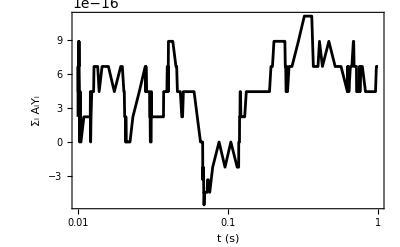

```mathematica
LogLinearPlot[Ytot["HT"][tv]-1,{tv,t0,tmiddle},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

Middle temperature era

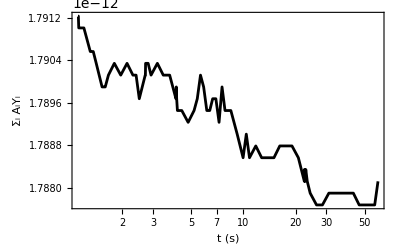

```mathematica
LogLinearPlot[Ytot["MT"][tv]-1,{tv,tmiddle*1.1,0.6t18},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

Low temperature era with the full network.

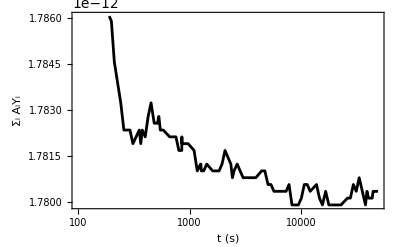

```mathematica
LogLinearPlot[Ytot["LT"][t]-1,{t,t18,tend},Frame->True,FrameLabel->{"t (s)","Σ_i A_iY_i"},PlotStyle->Black]
```

## Time evolution of abundances

### Early thermodynamical equilibrium

Estimate of T_nuc (see companion paper)

```mathematica
TFreeze=0.8 MeV/kB;
tFreeze=tofa@a@TFreeze
YnF[tv_]:=1/(1+Exp[Q/kB/TFreeze])Exp[-(tv-tFreeze)/τneutron ];
YpF[tv_]:=1-YnF[tv];
```

1.1705

```mathematica
tnuc=FindRoot[YNSE["d",YnF[tv],YpF[tv],Toft[tv]]==YnF[tv],{tv,100}][[1,2]]
Tnuc=Toft[tnuc]
```

296.703

7.69597×10^8

Abundance of neutrons at T_nuc and T_nuc in MeV

```mathematica
YnF[tnuc]
kB*Tnuc/MeV
```

0.118336

0.0663188

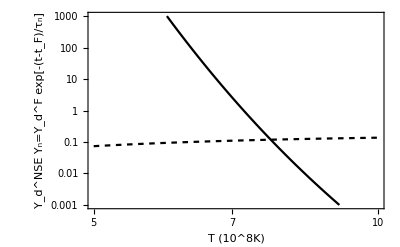

```mathematica
PlotDeutEq=Show[LogLogPlot[{YnF[tofa@a[10^8 Tv]],YNSE["d",YnF[tofa@a[10^8Tv]],YpF[tofa@a[10^8Tv]],10^8Tv]},{Tv,0.05*10^2,0.1*10^2},GridLines->{{{Tnuc,{Gray,Thickness[0.005]}}},{}},Frame->True,PlotRange->{{0.05*10^2,0.1*10^2},{10^-3,10^3}},PlotRangePadding->None,FrameStyle->Thickness[0.004],PlotStyle->{{Black,Thickness[0.004],Dashing[0.01]},{Black,Thickness[0.004]}},PlotRange->{10^-3,1000},FrameLabel->{"T (10^8K)","Y_d^NSE      Y_n=Y_d^F exp[-(t-t_F)/τ_n]"},LabelStyle->{FontSize->12}],
Graphics[{Rotate[Text[Style["0.066 MeV",FontSize->10,Black],{Log@Tnuc-0.015,2}],90 Degree]}]]

If[$ResultsPlots,Export["Plots/PlotDeutEq.pdf",Style[PlotDeutEq,Magnification->1],"PDF"];]
```

Checks of thermo equilibrium at early times.
We check the accuracy of thermal equilibrium for “d” “t” “a” “Li7”. 
Most important is deuterium because it determines the final Helium abundance.

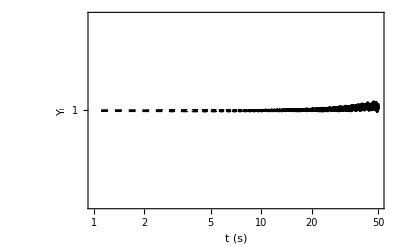

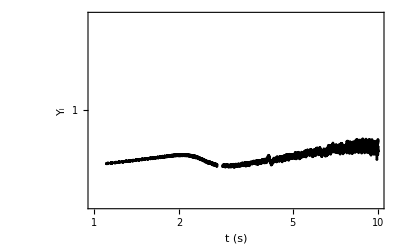

```mathematica
LogLogPlot[{YI["d"][tv]/YNSE["d",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,50},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

LogLogPlot[{YI["t"][tv]/YNSE["t",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,10},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

(*LogLogPlot[{YI["a"][tv]/YNSE["a",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,1.5},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},FrameTicks->MyTicks,ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]

LogLogPlot[{YI["Li7"][tv]/YNSE["Li7",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,1.5},Frame->True,FrameLabel->{"t (s)","Y_i"},PlotStyle->{Black,{Black,Dashed}},FrameTicks->MyTicks,ImagePadding->{{50,10},{40,25}},PlotRange->{0.999,1.001}]*)
```

We plot early values together with thermal equilibrium in dashes

```mathematica
MyTickst={{Automatic,Automatic},{Automatic,{{tofa@a[10^11],"10^11K"},{tofa@a[10^10.5],"10^10.5K"},{tofa@a[10^10],"10^10K"},{tofa@a[10^9.5],"10^9.5K"},{tofa@a[10^9],"10^9K"},{tofa@a[10^8.5],"10^8.5K"},{tofa@a[10^8],"10^8K"}}}};
```

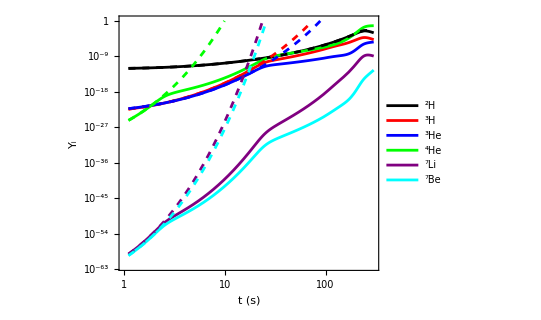

```mathematica
PL1=LogLogPlot[{YI["d"][tv],YI["t"][tv],YI["He3"][tv],YI["a"][tv],YI["Li7"][tv],YI["Be7"][tv],YNSE["d",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["t",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["He3",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["a",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["Li7",YI["n"][tv],YI["p"][tv],Toft[tv]],YNSE["Be7",YI["n"][tv],YI["p"][tv],Toft[tv]]},{tv,tmiddle*1.1,300},Frame->True,FrameLabel->{"t (s)","Y_i"},FrameTicks->MyTickst,LabelStyle->{FontSize->13},FrameStyle->Thickness[0.004],PlotRange->{10^-62,1},AspectRatio->.8,PlotStyle->{Black,Red,Blue,Green,Purple,Cyan,{Black,Dashed},{Red,Dashed},{Blue,Dashed},{Green,Dashed},{Purple,Dashed},{Cyan,Dashed}},(*ImagePadding->{{50,10},{40,25}},*)PlotLegends->Placed[LineLegend[{"^2H","^3H","^3He","^4He","^7Li","^7Be"},LegendLayout->(Grid[#,Frame->None]&)],Left]]

If[$ResultsPlots,Export["Plots/PlotEarlyEquilibrium.pdf",Style[PL1,Magnification->1],"PDF"];]
```

### Neutrons only evolution

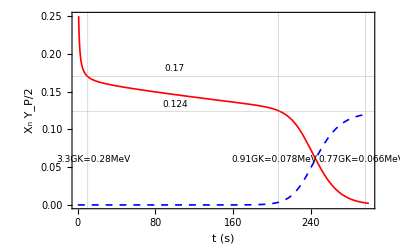

```mathematica
YnCoc=Show[Plot[{YI["n"][tv],Y["WeakInteractionsOnly"]["n"][tv],YI["a"][tv]*2(*,1/(1+Exp[Q/kB/Toft[tv]])*)},{tv,t0,300},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,{{tofa@a[10^9],"1GK"},{tofa@a[.8*10^9],"0.8GK"},{tofa@a[.9*10^9],"0.9GK"},{tofa@a[1.2*10^9],"1.2GK"},{tofa@a[2 10^9],"2GK"}}}},FrameStyle->Thickness[0.004],FrameLabel->{"t (s)","X_n    Y_P/2"},LabelStyle->{FontSize->12},PlotStyle->{{Red,Thickness[0.003]},{Red, Thickness[0.003],Dotted},{Blue, Thickness[0.003],Dashed}},PlotRange->{0,0.25},GridLines->{{{tofa@a[3.3 Giga Kelvin],{Gray,Thickness[0.003]}},{tofa@a[0.91 Giga Kelvin],{Gray,Thickness[0.003]}},{tofa@a[0.77 10^9],{Gray,Thickness[0.003]}}},{{0.124,{Gray,Thickness[0.003]}},{0.17,{Gray,Thickness[0.003]}}}}],
Graphics[{Rotate[Text[Style["3.3GK=0.28MeV",FontSize->9,Black],{16,0.06}],90 Degree],Rotate[Text[Style["0.91GK=0.078MeV",FontSize->9,Black],{203,0.06}],90 Degree],
Rotate[Text[Style["0.77GK=0.066MeV",FontSize->9,Black],{292,0.06}],90 Degree],
Rotate[Text[Style["0.17",FontSize->9,Black],{100,0.18}],0 Degree],
Rotate[Text[Style["0.124",FontSize->9,Black],{100,0.133}],0 Degree]}]]

If[$ResultsPlots,Export["Plots/PlotYnCoc.pdf",Style[YnCoc,Magnification->1],"PDF"];]
```

### Main species of the small network

The plots assume that we have used the full nuclear network and not the reduced one. 
Otherwise some nuclides might not exist and Mathematica should complain ...

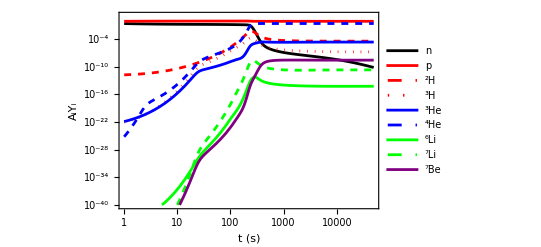

```mathematica
BBNsmall=LogLogPlot[{YI["n"][tv],YI["p"][tv],2YI["d"][tv],3YI["t"][tv],3YI["He3"][tv],4YI["a"][tv],YI["Li6"][tv],YI["Li7"][tv],7YI["Be7"][tv]},{tv,tmiddle,tend},Frame->True,FrameStyle->Thickness[0.003],FrameLabel->{"t (s)","A_iY_i"},LabelStyle->{FontSize->12},PlotRange->{10^-40,10},PlotStyle->{Black,Red,{Red,Dashed},{Red,Dotted},Blue,{Blue,Dashed},Green,{Green,Dashed},Purple},FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"n","p","^2H","^3H","^3He","^4He","^6Li","^7Li","^7Be"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
```

```mathematica
If[$ResultsPlots,Export["Plots/BBNsmall.pdf",BBNsmall,"PDF"];]
```

### From Hydrogen to Borron

Custom colors for plots of a given element

```mathematica
ListColor[Color_,n_]:=Take[Join[{{Color,Thickness[0.004]}},
Table[{Color,Thickness[0.004],Dashing[(i)0.01]},{i,1,3}],
Table[{Color,Thickness[0.004],Dashing[{0,0.015*i,(i)0.015,i 0.015}]},{i,1,4}]],n]
```

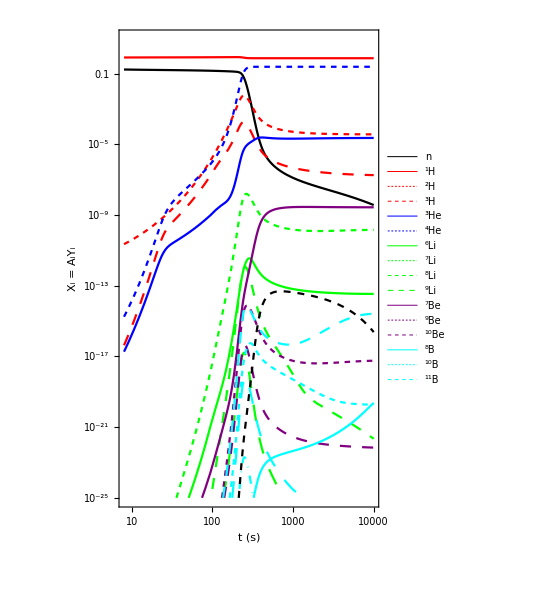

```mathematica
BBNsmall2=LogLogPlot[{XI["n"][tv],XI["p"][tv],XI["d"][tv],XI["t"][tv],XI["He3"][tv],XI["a"][tv],XI["Li6"][tv],XI["Li7"][tv],XI["Li8"][tv],XI["Li9"][tv],XI["Be7"][tv],XI["Be9"][tv],XI["Be10"][tv],XI["B8"][tv],XI["B10"][tv],XI["B11"][tv],XI["B12"][tv],XI["B13"][tv],XI["C11"][tv]},{tv,8,10^4},Frame->True,FrameLabel->{"t (s)","X_i = A_iY_i"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{10^-25,9},PlotStyle->Join[ListColor[Black,1],ListColor[Red,3],ListColor[Blue,2],ListColor[Green,4],ListColor[Purple,3],ListColor[Cyan,5],{{Black,Thickness[0.004],Dashed}}],AspectRatio->1.5,FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"n","^1H","^2H","^3H","^3He","^4He","^6Li","^7Li","^8Li","^9Li","^7Be","^9Be","^10Be","^8B","^10B","^11B","^12B","^13B","^11C"},LegendLayout->(Grid[#,Frame->None]&)],Right]]


If[$ResultsPlots,Export["Plots/PlotBBNLight.pdf",Style[BBNsmall2,Magnification->1],"PDF"];]
```

### From Carbon to Oxygen

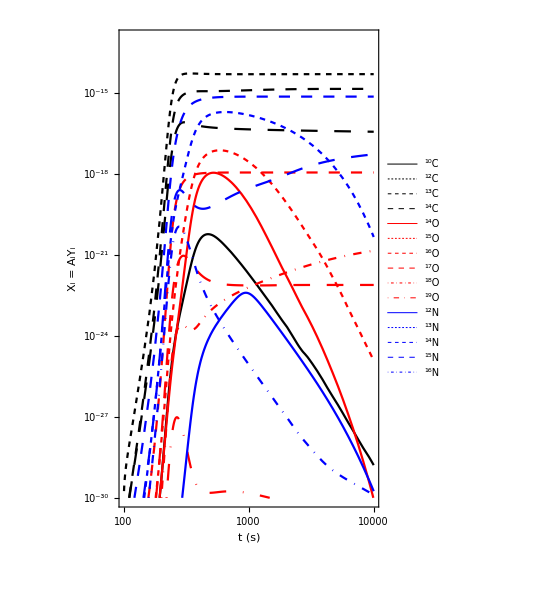

```mathematica
If[Not[$ReducedNetwork],BBNCNO=LogLogPlot[{XI["C10"][tv],XI["C12"][tv],XI["C13"][tv],XI["C14"][tv],XI["O14"][tv],XI["O15"][tv],XI["O16"][tv],XI["O17"][tv],XI["O18"][tv],XI["O19"][tv],XI["N12"][tv],XI["N13"][tv],XI["N14"][tv],XI["N15"][tv],XI["N16"][tv]},{tv,1.01t18,10^4},Frame->True,FrameLabel->{"t (s)","X_i = A_iY_i"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotRange->{10^-30,10^-13},PlotStyle->Join[ListColor[Black,4],ListColor[Red,6],ListColor[Blue,5],ListColor[Purple,1]],AspectRatio->1.5,FrameTicks->MyTickst,ImagePadding->{{50,10},{40,25}},PlotLegends->Placed[LineLegend[{"^10C","^12C","^13C","^14C","^14O","^15O","^16O","^17O","^18O","^19O","^12N","^13N","^14N","^15N","^16N"},LegendLayout->(Grid[#,Frame->None]&)],Right]]
]

If[$ResultsPlots&&Not[$ReducedNetwork],
Export["Plots/PlotBBNHeavy.pdf",Style[BBNCNO,Magnification->1],"PDF"];];
```

## Final abundances

### Main results

Final time at T= 4 10^7 K in seconds.

```mathematica
tofa[a[4*10^7]]
```

110753.

Standard abundances as reported in most BBN papers.  Note the definition Y_P = 4 Y_He4. Since the atomic mass of Helium is not exactly 4 this is not exactly Helium mass abundance

```mathematica
MyGrid@Transpose[{{"H","Y_P=4Y_He","D/H x 10^5","^3He/H x 10^5","T/H x 10^8","(^3He+T)/H x 10^5","^7Li/H x 10^11","^7Be/H x 10^10","(^7Li+^7Be)/H x 10^10","^6Li/H x 10^14","^9Be/H x 10^19","^10B/H x 10^21","^11B/H x 10^16","CNO/H x 10^16","N_eff"},{Yf["p"],4Yf["a"],YfH["d"] 10^5,YfH["He3"] 10^5,YfH["t"] 10^8,(YfH["t"]+YfH["He3"])10^5,YfH["Li7"] 10^11,YfH["Be7"] 10^10,(YfH["Li7"]+YfH["Be7"])10^10,YfH["Li6"] 10^14,YfH["Be9"] 10^19,YfH["B10"] 10^21,YfH["B11"] 10^16,YfH["CNO"] 10^16,Neff}}]
```

H | 0.75293
Y_P=4Y_He | 0.24701
D/H x 10^5 | 2.4365
^3He/H x 10^5 | 1.0314
T/H x 10^8 | 7.75661
(^3He+T)/H x 10^5 | 1.03915
^7Li/H x 10^11 | 2.84085
^7Be/H x 10^10 | 5.22243
(^7Li+^7Be)/H x 10^10 | 5.50652
^6Li/H x 10^14 | 0.779276
^9Be/H x 10^19 | 8.76396
^10B/H x 10^21 | 2.44491
^11B/H x 10^16 | 3.25168
CNO/H x 10^16 | 7.8058
N_eff | 3.04398

### All final abundances

Final number fractions

```mathematica
MyGrid[{#,Yf[#]}&/@ShortNames]
```

n | 7.1588×10^-11
p | 0.75293
d | 0.0000183452
t | 5.84018×10^-8
He3 | 7.76569×10^-6
a | 0.0617525
Li7 | 2.13896×10^-11
Be7 | 3.93213×10^-10
He6 | 4.49571×10^-44
Li6 | 5.8674×10^-15
Li8 | 4.98816×10^-26
Li9 | 3.33343×10^-41
Be9 | 6.59864×10^-19
Be10 | 6.45095×10^-24
Be11 | 2.45399×10^-38
Be12 | 1.0241×10^-55
B8 | 1.02833×10^-23
B10 | 1.84084×10^-21
B11 | 2.44829×10^-16
B12 | 1.80439×10^-32
B13 | 1.55579×10^-48
B14 | 2.45665×10^-63
B15 | 1.37068×10^-81
C9 | 2.05459×10^-40
C10 | 8.5438×10^-37
C11 | 4.67618×10^-27
C12 | 4.21058×10^-16
C13 | 1.10489×10^-16
C14 | 2.42008×10^-18
C15 | 5.31726×10^-34
C16 | 2.01268×10^-49
N12 | 1.55766×10^-45
N13 | 1.45128×10^-28
N14 | 5.3095×10^-17
N15 | 5.88578×10^-19
N16 | 3.1681×10^-34
N17 | 2.37378×10^-44
O13 | -1.72006×10^-58
O14 | 3.19507×10^-43
O15 | 6.55453×10^-32
O16 | 7.15328×10^-20
O17 | 4.56798×10^-24
O18 | 1.33207×10^-22
O19 | 6.66158×10^-36
O20 | 6.2975×10^-49
F17 | 5.45843×10^-36
F18 | 8.66906×10^-25
F19 | 6.33967×10^-26
F20 | 3.84432×10^-38
Ne18 | 3.69657×10^-49
Ne19 | 1.30026×10^-41
Ne20 | 6.80494×10^-28
Ne21 | 5.31265×10^-30
Ne22 | 8.81707×10^-32
Ne23 | -4.69705×10^-74
Na20 | 8.24334×10^-64
Na21 | -1.94024×10^-77
Na22 | 1.76751×10^-36
Na23 | 1.08235×10^-37

Table in mass fraction instead of number fraction. So we use X_i = A_i Y_i.

```mathematica
TableXMass={#,Xf[#]}&/@Join[ShortNames,{"CNO"}];
MyGrid[TableXMass]
```

n | 7.1588×10^-11
p | 0.75293
d | 0.0000366903
t | 1.75206×10^-7
He3 | 0.0000232971
a | 0.24701
Li7 | 1.49727×10^-10
Be7 | 2.75249×10^-9
He6 | 2.69743×10^-43
Li6 | 3.52044×10^-14
Li8 | 3.99052×10^-25
Li9 | 3.00009×10^-40
Be9 | 5.93878×10^-18
Be10 | 6.45095×10^-23
Be11 | 2.69939×10^-37
Be12 | 1.22891×10^-54
B8 | 8.22661×10^-23
B10 | 1.84084×10^-20
B11 | 2.69312×10^-15
B12 | 2.16527×10^-31
B13 | 2.02253×10^-47
B14 | 3.4393×10^-62
B15 | 2.05602×10^-80
C9 | 1.84914×10^-39
C10 | 8.5438×10^-36
C11 | 5.14379×10^-26
C12 | 5.05269×10^-15
C13 | 1.43635×10^-15
C14 | 3.38811×10^-17
C15 | 7.9759×10^-33
C16 | 3.2203×10^-48
N12 | 1.86919×10^-44
N13 | 1.88667×10^-27
N14 | 7.43331×10^-16
N15 | 8.82867×10^-18
N16 | 5.06896×10^-33
N17 | 4.03542×10^-43
O13 | -2.23608×10^-57
O14 | 4.4731×10^-42
O15 | 9.8318×10^-31
O16 | 1.14452×10^-18
O17 | 7.76556×10^-23
O18 | 2.39773×10^-21
O19 | 1.2657×10^-34
O20 | 1.2595×10^-47
F17 | 9.27933×10^-35
F18 | 1.56043×10^-23
F19 | 1.20454×10^-24
F20 | 7.68864×10^-37
Ne18 | 6.65383×10^-48
Ne19 | 2.47049×10^-40
Ne20 | 1.36099×10^-26
Ne21 | 1.11566×10^-28
Ne22 | 1.93976×10^-30
Ne23 | -1.08032×10^-72
Na20 | 1.64867×10^-62
Na21 | -4.0745×10^-76
Na22 | 3.88852×10^-35
Na23 | 2.48941×10^-36
CNO | 7.27624×10^-15

Uncomment if you want to output results in external file

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["TableXMass.dat",TableXMass,"TSV"]*)
```

```mathematica
(*TableXMassT8={#,XI[#][tofa[a[10^8]]]}&/@Join[ShortNames,{"CNO"}]*)
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["TableXMassT8.dat",TableXMassT8,"TSV"]*)
```

## Tools for Monte-Carlo on nuclear rates

We gather some tools for Monte-Carlo estimation of uncertainties from nuclear rates. 
Some Examples are provided in the Example folder.

Initialize Kernels (if parallelization this is called. It just distributes definitions)

```mathematica
InitializeKernels:=(
LaunchKernels[];
Print["Number of Kernels ",$KernelCount];
DistributeDefinitions[ReshapedTabulatedReactions,ListReactionsUpToChosenMass,LoadRates,DefineEquations,SystemEquationsHT,SystemEquationsMT,SystemEquationsLT,
LoadPlasma,LoadNEVO,LoadDistortions,LoadWeakRates,LoadRatesFull,DY,DY18,DYOnlyPEN,LbarnTOp,LnTOp,dFDneu];
);
```

We define a function which launches the Monte-Carlo on subKernels and collects the results. Note that if $RecomputeWeakRates=True this can be absurdely slow since weak rates will be computed all the time.

```mathematica
RunPRIMATMonteCarlo[number_]:=Module[{res,time,timref,Abundances,mytabfunctions,sss,RandomVariables,CosmoParametersList,oldbookrecomputeweakrates},

If[$Verbose,
Print["Reaction file used is : ",ChosenReactionFile];
(*Print[StringJoin@@(#<>" "&/@SafeImport[ChosenReactionFile][[1]])];*)

(*Print[MyGrid[Join[{{"Reaction Number","Reaction Name","Initial species","Final Species","Reference"}},PadLeftNumberRowFromZero[Drop[#,{4}]&/@(NiceDisplayReaction/@ListReactionsUpToChosenMass)]]]];*)
];

(* We deal with weak rates first*)
oldbookrecomputeweakrates=$RecomputeWeakRates;
If[Not@FileExistsQ[NamePENFilenp]||Not@FileExistsQ[NamePENFilepn]||$RecomputeWeakRates,RunBackgroundThermo;ComputeWeakRates;];
$RecomputeWeakRates=False;

If[number>1,Print["Running a Monte-Carlo with ",number, " points."];];
Off[CompiledFunction::cfta];
mytabfunctions=If[$ParallelBool,ParallelTable,Table];
(* If there are no existing PEN rates on hard disk we compute them BEFORE the MOnte-Carlo is run to avoid all subKernels from computing them.*)


If[$ParallelBool,InitializeKernels;
ParallelEvaluate[$HistoryLength=0;]];

(* We always use the same seed so that we always use the same sequence of random number as advocated in [Cyburt et al. 2015].*)
timref=AbsoluteTime[];
res=mytabfunctions[
$Seed:=i;(* We use a different seed so that for each MC point we have a different sequence of reaction rates *)
InitializeRandom[$Seed];(* We restart our random list from the beginning *)

h2Ωb0=Meanh2Ωb0+If[$Randomh2Ωb,σh2Ωb0 NormalRealisation,0];
τneutron=Meanτneutron+If[$Randomτneutron,στneutron NormalRealisation,0];
CosmoParametersList={h2Ωb0,τneutron};

time=AbsoluteTiming[RunNumericalIntegrals][[1]];
RandomVariables=Rest@ListReactionsUpToChosenMass[[All,4]];
(*Share[];*)
Print["Iteration ",i, "  Memory usage = ",MemoryInUse[]," time = ",time, "  Kernel : ",$KernelID];
Abundances=YPeriodTime["LT"][tend];
(*ClearSystemCache[];*)
If[$Verbose,Print[Abundances(*," ",RandomVariables*)]];
{Abundances,RandomVariables,CosmoParametersList},{i,1,number}];

If[$ParallelBool,CloseKernels[]];
Share[];
ClearSystemCache[];
Print["Time in the MC for that cosmology was ",AbsoluteTime[]-timref];
h2Ωb0=Meanh2Ωb0;
τneutron=Meanτneutron;
MC=res[[All,1]];
RV=res[[All,2]];
Cosmo=res[[All,3]];
$RecomputeWeakRates=oldbookrecomputeweakrates;

res];

RunPRIMAT:=RunPRIMATMonteCarlo[1];
```

The results of RunPRIMAT are gathered in the files MC (abundances) RV (rates variations) Cosmo (List of cosmological parameters, limited to baryons abundances and neutron lifetime)

We define functions to dump the results of a Monte-Carlo in a file and also the converse to load the result so as to analyze and use it.

```mathematica
Clear[LoadMC,DumpMC]
```

```mathematica
DumpMC[File_String]:=(
Print["Exporting ","Results/MC"<>File<>".dat"];
Export[$ResultsDirectory<>"MC"<>File<>".dat",MC];
Print["Exporting ","Results/MC"<>File<>".mx"];
DumpSave[$ResultsDirectory<>"MC"<>File<>".mx",MC];

Print["Exporting ","Results/RV"<>File<>".dat"];
Export[$ResultsDirectory<>"RV"<>File<>".dat",RV];
Print["Exporting ","Results/RV"<>File<>".mx"];
DumpSave[$ResultsDirectory<>"RV"<>File<>".mx",RV];

Print["Exporting ","Results/Cosmo"<>File<>".dat"];
Export[$ResultsDirectory<>"Cosmo"<>File<>".dat",Cosmo];
(*DumpSave["Results/Cosmo"<>File<>".mx",Cosmo];*)
);

LoadMC[File_String]:=(
Get[$ResultsDirectory<>"MC"<>File<>".mx"];
(*MCfile="Results/MC"<>File<>".dat";
 MC=Import[MCfile];*)
Get[$ResultsDirectory<>"RV"<>File<>".mx"];
(*RVfile="Results/RV"<>File<>".dat";
RV=Import[RVfile];*)
Cosmofile=$ResultsDirectory<>"Cosmo"<>File<>".dat";
Cosmo=Import[Cosmofile];
TMC=Transpose[MC];
);
```

Whenever a Monte-Carlo is finished, or loaded, we can obtain the table of values for a given element, or a given reaction

```mathematica
ElementColumn[el_]:=MC[[All,KeyVal[[el]]]];
ReactionColumn[el_]:=RV[[All,KeyNuclearReaction[el]]];
h2Ωb0List:=Cosmo[[All,1]];
τneutronList:=Cosmo[[All,2]];
```

```mathematica
(* I think this function is never used ! *)
ReSetCosmology:=(
Meanh2Ωb0=Meanh2Ωb0Planck; 
NeutrinosGenerations=3;
Nrelat=0;(* Not sure this is needed. *)
);
```